# Perturbative expansion for SHOs with a Pöschl-Teller coupling

## License and author info

Copyright © Ibai Asensio, 2025.

This Mathematica code performs a perturbative expansion of the equations of motion for two weakly coupled simple harmonic oscillators (SHOs) with a Pöschl-Teller coupling. The results are computed analytically to first perturbation order, and numerically to second order, and compared with the full numerical solution.

This code is free software: you can redistribute it and/or modify it under the terms of the GNU General Public License, v3.0, as published by the Free Software Foundation. For more information, visit: https://www.gnu.org/licenses/

Developed by Ibai Asensio as part of the master thesis: ‘Towards Adiabatic States for Perturbations in Anisotropic Spacetimes. Analytical Approximations for Coupled Differential Equations in Quantum Fields in Curved Spacetimes’.

Supervisors:		Béatrice Bonga (Radboud Universiteit)
				Javier Olmedo (Universidad de Granada)
Second reader:	Wim J.P. Beenakker (Radboud Universiteit)

Part of a the  odes-approximations  project; find more accompanying files on the project’s repository.
If you find this code useful, or have any thoughtful feedback, you are encouraged to contact the author and let him know.

## Preamble

## Variables

#### Clearing variables

```mathematica
ClearAll["Global`*"]
```

## Custom functions

### Pöschl-Teller potential

#### Potential

```mathematica
PoschlTeller[t_]:=√(ω^2+α^2 Sech[t/τ]^2)
PoschlTeller[t]
```

√(ω^2+α^2 Sech[t/τ]^2)

```mathematica
PoschlTeller[ω_,α_,τ_][t_]:=√(ω^2+α^2 Sech[t/τ]^2)
```

#### Parameters it needs

ω  is the asymptotic value at t → ± ∞ .
α  sets the maximum value (that occurs at t = 0) once given ω, being:
	max=√(ω^2+α)  ->  α=max^2 -ω^2.
τ  sets the width of the potential, roughly being four times τ.

### Pöschl-Teller potential (squared)

#### Potential

```mathematica
PoschlTellerSq[ω_,α_,τ_][t_]:=ω^2+α^2 Sech[t/τ]^2
PoschlTellerSq[ω,α,τ][t]
```

ω^2+α^2 Sech[t/τ]^2

#### Parameters it needs

ω  is the asymptotic value at t → ± ∞ .
α  sets the maximum value (that occurs at t = 0) once given ω, being:
	max=ω+α  ->  α=max-ω.
τ  sets the width of the potential, roughly being four times τ.

### Klein-Gordon product

These functions adopt the notation v⃗=(x_1,x_2,...,v_1,v_2,...) for elements of the phase space, and implement the Klein-Gordon inner product ((v⃗)^(1),(v⃗)^(2))=ⅈ(v⃗)^(1)ω ((v⃗)^(2))* , with ω the corresponding N-dimensional symplectic matrix.

```mathematica
SymplecticMatrix[n_]:=KroneckerProduct[{{0,1},{-1,0}},IdentityMatrix[n]]
```

```mathematica
PhaseSpaceArray[x_]:={Array[{x}[[#]]&,Length[{x}]],Array[D[{x}[[#]],t]&,Length[{x}]]}//Flatten
```

```mathematica
KleinGordonProduct[va_,vb_]:=If[
(*Condition:*)Length[va]===Length[vb],
(*Then:*)ⅈ PhaseSpaceArray[va].SymplecticMatrix[Length[PhaseSpaceArray[va]]/2].Conjugate[PhaseSpaceArray[vb]],
(*Else:*)Print["Dimensions of vectors do not agree."]]
```

```mathematica
KleinGordonNorm[v_]:=KleinGordonProduct[v,v]
```

### Linear algebra

Build a linear operator from a vector set (i.e. the linear operator which transforms the basis vectors into the vector set provided to the function):

```mathematica
LinearOperator[vectorset_]:=Transpose[vectorset]
```

Change-of-basis matrix (the same operation as building a linear operator):

```mathematica
ChangeofBasisMatrix[newbasis_]:=Transpose[newbasis]
```

Change of basis for a matrix:

```mathematica
ChangedBasisMatrix[M_,newbasis_]:=Inverse[Transpose[newbasis]].M.Transpose[newbasis]//Simplify
```

Change of basis for a vector:

```mathematica
ChangedBasisVector[v_,newbasis_]:=Inverse[Transpose[newbasis]].v//Simplify
```

#### Some extra vector and matrix operations

Also, since Mathematica doesn’t distinguish between vectors and dual vectors (the built-in Transpose function doesn’t have any effect) some vector and matrix operations are not included by default. For example:

Bra-ket operator (i.e. dual vector acting on a vector):

```mathematica
Braket[u_,v_]:=({v}.Transpose[{u}])[[1]][[1]]
```

(This has the same effect as the Dot operation. However, the next functions are not.)

Ket-bra operator (i.e. vector acting on a dual vector):

```mathematica
Ketbra[u_,v_]:=Transpose[{u}].{v}
```

Vector-matrix multiplication:

```mathematica
DotVectorMatrix[v_,M_]:=
If[Length[v]==Length[M],
Array[∑_(l=1)^Length[v] v[[l]]M[[l,#]]&,Length[v]],
(* Else: *)
 Print["Error: Dimensions doesn't agree."]
]
```

## Shortcuts

#### Colors and legends

Perturbative orders + coupling:

```mathematica
plotLegendsPert={
"Osc. 1 - Full","Osc. 2 - Full","Coupling (norm.)",
"Osc. 1 - 1st ord.","Osc. 2 - 1st ord.",
"Osc. 1 - 2nd ord.","Osc. 2 - 2nd ord."};
```

```mathematica
plotStylePertAll={RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],{Dashed,RGBColor[0.560181, 0.691569, 0.194885]},{Dashed,RGBColor[0.368417, 0.506779, 0.709798]},{Dashed,RGBColor[0.880722, 0.611041, 0.142051]},{Dashing[Large],RGBColor[0.368417, 0.506779, 0.709798]},{Dashing[Large],RGBColor[0.880722, 0.611041, 0.142051]}};
```

```mathematica
plotLegendsErrors={
"Error osc. 1 - 1st ord.","Error osc. 2 - 1st ord.",
"Error osc. 1 - 2nd ord.","Error osc. 2 - 2nd ord."};
```

```mathematica
plotStyleErrors={{Dashed,RGBColor[0.28240003484173815, 0.6090799721266095, 0.7538800418100857]},{Dashed,RGBColor[0.922526, 0.385626, 0.209179]},{Dotted,RGBColor[0.28240003484173815, 0.6090799721266095, 0.7538800418100857]},{Dotted,RGBColor[0.922526, 0.385626, 0.209179]}};
```

#### Static legend

```mathematica
legendOrders={
"0th order: Osc. 1","0th order: Osc. 2"(*,"0th order: Osc. 3"*),
"1st order: Osc. 1","1st order: Osc. 2"(*,"1st order: Osc. 3"*),
"2nd order: Osc. 1","2nd order: Osc. 2"(*,"2nd order: Osc. 3"*),
"3rd order: Osc. 1","3rd order: Osc. 2"(*,"3rd order: Osc. 3"*),
"4th order: Osc. 1","4th order: Osc. 2"(*,"4th order: Osc. 3"*),
"5th order: Osc. 1","5th order: Osc. 2"(*,"5th order: Osc. 3"*),
"6th order: Osc. 1","6th order: Osc. 2"(*,"6th order: Osc. 3"*)};
```

#### Linear algebra shortcuts

Quick identity matrix:

```mathematica
II:=IdentityMatrix[dim];
```

Quick identity vector:

```mathematica
vI:=DiagonalMatrix[Array[1&,dim]];//Quiet
```

Quick zero matrix:

```mathematica
m0:=Array[0&,{dim,dim}];//Quiet
```

Quick zero vector:

```mathematica
v0:=Array[0&,dim];//Quiet
```

## Problem and chosen model

## Generic inputs

### Dimension (number of equations)

```mathematica
dim=2;
```

### Perturbative order

```mathematica
orderPrt=2;
```

## Equation/s of motion

```mathematica
Eom[M_,x_]:=D[x,{t,2}]+T^2 M.x
```

#### Symbolically

```mathematica
Eom[M[t],x[t]]
```

T^2 M[t].x[t]+x''[t]

#### Vectors & matrices’ components

```mathematica
mM[t_]=Array[M[#1,#2][t]&,{dim,dim}]
```

{{M[1,1][t],M[1,2][t]},{M[2,1][t],M[2,2][t]}}

```mathematica
vx[t_]=Array[x[#][t]&,dim]
```

{x[1][t],x[2][t]}

#### EOM in components

```mathematica
Eom[mM[t],vx[t]]//MatrixForm
```

(T^2 (M[1,1][t] x[1][t]+M[1,2][t] x[2][t])+x[1]''[t]
T^2 (M[2,1][t] x[1][t]+M[2,2][t] x[2][t])+x[2]''[t])

## Specializing the problem (form of the M(t) matrix and functions therein)

Specifying a model here means to select a specific matrix M(t), i.e.  mM[t_] in the code.

Here we particularize it for two generic, coupled, time-dependent harmonic oscillators.

We choose a Pöschl-Teller form for both the time-dependent frequencies and the coupling, with the option to be able to set the frequencies constant as well if we like.

### Frequency-coupling models

#### Masses and frequencies vectors

```mathematica
vm[t_]=Array[m[#][t]&,dim];
vm[t]//MatrixForm
```

(m[1][t]
m[2][t])

```mathematica
vΩ[t_]=Array[Ω[#][t]&,dim];
vΩ[t]//MatrixForm
```

(Ω[1][t]
Ω[2][t])

#### M(t) matrix

Construction of the M(t) matrix:

```mathematica
mM[t_]=DiagonalMatrix[vΩ[t]^2]+2DiagonalMatrix[kc[t]/vm[t]]-Array[Array[kc[t]&,dim]/m[#][t]&,dim];
mM[t]//MatrixForm
```

(kc[t]/(m[1][t])+(Ω[1][t])^2 | -kc[t]/(m[1][t])
-kc[t]/(m[2][t]) | kc[t]/(m[2][t])+(Ω[2][t])^2)

#### Corresponding EOM

```mathematica
For[i=1,i<=dim,i++,Print[Eom[mM[t],vx[t]][[i]]]];ClearAll[i]
```

T^2 (-(kc[t] x[2][t])/(m[1][t])+x[1][t] (kc[t]/(m[1][t])+(Ω[1][t])^2))+x[1]''[t]

T^2 (-(kc[t] x[1][t])/(m[2][t])+x[2][t] (kc[t]/(m[2][t])+(Ω[2][t])^2))+x[2]''[t]

#### Updated EOMs

```mathematica
For[i=1,i<=dim,i++,{
eom[i][t_]=Eom[mM[t],vx[t]][[i]]//ExpandAll,
Print[eom[i][t]]
}]
```

(T^2 kc[t] x[1][t])/(m[1][t])-(T^2 kc[t] x[2][t])/(m[1][t])+T^2 x[1][t] (Ω[1][t])^2+x[1]''[t]

-(T^2 kc[t] x[1][t])/(m[2][t])+(T^2 kc[t] x[2][t])/(m[2][t])+T^2 x[2][t] (Ω[2][t])^2+x[2]''[t]

### Specification of masses, frequencies and coupling

#### Specification of masses ↪︎ Equal, constant and normalized

```mathematica
m[1][t_]=1;
m[2][t_]=1;(*
m[3][t_]=1;*)
vm[t]
```

{1,1}

#### Specification of frequencies ↪︎ Constant

```mathematica
freqconst={Ω[j_][t]:>ω[j](*,Ω[_][j_][t]:>ω[j]*)}
```

{Ω[j_][t]:>ω[j]}

In case we want to set different frequency functions, we can use (e.g., for Pöschl-Teller frequencies):

```mathematica
(*freqspec={
Ω[j_]:>Function[t,Assuming[t∈Reals,Refine[
PoschlTeller[ω[j],α[j],τ[j]][t]
]]]}*)
```

```mathematica
(*Ω[j][t]/.freqspec*)
```

#### Specification of the coupling ↪︎ Modified (squared) Pöschl-Teller

```mathematica
couplspec={kc:>Function[t,Assuming[t∈Reals,Refine[
PoschlTellerSq[ω[c],α[c],τ[c]][t]
]]]}
```

{kc:>Function[t,Assuming[t∈ℝ,Refine[PoschlTellerSq[ω[c],α[c],τ[c]][t]]]]}

```mathematica
kc[t]/.couplspec
```

Sech[t/τ[c]]^2 α[c]^2+ω[c]^2

```mathematica
(*kc[t_]=kc[t]/.(couplspec/.param)*)
```

#### Corresponding M(t) matrix

Construction of the M(t) matrix:

```mathematica
mM[t]/.freqconst/.couplspec//MatrixForm
```

(Sech[t/τ[c]]^2 α[c]^2+ω[1]^2+ω[c]^2 | -Sech[t/τ[c]]^2 α[c]^2-ω[c]^2
-Sech[t/τ[c]]^2 α[c]^2-ω[c]^2 | Sech[t/τ[c]]^2 α[c]^2+ω[2]^2+ω[c]^2)

### EOMs for the chosen functions

```mathematica
For[i=1,i<=dim,i++,{
Print[eom[i][t]/.freqconst/.couplspec]
}]
```

T^2 ω[1]^2 x[1][t]+T^2 (Sech[t/τ[c]]^2 α[c]^2+ω[c]^2) x[1][t]-T^2 (Sech[t/τ[c]]^2 α[c]^2+ω[c]^2) x[2][t]+x[1]''[t]

-T^2 (Sech[t/τ[c]]^2 α[c]^2+ω[c]^2) x[1][t]+T^2 ω[2]^2 x[2][t]+T^2 (Sech[t/τ[c]]^2 α[c]^2+ω[c]^2) x[2][t]+x[2]''[t]

### Parameters’ values

#### Pöschl-Teller parameters

NOTE that the oscillators CANNOT HAVE the exact same frequency, for there are expressions that would get divided by zero.

```mathematica
param={
(*Asymptotic frequencies:*)
(*Osc. 1:*) ω[1]->17,
(*Osc. 2:*) ω[2]->18,(*
(*Osc. 3:*) ω[3]->1,*)
(*Coupl.:*) ω[c]->0,

(*Peak-related variable:*)
(*Osc. 1:*) α[1]->4.5^2,
(*Osc. 2:*) α[2]->4.2^2,(*
(*Osc. 3:*) α[3]->1^2^2,*)
(*Coupl.:*) α[c]->3.5(*^2*),

(*Width-related variable:*)
(*Osc. 1:*) τ[1]->1,
(*Osc. 2:*) τ[2]->1,(*
(*Osc. 3:*) τ[3]->1,*)
(*Coupl.:*) τ[c]->1
};
```

↪︎ Note the very little difference in the asymptotic frequencies of oscillators 1 and 2.
	- This is to be able to have noticable effects on the second oscillator.
	- They also make both oscillators be near their resonance, which makes exciting the second oscillator much easier, and thus it “costs less energy” to the first one. This makes the first-order perturbative solution not so far from the actual solution.
	- Hence, it’s true that this particular set of parameters is a bit fine-tuned in order to obtain neat graphs.

#### Plot

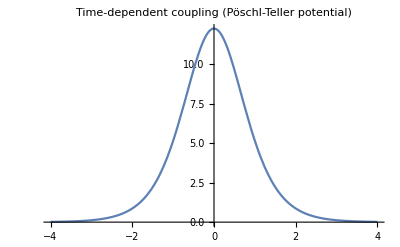

```mathematica
Plot[Evaluate[{PoschlTellerSq[ ω[c],α[c],τ[c]][t]}/.param],{t,-4,4},PlotLabel->"Time-dependent coupling
(Pöschl-Teller potential)"]
```

### Assumptions on the parameters

```mathematica
$Assumptions={t∈Reals,t>0,T∈Reals,T>0,ω[_]∈Reals,ω[_]>0,α[_]∈Reals,α[_]>0,τ[_]∈Reals,τ[_]>0};
```

## Initial conditions

### Initial conditions for solutions and derivatives

#### Single-oscillator excited i.c.’s

```mathematica
icSolSingleOsc1={A[1]/√T,0(*,0*)};
```

```mathematica
icSolSingleOsc2={0,A[2]/√T(*,0*)};
```

```mathematica
(*icSolSingleOsc3={0,0,A[3]/√T};*)
```

```mathematica
icDerivStill1={-ⅈ A[1] √T ω[1],0(*,0*)};
```

```mathematica
icDerivStill2={0,-ⅈ A[2] √T ω[1](*,0*)};
```

```mathematica
(*icDerivStill3={0,0,-ⅈ A[3] √T ω[1]};*)
```

#### Normalized initial conditions for the solution

```mathematica
icSoln[j_]={xi[j]->√(2ω[j])};
```

#### Static initial conditions for the derivatives

```mathematica
icDeriv[j_]={vi[j]->0};
```

#### Grids at initial amplitudes for the selected parameters

```mathematica
For[i=1,i<=dim,i++,{
gridY[i]={
+icSolSingleOsc1[[i]]/.param/.A[1]->1/.T->1,
-icSolSingleOsc1[[i]]/.param/.A[1]->1/.T->1
},
grid[i]={{},gridY[i]},
Print["grid[",i,"] = ",grid[i]]
}]
```

grid[1] = {{},{1,-1}}

grid[2] = {{},{0,0}}

### Initial time and relevant time domain

Obs: This evaluation is needed to be done before the perturbative integrals for them to be properly computed.

```mathematica
ti=-4π;
tf=Abs[ti];
ti//N
```

-12.5664

```mathematica
relevantdomain={t,ti,tf}
```

{t,-4 π,4 π}

```mathematica
smalldomain={t,-6*2π/(*ω[1]*)9,6*2π/(*ω[1]*)9}(*/.param*)
smalldomain//N
```

{t,-(4 π)/3,(4 π)/3}

{t,-4.18879,4.18879}

```mathematica
tmax=100;
```

## Perturbative expansion

## Perturbative expansion of the EOMs and formal solutions as nested integrals

### Perturbative expansion of the solutions (in one parameter)

```mathematica
xPert[j_][t_]=(*∑_(n=0)^orderPrt *)∑_(l=0)^(orderPrt(*-n*)) (*ϵ^n*)κ^l x[(*n,*)l][j][t](*+O[ϵ]^(orderPrt+1)*)+O[κ]^(orderPrt+1)
```

x[0][j][t]+x[1][j][t] κ+x[2][j][t] κ^2+O[κ]^3

### Weak-coupling condition

```mathematica
kc:>Function[t,κ kc[t]]
```

kc:>Function[t,κ kc[t]]

### The EOMs expanded

```mathematica
pertexp={
x[1]:>Function[t,xPert[1][t]],
x[2]:>Function[t,xPert[2][t]],(*
x[3]:>Function[t,xPert[3][t]],*)
(*Ω[1]:>Function[t,∑_(n=0)^orderPrt ϵ^n Ω[n][1][t]+O[ϵ]^(orderPrt+1)],
Ω[2]:>Function[t,∑_(n=0)^orderPrt ϵ^n Ω[n][2][t]+O[ϵ]^(orderPrt+1)],
Ω[3]:>Function[t,∑_(n=0)^orderPrt ϵ^n Ω[n][3][t]+O[ϵ]^(orderPrt+1)],*)
kc:>Function[t,κ kc[t]]
};
```

Substituting into the equations of motion we get:

```mathematica
eomPertExp[1][t_]=eom[1][t]/.pertexp
eomPertExp[2][t_]=eom[2][t]/.pertexp
(*eomPertExp[3][t_]=eom[3][t]/.pertexp*)
```

(x[0][1]''[t]+T^2 (Ω[1][t])^2 x[0][1][t])+(x[1][1]''[t]+T^2 kc[t] x[0][1][t]-T^2 kc[t] x[0][2][t]+T^2 (Ω[1][t])^2 x[1][1][t]) κ+(x[2][1]''[t]+T^2 kc[t] x[1][1][t]-T^2 kc[t] x[1][2][t]+T^2 (Ω[1][t])^2 x[2][1][t]) κ^2+O[κ]^3

(x[0][2]''[t]+T^2 (Ω[2][t])^2 x[0][2][t])+(x[1][2]''[t]-T^2 kc[t] x[0][1][t]+T^2 kc[t] x[0][2][t]+T^2 (Ω[2][t])^2 x[1][2][t]) κ+(x[2][2]''[t]-T^2 kc[t] x[1][1][t]+T^2 kc[t] x[1][2][t]+T^2 (Ω[2][t])^2 x[2][2][t]) κ^2+O[κ]^3

### Perturbative EOMs order by order

```mathematica
ClearAll[(*n,*)l,j,t]
```

```mathematica
EomCoeff[(*n_,*)l_][j_][t_]:=(*Coefficient[*)Coefficient[eomPertExp[j][t],κ,l](*,ϵ,n]*);
```

```mathematica
For[i=1,i<=dim,i++,{
(*For[n=0,n<=orderPrt,n++,{*)
For[l=0,l<=orderPrt,l++,{
eomPert[(*n,*)l][i][t_]=EomCoeff[(*n,*)l][i][t]
}]
(*}]*)
}]
```

```mathematica
Print[]
For[roundorder=0,roundorder≤orderPrt,roundorder++,{
For[n=roundorder,n≥0,n--,{
n=0;(*New for single-parameter expansion*)
l=roundorder-n,

(*If[ϵ^n==1,*)

If[κ^l==1,{
Print["Order 0:"],
Print[]
},
False,{
Print["Order ",κ^l,":"],
Print[]
}],

(*False,
If[κ^l==1,{
Print["Order ",ϵ^n,":"],
Print[]
},
False,{
Print["Order ",ϵ^n," ",κ^l,":"]
}]
],*)

For[i=1,i<=dim,i++,{
Print["Oscillator ",i,":"],

Print["eomPert[",(*n,",",*)l,"][",i,"][t] = "],
Print[eomPert[(*n,*)l][i][t]," = 0"],
Print[]
}]
}]
}]
```

Order 0:

Oscillator 1:

eomPert[0][1][t] =

x[0][1]''[t]+T^2 (Ω[1][t])^2 x[0][1][t] = 0

Oscillator 2:

eomPert[0][2][t] =

x[0][2]''[t]+T^2 (Ω[2][t])^2 x[0][2][t] = 0

Order κ:

Oscillator 1:

eomPert[1][1][t] =

x[1][1]''[t]+T^2 kc[t] x[0][1][t]-T^2 kc[t] x[0][2][t]+T^2 (Ω[1][t])^2 x[1][1][t] = 0

Oscillator 2:

eomPert[1][2][t] =

x[1][2]''[t]-T^2 kc[t] x[0][1][t]+T^2 kc[t] x[0][2][t]+T^2 (Ω[2][t])^2 x[1][2][t] = 0

Order κ^2:

Oscillator 1:

eomPert[2][1][t] =

x[2][1]''[t]+T^2 kc[t] x[1][1][t]-T^2 kc[t] x[1][2][t]+T^2 (Ω[1][t])^2 x[2][1][t] = 0

Oscillator 2:

eomPert[2][2][t] =

x[2][2]''[t]-T^2 kc[t] x[1][1][t]+T^2 kc[t] x[1][2][t]+T^2 (Ω[2][t])^2 x[2][2][t] = 0

### Initial conditions

```mathematica
constsSingleOsc1[1]={A[1]->A[1],A[2]->0};
constsSingleOsc1[2]={A[1]->A[1],A[2]->0};

constsSingleOsc2[1]={A[1]->0,A[2]->A[2]};
constsSingleOsc2[2]={A[1]->0,A[2]->A[2]};
```

### Formal perturbative solutions order by order ↪︎ w/ Single exponential solution at zeroth-order

```mathematica
solCorrPertSingleOsc1All={};
solCorrPertSingleOsc1[(*n_,*)l_][j_]:=x[(*n,*)l][j]:>Function[t,xCorrSingleOsc1[(*n,*)l][j][t](*/.t->s*)];
```

```mathematica
(* Order 0 *)
For[i=1,i<=dim,i++,{

intPertSingleOsc1[(*0,*)0][i]=
DSolve[{
eomPert[(*0,*)0][i][t]==0,
x[(*0,*)0][i][ti]==icSolSingleOsc1[[i]],
x[(*0,*)0][i]'[ti]==icDerivStill1[[i]]}/.freqconst,
x[(*0,*)0][i][t],
t]//.constsSingleOsc1[i]//Simplify//TrigToExp//Flatten,

xCorrSingleOsc1[(*0,*)0][i][t_]=x[(*0,*)0][i][t]/.intPertSingleOsc1[(*0,*)0][i],

Print["Order 0, oscillator ",i,":"],
Print[intPertSingleOsc1[(*0,*)0][i]],
Print[],
AppendTo[solCorrPertSingleOsc1All,solCorrPertSingleOsc1[(*0,*)0][i]]
(*AppendTo[corrPertAll,Subscript[solpert, i,0,0]]*)
}]
```

Order 0, oscillator 1:

{x[0][1][t]→(ⅇ^(-ⅈ (4 π+t) T ω[1]) A[1])/(√T)}

Order 0, oscillator 2:

{x[0][2][t]→0}

```mathematica
(* From now on, future constants C[1] and C[2] only give the 0^th order solution, so we'll set them to zero. *)
constsZero={ C[1]->0, C[2]->0};
```

```mathematica
For[roundorder=1,roundorder≤orderPrt,roundorder++,{
For[n=roundorder,n≥0,n--,{
n=0;(*New for single-parameter expansion*)
l=roundorder-n,
For[i=1,i<=dim,i++,{
(*If[ϵ^n==1,*)
If[κ^l==1,{
Print["Order 0, oscillator ",i,":"]
},
False,{
Print["Order ",κ^l,", oscillator ",i,":"]
}],
(*False,
If[κ^l==1,{
Print["Order ",ϵ^n,", oscillator ",i,":"]
},
False,{
Print["Order ",ϵ^n," ",κ^l,", oscillator ",i,":"]
}]],*)
(* All these loops are just to print it right, the important part is: *)

varsRepl={},
For[k=1,k<roundorder,k++,AppendTo[varsRepl,Subscript[s, k]->Subscript[t, k]]],
AppendTo[varsRepl,s->Subscript[t, roundorder]],

intPertSingleOsc1[(*n,*)l][i]=DSolve[{
eomPert[(*n,*)l][i][t]==0,
(*x[(*n,*)l][i][ti]==0,*)
x[(*n,*)l][i]'[ti]==0
}/.freqconst,x[(*n,*)l][i][t],t]/.constsZero/.K[_]->Subscript[t, roundorder]//.solCorrPertSingleOsc1All//.varsRepl/.0___->0//Simplify//Flatten,

xCorrSingleOsc1[(*n,*)l][i][t_]=x[(*n,*)l][i][t]/.intPertSingleOsc1[(*n,*)l][i],

Print[intPertSingleOsc1[(*n,*)l][i]],
Print[],
AppendTo[solCorrPertSingleOsc1All,solCorrPertSingleOsc1[(*n,*)l][i]]
(*AppendTo[corrPertAll,Subscript[solpert, i,n,l]]*)
}]
}]
}]
(*corrPertAllSingleOsc1=corrPertAllSingleOsc1/.s->t;*)
```

Order κ, oscillator 1:

{x[1][1][t]→Sin[t T ω[1]] -(ⅇ^(-ⅈ T (4 π+t_1) ω[1]) √T A[1] Cos[T t_1 ω[1]] kc[t_1])/ω[1]t_1-4 πt+Cos[t T ω[1]] (ⅇ^(-ⅈ T (4 π+t_1) ω[1]) √T A[1] kc[t_1] Sin[T t_1 ω[1]])/ω[1]t_1-4 πt}

Order κ, oscillator 2:

{x[1][2][t]→Sin[t T ω[2]] (ⅇ^(-ⅈ T (4 π+t_1) ω[1]) √T A[1] Cos[T t_1 ω[2]] kc[t_1])/ω[2]t_1-4 πt+Cos[t T ω[2]] -(ⅇ^(-ⅈ T (4 π+t_1) ω[1]) √T A[1] kc[t_1] Sin[T t_1 ω[2]])/ω[2]t_1-4 πt}

Order κ^2, oscillator 1:

{x[2][1][t]→Sin[t T ω[1]] -1/ω[1]T Cos[T t_2 ω[1]] kc[t_2] (Sin[T t_2 ω[1]] -(ⅇ^(-ⅈ T (4 π+t_2_1) ω[1]) √T A[1] Cos[T t_2_1 ω[1]] kc[t_2_1])/ω[1]t_2_1-4 πt_2+Cos[T t_2 ω[1]] (ⅇ^(-ⅈ T (4 π+t_2_1) ω[1]) √T A[1] kc[t_2_1] Sin[T t_2_1 ω[1]])/ω[1]t_2_1-4 πt_2-Sin[T t_2 ω[2]] (ⅇ^(-ⅈ T (4 π+t_2_1) ω[1]) √T A[1] Cos[T t_2_1 ω[2]] kc[t_2_1])/ω[2]t_2_1-4 πt_2-Cos[T t_2 ω[2]] -(ⅇ^(-ⅈ T (4 π+t_2_1) ω[1]) √T A[1] kc[t_2_1] Sin[T t_2_1 ω[2]])/ω[2]t_2_1-4 πt_2)t_2-4 πt+Cos[t T ω[1]] 1/ω[1]T kc[t_2] Sin[T t_2 ω[1]] (Sin[T t_2 ω[1]] -(ⅇ^(-ⅈ T (4 π+t_2_1) ω[1]) √T A[1] Cos[T t_2_1 ω[1]] kc[t_2_1])/ω[1]t_2_1-4 πt_2+Cos[T t_2 ω[1]] (ⅇ^(-ⅈ T (4 π+t_2_1) ω[1]) √T A[1] kc[t_2_1] Sin[T t_2_1 ω[1]])/ω[1]t_2_1-4 πt_2-Sin[T t_2 ω[2]] (ⅇ^(-ⅈ T (4 π+t_2_1) ω[1]) √T A[1] Cos[T t_2_1 ω[2]] kc[t_2_1])/ω[2]t_2_1-4 πt_2-Cos[T t_2 ω[2]] -(ⅇ^(-ⅈ T (4 π+t_2_1) ω[1]) √T A[1] kc[t_2_1] Sin[T t_2_1 ω[2]])/ω[2]t_2_1-4 πt_2)t_2-4 πt}

Order κ^2, oscillator 2:

{x[2][2][t]→Sin[t T ω[2]] 1/ω[2]T Cos[T t_2 ω[2]] kc[t_2] (Sin[T t_2 ω[1]] -(ⅇ^(-ⅈ T (4 π+t_2_1) ω[1]) √T A[1] Cos[T t_2_1 ω[1]] kc[t_2_1])/ω[1]t_2_1-4 πt_2+Cos[T t_2 ω[1]] (ⅇ^(-ⅈ T (4 π+t_2_1) ω[1]) √T A[1] kc[t_2_1] Sin[T t_2_1 ω[1]])/ω[1]t_2_1-4 πt_2-Sin[T t_2 ω[2]] (ⅇ^(-ⅈ T (4 π+t_2_1) ω[1]) √T A[1] Cos[T t_2_1 ω[2]] kc[t_2_1])/ω[2]t_2_1-4 πt_2-Cos[T t_2 ω[2]] -(ⅇ^(-ⅈ T (4 π+t_2_1) ω[1]) √T A[1] kc[t_2_1] Sin[T t_2_1 ω[2]])/ω[2]t_2_1-4 πt_2)t_2-4 πt+Cos[t T ω[2]] 1/ω[2]T kc[t_2] Sin[T t_2 ω[2]] (-Sin[T t_2 ω[1]] -(ⅇ^(-ⅈ T (4 π+t_2_1) ω[1]) √T A[1] Cos[T t_2_1 ω[1]] kc[t_2_1])/ω[1]t_2_1-4 πt_2-Cos[T t_2 ω[1]] (ⅇ^(-ⅈ T (4 π+t_2_1) ω[1]) √T A[1] kc[t_2_1] Sin[T t_2_1 ω[1]])/ω[1]t_2_1-4 πt_2+Sin[T t_2 ω[2]] (ⅇ^(-ⅈ T (4 π+t_2_1) ω[1]) √T A[1] Cos[T t_2_1 ω[2]] kc[t_2_1])/ω[2]t_2_1-4 πt_2+Cos[T t_2 ω[2]] -(ⅇ^(-ⅈ T (4 π+t_2_1) ω[1]) √T A[1] kc[t_2_1] Sin[T t_2_1 ω[2]])/ω[2]t_2_1-4 πt_2)t_2-4 πt}

## Solutions and plots

## Exact solution (there isn’t)

#### Failed attempt

```mathematica
DSolve[{
eom[1][t]==0,eom[2][t]==0,(*eom[3][t]==0,*)
x[1][ti]==icSolSingleOsc1[[1]],x[1]'[ti]==icDerivStill1[[1]],
x[2][ti]==icSolSingleOsc1[[2]],x[2]'[ti]==icDerivStill1[[2]](*,
x[3][ti]==icSolSingleOsc1[[3]],x[3]'[ti]==icDerivStill1[[3]]*)
}/.freqconst/.couplspec/.T->1,
{x[1][t],x[2][t](*,x[3][t]*)},t]//Flatten
```

DSolve[{ω[1]^2 x[1][t]+(Sech[t/τ[c]]^2 α[c]^2+ω[c]^2) x[1][t]-(Sech[t/τ[c]]^2 α[c]^2+ω[c]^2) x[2][t]+x[1]''[t]==0,-((Sech[t/τ[c]]^2 α[c]^2+ω[c]^2) x[1][t])+ω[2]^2 x[2][t]+(Sech[t/τ[c]]^2 α[c]^2+ω[c]^2) x[2][t]+x[2]''[t]==0,x[1][-4 π]==A[1],x[1]'[-4 π]==-ⅈ A[1] ω[1],x[2][-4 π]==0,x[2]'[-4 π]==0},{x[1][t],x[2][t]},t]

If we apply the parameters to simplify the equations there still isn’t:

```mathematica
DSolve[{
eom[1][t]==0,eom[2][t]==0,(*eom[3][t]==0,*)
x[1][ti]==icSolSingleOsc1[[1]],x[1]'[ti]==icDerivStill1[[1]],
x[2][ti]==icSolSingleOsc1[[2]],x[2]'[ti]==icDerivStill1[[2]](*,
x[3][ti]==icSolSingleOsc1[[3]],x[3]'[ti]==icDerivStill1[[3]]*)
}/.freqconst/.couplspec/.T->1/.param,
{x[1][t],x[2][t](*,x[3][t]*)},t]//Flatten
```

DSolve[{289 x[1][t]+12.25 Sech[t]^2 x[1][t]-12.25 Sech[t]^2 x[2][t]+x[1]''[t]==0,-12.25 Sech[t]^2 x[1][t]+324 x[2][t]+12.25 Sech[t]^2 x[2][t]+x[2]''[t]==0,x[1][-4 π]==A[1],x[1]'[-4 π]==-17 ⅈ A[1],x[2][-4 π]==0,x[2]'[-4 π]==0},{x[1][t],x[2][t]},t]

## Numerical solution

#### Computation

```mathematica
solNumSingleOsc1Const=NDSolve[{
eom[1][t]==0,eom[2][t]==0,(*eom[3][t]==0,*)
x[1][ti]==icSolSingleOsc1[[1]],x[1]'[ti]==icDerivStill1[[1]],
x[2][ti]==icSolSingleOsc1[[2]],x[2]'[ti]==icDerivStill1[[2]](*,
x[3][ti]==icSolSingleOsc1[[3]],x[3]'[ti]==icDerivStill1[[3]]*)
}/.freqconst/.couplspec/.param/.A[1]->1/.T->1,{x[1][t],x[2][t](*,x[3][t]*)},{t,-tmax,tmax}]//Flatten
```

{x[1][t]→InterpolatingFunction[{{-100., 100.}}, <>][t],x[2][t]→InterpolatingFunction[{{-100., 100.}}, <>][t]}

#### Plot

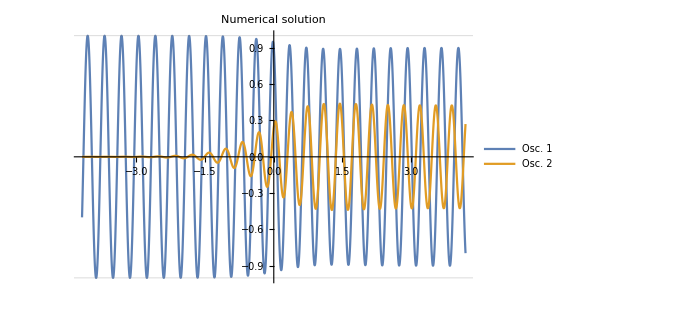

```mathematica
Plot[Evaluate[Re[{vx[t]}]/.solNumSingleOsc1Const],smalldomain,PlotRange->All,GridLines->grid[1],
PlotLabel->"Numerical solution",
PlotLegends->{"Osc. 1","Osc. 2"(*,"Osc. 3"*)},ImageSize->500]
```

## Numerical order-by-order solutions

We want now to solve numerically the order-by-order perturbative equations, so we can compare with the analytical solution, and also go up to any order we want to see if the higher order corrections help approach the full solution.

Obs: This code requires to have run the “Perturbative expansion of the EOMs and general solutions” header.

The equations we want to solve were:

#### Recall: Perturbative EOMs order by order

```mathematica
Print[]
For[roundorder=0,roundorder≤orderPrt,roundorder++,{
For[n=roundorder,n≥0,n--,{
n=0;(*New for single-parameter expansion*)
l=roundorder-n,

(*If[ϵ^n==1,*)

If[κ^l==1,{
Print["Order 0:"],
Print[]
},
False,{
Print["Order ",κ^l,":"],
Print[]
}],

(*False,
If[κ^l==1,{
Print["Order ",ϵ^n,":"],
Print[]
},
False,{
Print["Order ",ϵ^n," ",κ^l,":"]
}]
],*)

For[i=1,i<=dim,i++,{
Print["Oscillator ",i,":"],

Print["eomPert[",(*n,",",*)l,"][",i,"][t] = "],
Print[eomPert[(*n,*)l][i][t]," = 0"],
Print[]
}]
}]
}]
```

Order 0:

Oscillator 1:

eomPert[0][1][t] =

x[0][1]''[t]+T^2 (Ω[1][t])^2 x[0][1][t] = 0

Oscillator 2:

eomPert[0][2][t] =

x[0][2]''[t]+T^2 (Ω[2][t])^2 x[0][2][t] = 0

Order κ:

Oscillator 1:

eomPert[1][1][t] =

x[1][1]''[t]+T^2 kc[t] x[0][1][t]-T^2 kc[t] x[0][2][t]+T^2 (Ω[1][t])^2 x[1][1][t] = 0

Oscillator 2:

eomPert[1][2][t] =

x[1][2]''[t]-T^2 kc[t] x[0][1][t]+T^2 kc[t] x[0][2][t]+T^2 (Ω[2][t])^2 x[1][2][t] = 0

Order κ^2:

Oscillator 1:

eomPert[2][1][t] =

x[2][1]''[t]+T^2 kc[t] x[1][1][t]-T^2 kc[t] x[1][2][t]+T^2 (Ω[1][t])^2 x[2][1][t] = 0

Oscillator 2:

eomPert[2][2][t] =

x[2][2]''[t]-T^2 kc[t] x[1][1][t]+T^2 kc[t] x[1][2][t]+T^2 (Ω[2][t])^2 x[2][2][t] = 0

#### Order by order numerical solutions

```mathematica
solCorrNumOrdersSingleOsc1Const={};
l=0;
For[i=1,i<=dim,i++,{

intNumOrdersSingleOsc1Const[l][i]=NDSolve[{
eomPert[l][i][t]==0,
x[l][i][ti]==icSolSingleOsc1[[i]],
x[l][i]'[ti]==icDerivStill1[[i]]}/.freqconst/.couplspec/.param/.A[1]->1/.T->1/.solCorrNumOrdersSingleOsc1Const,x[l][i][t],{t,-tmax,tmax}]//Flatten,

xCorrNumSingleOsc1Const[l][i][t_]=x[l][i][t]/.intNumOrdersSingleOsc1Const[l][i],

Print[eomPert[l][i][t]==0],
Print[intNumOrdersSingleOsc1Const[l][i]],

AppendTo[solCorrNumOrdersSingleOsc1Const,intNumOrdersSingleOsc1Const[l][i][[1]]]//Flatten
}]
```

x[0][1]''[t]+T^2 (Ω[1][t])^2 x[0][1][t]==0

{x[0][1][t]→InterpolatingFunction[{{-100., 100.}}, <>][t]}

x[0][2]''[t]+T^2 (Ω[2][t])^2 x[0][2][t]==0

{x[0][2][t]→InterpolatingFunction[…][t]}

```mathematica
For[l=1,l<=orderPrt,l++,{
For[i=1,i<=dim,i++,{

intNumOrdersSingleOsc1Const[l][i]=NDSolve[{
eomPert[l][i][t]==0,
x[l][i][ti]==0,
x[l][i]'[ti]==0}/.freqconst/.couplspec/.param/.A[1]->1/.T->1/.solCorrNumOrdersSingleOsc1Const,x[l][i][t],{t,-tmax,tmax}]//Flatten,

xCorrNumSingleOsc1Const[l][i][t_]=x[l][i][t]/.intNumOrdersSingleOsc1Const[l][i],

Print[eomPert[l][i][t]==0/.freqconst/.couplspec],
Print[intNumOrdersSingleOsc1Const[l][i]],

AppendTo[solCorrNumOrdersSingleOsc1Const,intNumOrdersSingleOsc1Const[l][i][[1]]]//Flatten
}]
}]
```

x[1][1]''[t]+T^2 (Sech[t/τ[c]]^2 α[c]^2+ω[c]^2) x[0][1][t]-T^2 (Sech[t/τ[c]]^2 α[c]^2+ω[c]^2) x[0][2][t]+T^2 ω[1]^2 x[1][1][t]==0

{x[1][1][t]→InterpolatingFunction[{{-100., 100.}}, <>][t]}

x[1][2]''[t]-T^2 (Sech[t/τ[c]]^2 α[c]^2+ω[c]^2) x[0][1][t]+T^2 (Sech[t/τ[c]]^2 α[c]^2+ω[c]^2) x[0][2][t]+T^2 ω[2]^2 x[1][2][t]==0

{x[1][2][t]→InterpolatingFunction[{{-100., 100.}}, <>][t]}

x[2][1]''[t]+T^2 (Sech[t/τ[c]]^2 α[c]^2+ω[c]^2) x[1][1][t]-T^2 (Sech[t/τ[c]]^2 α[c]^2+ω[c]^2) x[1][2][t]+T^2 ω[1]^2 x[2][1][t]==0

{x[2][1][t]→InterpolatingFunction[{{-100., 100.}}, <>][t]}

x[2][2]''[t]-T^2 (Sech[t/τ[c]]^2 α[c]^2+ω[c]^2) x[1][1][t]+T^2 (Sech[t/τ[c]]^2 α[c]^2+ω[c]^2) x[1][2][t]+T^2 ω[2]^2 x[2][2][t]==0

{x[2][2][t]→InterpolatingFunction[{{-100., 100.}}, <>][t]}

#### Final solutions as replacement rules

```mathematica
solNumOrdersSingleOsc1Const=Normal[{
x[1][t]->xPert[1][t],
x[2][t]->xPert[2][t](*,
x[3][t]->xPert[3][t]*)
}]/.κ->1/.solCorrNumOrdersSingleOsc1Const
```

{x[1][t]→InterpolatingFunction[{{-100., 100.}}, <>][t]+InterpolatingFunction[{{-100., 100.}}, <>][t]+InterpolatingFunction[{{-100., 100.}}, <>][t],x[2][t]→InterpolatingFunction[{{-100., 100.}}, <>][t]+InterpolatingFunction[{{-100., 100.}}, <>][t]+InterpolatingFunction[…][t]}

#### Plot

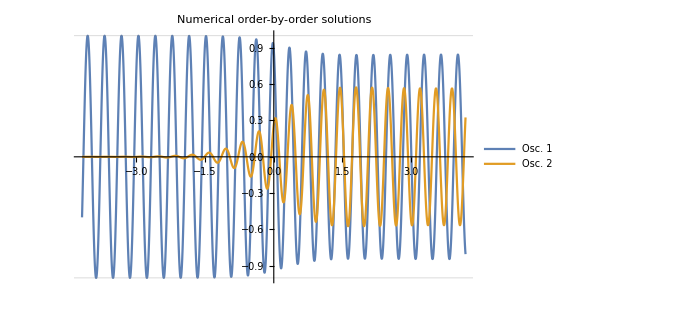

```mathematica
Plot[Evaluate[Re[{vx[t]}]/.solNumOrdersSingleOsc1Const],smalldomain,PlotRange->All,GridLines->grid[1],
PlotLabel->"Numerical order-by-order solutions",
PlotLegends->{"Osc. 1","Osc. 2"(*,"Osc. 3"*)},ImageSize->500]
```

#### Solutions up to each order

```mathematica
ClearAll[l]
```

```mathematica
xPertUpto[l_][j_][t_]=xPert[j][t]+O[κ]^(l+1)
```

κ^(1+l) O[κ]^0+(x[0][j][t]+x[1][j][t] κ+x[2][j][t] κ^2+O[κ]^3)

```mathematica
resultNumOrderbyOrderSingleOsc1Const={};
For[l=0,l<=orderPrt,l++,
For[i=1,i<=dim,i++,
AppendTo[resultNumOrderbyOrderSingleOsc1Const,
Normal[xPertUpto[l][i][t]]/.κ->1/.solCorrNumOrdersSingleOsc1Const]
]
]
```

#### Plot up to each order

```mathematica
styleorders={};
For[l=0,l<=orderPrt,l++,
For[i=1,i<=dim,i++,AppendTo[styleorders,Dashing[{0.002+l*0.006,0.004+l*0.004}]]]
]
```

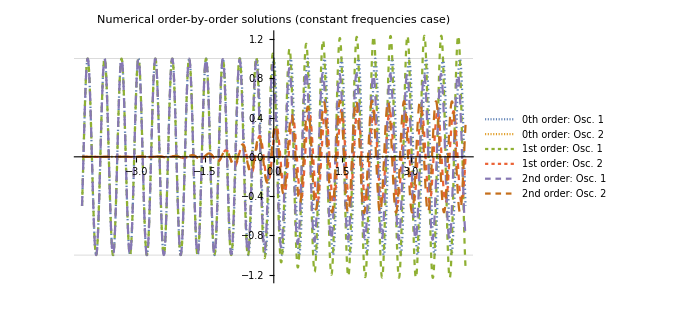

```mathematica
Plot[Evaluate[Re[resultNumOrderbyOrderSingleOsc1Const]],smalldomain,PlotRange->All,GridLines->grid[1],PlotStyle->styleorders,
PlotLabel->"Numerical order-by-order solutions
(constant frequencies case)",
PlotLegends->{legendOrders},ImageSize->500]
```

## Numerical-parametric solutions

#### Simpler parameter nomenclature

```mathematica
simplerParams={ω[1]->ω1,ω[2]->ω2,ω[c]->ωc,α[1]->α1,α[2]->α2,α[c]->αc,τ[1]->τ1,τ[2]->τ2,τ[c]->τc};
```

#### Full equations

```mathematica
eom[1][t]/.freqconst/.couplspec/.simplerParams/.T->1
```

ω1^2 x[1][t]+(ωc^2+αc^2 Sech[t/τc]^2) x[1][t]-(ωc^2+αc^2 Sech[t/τc]^2) x[2][t]+x[1]''[t]

```mathematica
paramsolNum=ParametricNDSolve[{
eom[1][t]==0,eom[2][t]==0,
x[1][ti]==icSolSingleOsc1[[1]],x[1]'[ti]==icDerivStill1[[1]],
x[2][ti]==icSolSingleOsc1[[2]],x[2]'[ti]==icDerivStill1[[2]]
}/.freqconst/.couplspec/.simplerParams/.A[1]->1/.T->1,{x[1],x[2]},{t,-tmax,tmax},
{ω1,ω2,ωc,αc,τc}]
```

{x[1]→ParametricFunction[<>],x[2]→ParametricFunction[<>]}

#### Order-by-order perturbative solutions

```mathematica
eomPert[1][1][t]/.freqconst/.couplspec/.simplerParams/.T->1
```

x[1][1]''[t]+(ωc^2+αc^2 Sech[t/τc]^2) x[0][1][t]-(ωc^2+αc^2 Sech[t/τc]^2) x[0][2][t]+ω1^2 x[1][1][t]

```mathematica
paramsolPertNum=ParametricNDSolve[{
eomPert[0][1][t]==0,eomPert[0][2][t]==0,
x[0][1][ti]==icSolSingleOsc1[[1]],x[0][1]'[ti]==icDerivStill1[[1]],
x[0][2][ti]==icSolSingleOsc1[[2]],x[0][2]'[ti]==icDerivStill1[[2]],
eomPert[1][1][t]==0,eomPert[1][2][t]==0,
x[1][1][ti]==0,x[1][1]'[ti]==0,
x[1][2][ti]==0,x[1][2]'[ti]==0,
eomPert[2][1][t]==0,eomPert[2][2][t]==0,
x[2][1][ti]==0,x[2][1]'[ti]==0,
x[2][2][ti]==0,x[2][2]'[ti]==0
}/.freqconst/.couplspec/.simplerParams/.A[1]->1/.T->1,{x[0][1],x[0][2],x[1][1],x[1][2],x[2][1],x[2][2]},{t,-tmax,tmax},
{ω1,ω2,ωc,αc,τc}]
```

{x[0][1]→ParametricFunction[<>],x[0][2]→ParametricFunction[<>],x[1][1]→ParametricFunction[<>],x[1][2]→ParametricFunction[<>],x[2][1]→ParametricFunction[<>],x[2][2]→ParametricFunction[<>]}

## Perturbative solution

### Integrating the perturbative solutions

#### Display of the formal perturbative solutions for the chosen coupling and frequencies

(i.e. the formal integrals with k(t) and the ω(t)’s substituted.)

```mathematica
For[roundorder=0,roundorder≤orderPrt,roundorder++,{
For[n=roundorder,n≥0,n--,{
n=0;(*New for single-parameter expansion*)
l=roundorder-n,
For[i=1,i<=dim,i++,{
(*If[ϵ^n==1,*)
If[κ^l==1,{
Print["Order 0, oscillator ",i,":"]
},
False,{
Print["Order ",κ^l,", oscillator ",i,":"]
}],
(*False,
If[κ^l==1,{
Print["Order ",ϵ^n,", oscillator ",i,":"]
},
False,{
Print["Order ",ϵ^n," ",κ^l,", oscillator ",i,":"]
}]],*)
(* All these loops are just to print it right, the important part is: *)

Print[intPertSingleOsc1[(*n,*)l][i]/.couplspec],
Print[]
}]
}]
}]
```

Order 0, oscillator 1:

{x[0][1][t]→(ⅇ^(-ⅈ (4 π+t) T ω[1]) A[1])/(√T)}

Order 0, oscillator 2:

{x[0][2][t]→0}

Order κ, oscillator 1:

{x[1][1][t]→Sin[t T ω[1]] -(ⅇ^(-ⅈ T (4 π+t_1) ω[1]) √T A[1] Cos[T t_1 ω[1]] (Sech[t_1/τ[c]]^2 α[c]^2+ω[c]^2))/ω[1]t_1-4 πt+Cos[t T ω[1]] (ⅇ^(-ⅈ T (4 π+t_1) ω[1]) √T A[1] Sin[T t_1 ω[1]] (Sech[t_1/τ[c]]^2 α[c]^2+ω[c]^2))/ω[1]t_1-4 πt}

Order κ, oscillator 2:

{x[1][2][t]→Sin[t T ω[2]] (ⅇ^(-ⅈ T (4 π+t_1) ω[1]) √T A[1] Cos[T t_1 ω[2]] (Sech[t_1/τ[c]]^2 α[c]^2+ω[c]^2))/ω[2]t_1-4 πt+Cos[t T ω[2]] -(ⅇ^(-ⅈ T (4 π+t_1) ω[1]) √T A[1] Sin[T t_1 ω[2]] (Sech[t_1/τ[c]]^2 α[c]^2+ω[c]^2))/ω[2]t_1-4 πt}

Order κ^2, oscillator 1:

{x[2][1][t]→Sin[t T ω[1]] -1/ω[1]T Cos[T t_2 ω[1]] (Sech[t_2/τ[c]]^2 α[c]^2+ω[c]^2) (Sin[T t_2 ω[1]] -(ⅇ^(-ⅈ T (4 π+t_2_1) ω[1]) √T A[1] Cos[T t_2_1 ω[1]] (Sech[t_2_1/τ[c]]^2 α[c]^2+ω[c]^2))/ω[1]t_2_1-4 πt_2+Cos[T t_2 ω[1]] (ⅇ^(-ⅈ T (4 π+t_2_1) ω[1]) √T A[1] Sin[T t_2_1 ω[1]] (Sech[t_2_1/τ[c]]^2 α[c]^2+ω[c]^2))/ω[1]t_2_1-4 πt_2-Sin[T t_2 ω[2]] (ⅇ^(-ⅈ T (4 π+t_2_1) ω[1]) √T A[1] Cos[T t_2_1 ω[2]] (Sech[t_2_1/τ[c]]^2 α[c]^2+ω[c]^2))/ω[2]t_2_1-4 πt_2-Cos[T t_2 ω[2]] -(ⅇ^(-ⅈ T (4 π+t_2_1) ω[1]) √T A[1] Sin[T t_2_1 ω[2]] (Sech[t_2_1/τ[c]]^2 α[c]^2+ω[c]^2))/ω[2]t_2_1-4 πt_2)t_2-4 πt+Cos[t T ω[1]] 1/ω[1]T Sin[T t_2 ω[1]] (Sech[t_2/τ[c]]^2 α[c]^2+ω[c]^2) (Sin[T t_2 ω[1]] -(ⅇ^(-ⅈ T (4 π+t_2_1) ω[1]) √T A[1] Cos[T t_2_1 ω[1]] (Sech[t_2_1/τ[c]]^2 α[c]^2+ω[c]^2))/ω[1]t_2_1-4 πt_2+Cos[T t_2 ω[1]] (ⅇ^(-ⅈ T (4 π+t_2_1) ω[1]) √T A[1] Sin[T t_2_1 ω[1]] (Sech[t_2_1/τ[c]]^2 α[c]^2+ω[c]^2))/ω[1]t_2_1-4 πt_2-Sin[T t_2 ω[2]] (ⅇ^(-ⅈ T (4 π+t_2_1) ω[1]) √T A[1] Cos[T t_2_1 ω[2]] (Sech[t_2_1/τ[c]]^2 α[c]^2+ω[c]^2))/ω[2]t_2_1-4 πt_2-Cos[T t_2 ω[2]] -(ⅇ^(-ⅈ T (4 π+t_2_1) ω[1]) √T A[1] Sin[T t_2_1 ω[2]] (Sech[t_2_1/τ[c]]^2 α[c]^2+ω[c]^2))/ω[2]t_2_1-4 πt_2)t_2-4 πt}

Order κ^2, oscillator 2:

{x[2][2][t]→Sin[t T ω[2]] 1/ω[2]T Cos[T t_2 ω[2]] (Sech[t_2/τ[c]]^2 α[c]^2+ω[c]^2) (Sin[T t_2 ω[1]] -(ⅇ^(-ⅈ T (4 π+t_2_1) ω[1]) √T A[1] Cos[T t_2_1 ω[1]] (Sech[t_2_1/τ[c]]^2 α[c]^2+ω[c]^2))/ω[1]t_2_1-4 πt_2+Cos[T t_2 ω[1]] (ⅇ^(-ⅈ T (4 π+t_2_1) ω[1]) √T A[1] Sin[T t_2_1 ω[1]] (Sech[t_2_1/τ[c]]^2 α[c]^2+ω[c]^2))/ω[1]t_2_1-4 πt_2-Sin[T t_2 ω[2]] (ⅇ^(-ⅈ T (4 π+t_2_1) ω[1]) √T A[1] Cos[T t_2_1 ω[2]] (Sech[t_2_1/τ[c]]^2 α[c]^2+ω[c]^2))/ω[2]t_2_1-4 πt_2-Cos[T t_2 ω[2]] -(ⅇ^(-ⅈ T (4 π+t_2_1) ω[1]) √T A[1] Sin[T t_2_1 ω[2]] (Sech[t_2_1/τ[c]]^2 α[c]^2+ω[c]^2))/ω[2]t_2_1-4 πt_2)t_2-4 πt+Cos[t T ω[2]] 1/ω[2]T Sin[T t_2 ω[2]] (Sech[t_2/τ[c]]^2 α[c]^2+ω[c]^2) (-Sin[T t_2 ω[1]] -(ⅇ^(-ⅈ T (4 π+t_2_1) ω[1]) √T A[1] Cos[T t_2_1 ω[1]] (Sech[t_2_1/τ[c]]^2 α[c]^2+ω[c]^2))/ω[1]t_2_1-4 πt_2-Cos[T t_2 ω[1]] (ⅇ^(-ⅈ T (4 π+t_2_1) ω[1]) √T A[1] Sin[T t_2_1 ω[1]] (Sech[t_2_1/τ[c]]^2 α[c]^2+ω[c]^2))/ω[1]t_2_1-4 πt_2+Sin[T t_2 ω[2]] (ⅇ^(-ⅈ T (4 π+t_2_1) ω[1]) √T A[1] Cos[T t_2_1 ω[2]] (Sech[t_2_1/τ[c]]^2 α[c]^2+ω[c]^2))/ω[2]t_2_1-4 πt_2+Cos[T t_2 ω[2]] -(ⅇ^(-ⅈ T (4 π+t_2_1) ω[1]) √T A[1] Sin[T t_2_1 ω[2]] (Sech[t_2_1/τ[c]]^2 α[c]^2+ω[c]^2))/ω[2]t_2_1-4 πt_2)t_2-4 πt}

#### Truncating the perturbative order

```mathematica
orderPrt=1;
```

#### Assumptions to compute the integrals

Minimal assumptions for the integrals to compute: {t>0,t__∈ℝ,τ[_]>0}

```mathematica
AppendTo[$Assumptions,Subscript[t, _]∈Reals];
```

#### Corrections’ functions

```mathematica
solCorrPertEvalSingleOsc1All={};
solCorrPertEvalSingleOsc1[(*n_,*)l_][j_]:=x[(*n,*)l][j]:>Function[t,xCorrEvalSingleOsc1[(*n,*)l][j][t](*/.t->s*)];
```

#### Integrals: analytical computation ↪︎ SWITCHED OFF (~ 12 minutes to compute)

```mathematica
(*For[roundorder=0,roundorder≤orderPrt,roundorder++,{
For[n=roundorder,n≥0,n--,{
n=0;(*New for single-parameter expansion*)
l=roundorder-n,
For[i=1,i<=dim,i++,{
(*If[ϵ^n==1,*)
If[κ^l==1,{
Print["Order 0, oscillator ",i,":"]
},
False,{
Print["Order ",κ^l,", oscillator ",i,":"]
}],
(*False,
If[κ^l==1,{
Print["Order ",ϵ^n,", oscillator ",i,":"]
},
False,{
Print["Order ",ϵ^n," ",κ^l,", oscillator ",i,":"]
}]],*)
(* All these loops are just to print it right, the important part is: *)

intPertEvalSingleOsc1[(*n,*)l][i]=Activate[intPertSingleOsc1[(*n,*)l][i]/.couplspec,Unevaluated[Integrate]]//AbsoluteTiming,

xCorrEvalSingleOsc1[(*n,*)l][i][t_]=x[(*n,*)l][i][t]/.intPertEvalSingleOsc1[(*n,*)l][i][[2]],

Print[intPertEvalSingleOsc1[(*n,*)l][i]],
Print[],

AppendTo[solCorrPertEvalSingleOsc1All,solCorrPertEvalSingleOsc1[(*n,*)l][i]]
}]
}]
}]*)
```

### Integrals: already computed, just evaluations

#### Computed integrals: The original printing

Order 0, oscillator 1:

{0.000038,{x[0][1][t]→(ⅇ^(-ⅈ (4 π+t) T ω[1]) A[1])/(√T)}}

Order 0, oscillator 2:

{8.×10^-6,{x[0][2][t]→0}}

Order κ, oscillator 1:

{203.363,{x[1][1][t]→Cos[t T ω[1]] (1/(2 ω[1] (1+T^2 τ[c]^2 ω[1]^2))ⅇ^(-4 ⅈ (2 π+t) T ω[1]) √T A[1] α[c]^2 τ[c] (ⅈ (ⅇ^(2 ⅈ (2 π+t) T ω[1]) Hypergeometric2F1[1,-ⅈ T τ[c] ω[1],1-ⅈ T τ[c] ω[1],-ⅇ^((2 t)/τ[c])]+ⅇ^(4 ⅈ (3 π+t) T ω[1]) Hypergeometric2F1[1,ⅈ T τ[c] ω[1],1+ⅈ T τ[c] ω[1],-ⅇ^((8 π)/τ[c])]-ⅇ^(4 ⅈ (π+t) T ω[1]) Tanh[(4 π)/τ[c]]+ⅇ^(4 ⅈ (3 π+t) T ω[1]) Tanh[(4 π)/τ[c]]-ⅇ^(4 ⅈ (π+t) T ω[1]) Tanh[t/τ[c]]+ⅇ^(2 ⅈ (2 π+t) T ω[1]) Tanh[t/τ[c]])+T (-2 ⅈ ⅇ^(4 ⅈ (π+t) T ω[1]) π Csch[π T τ[c] ω[1]]-ⅇ^((2 t)/τ[c]+2 ⅈ (2 π+t) T ω[1]) Hypergeometric2F1[1,1-ⅈ T τ[c] ω[1],2-ⅈ T τ[c] ω[1],-ⅇ^((2 t)/τ[c])]+ⅇ^((8 π)/τ[c]+4 ⅈ (3 π+t) T ω[1]) Hypergeometric2F1[1,1+ⅈ T τ[c] ω[1],2+ⅈ T τ[c] ω[1],-ⅇ^((8 π)/τ[c])]) τ[c] ω[1]+ⅈ T^2 (ⅇ^(2 ⅈ (2 π+t) T ω[1]) Hypergeometric2F1[1,-ⅈ T τ[c] ω[1],1-ⅈ T τ[c] ω[1],-ⅇ^((2 t)/τ[c])]+ⅇ^(4 ⅈ (3 π+t) T ω[1]) Hypergeometric2F1[1,ⅈ T τ[c] ω[1],1+ⅈ T τ[c] ω[1],-ⅇ^((8 π)/τ[c])]-ⅇ^((2 t)/τ[c]+2 ⅈ (2 π+t) T ω[1]) Hypergeometric2F1[1,1-ⅈ T τ[c] ω[1],2-ⅈ T τ[c] ω[1],-ⅇ^((2 t)/τ[c])]-ⅇ^((8 π)/τ[c]+4 ⅈ (3 π+t) T ω[1]) Hypergeometric2F1[1,1+ⅈ T τ[c] ω[1],2+ⅈ T τ[c] ω[1],-ⅇ^((8 π)/τ[c])]-ⅇ^(4 ⅈ (π+t) T ω[1]) Tanh[(4 π)/τ[c]]+ⅇ^(4 ⅈ (3 π+t) T ω[1]) Tanh[(4 π)/τ[c]]-ⅇ^(4 ⅈ (π+t) T ω[1]) Tanh[t/τ[c]]+ⅇ^(2 ⅈ (2 π+t) T ω[1]) Tanh[t/τ[c]]) τ[c]^2 ω[1]^2-2 ⅈ ⅇ^(4 ⅈ (π+t) T ω[1]) π T^3 Csch[π T τ[c] ω[1]] τ[c]^3 ω[1]^3)+(ⅇ^(-2 ⅈ (2 π+t) T ω[1]) A[1] (-1+ⅇ^(2 ⅈ (4 π+t) T ω[1])-2 ⅈ ⅇ^(2 ⅈ t T ω[1]) (4 π+t) T ω[1]) ω[c]^2)/(4 √T ω[1]^2))+Sin[t T ω[1]] (-1/ω[1]√T A[1] α[c]^2 (-1/2 ⅇ^(-4 ⅈ π T ω[1]) π T Coth[1/2 π T τ[c] ω[1]] τ[c]^2 ω[1]+1/2 ⅇ^(-4 ⅈ π T ω[1]) π T Tanh[1/2 π T τ[c] ω[1]] τ[c]^2 ω[1]-1/(-4+4 ⅈ T τ[c] ω[1])2 ⅇ^(-2 ⅈ (2 π+t) T ω[1]) (Hypergeometric2F1[1,-ⅈ T τ[c] ω[1],1-ⅈ T τ[c] ω[1],-ⅇ^((2 t)/τ[c])]+(1+ⅇ^(2 ⅈ t T ω[1])) Tanh[t/τ[c]]) τ[c]+(2 ⅈ ⅇ^(-2 ⅈ (2 π+t) T ω[1]) T Hypergeometric2F1[1,-ⅈ T τ[c] ω[1],1-ⅈ T τ[c] ω[1],-ⅇ^((2 t)/τ[c])] τ[c]^2 ω[1])/(-4+4 ⅈ T τ[c] ω[1])-(2 ⅈ ⅇ^((2 t)/τ[c]-4 ⅈ π T ω[1]-2 ⅈ t T ω[1]) T Hypergeometric2F1[1,1-ⅈ T τ[c] ω[1],2-ⅈ T τ[c] ω[1],-ⅇ^((2 t)/τ[c])] τ[c]^2 ω[1])/(-4+4 ⅈ T τ[c] ω[1])+(2 ⅈ ⅇ^(-4 ⅈ π T ω[1]) T Tanh[t/τ[c]] τ[c]^2 ω[1])/(-4+4 ⅈ T τ[c] ω[1])+(2 ⅈ ⅇ^(-2 ⅈ (2 π+t) T ω[1]) T Tanh[t/τ[c]] τ[c]^2 ω[1])/(-4+4 ⅈ T τ[c] ω[1])-1/(2 (-ⅈ+T τ[c] ω[1]))ⅈ ⅇ^(-4 ⅈ π T ω[1]) (ⅇ^(8 ⅈ π T ω[1]) Hypergeometric2F1[1,ⅈ T τ[c] ω[1],1+ⅈ T τ[c] ω[1],-ⅇ^((8 π)/τ[c])]+(1+ⅇ^(8 ⅈ π T ω[1])) Tanh[(4 π)/τ[c]]) τ[c]+(ⅇ^(4 ⅈ π T ω[1]) T Hypergeometric2F1[1,ⅈ T τ[c] ω[1],1+ⅈ T τ[c] ω[1],-ⅇ^((8 π)/τ[c])] τ[c]^2 ω[1])/(2 (-ⅈ+T τ[c] ω[1]))-(ⅇ^((8 π)/τ[c]+4 ⅈ π T ω[1]) T Hypergeometric2F1[1,1+ⅈ T τ[c] ω[1],2+ⅈ T τ[c] ω[1],-ⅇ^((8 π)/τ[c])] τ[c]^2 ω[1])/(2 (-ⅈ+T τ[c] ω[1]))+(ⅇ^(-4 ⅈ π T ω[1]) T Tanh[(4 π)/τ[c]] τ[c]^2 ω[1])/(2 (-ⅈ+T τ[c] ω[1]))+(ⅇ^(4 ⅈ π T ω[1]) T Tanh[(4 π)/τ[c]] τ[c]^2 ω[1])/(2 (-ⅈ+T τ[c] ω[1])))+(ⅈ ⅇ^(-2 ⅈ (2 π+t) T ω[1]) A[1] (-1+ⅇ^(2 ⅈ (4 π+t) T ω[1])+2 ⅈ ⅇ^(2 ⅈ t T ω[1]) (4 π+t) T ω[1]) ω[c]^2)/(4 √T ω[1]^2))}}

Order κ, oscillator 2:

{484.146,{x[1][2][t]→Cos[t T ω[2]] (-1/ω[2]√T A[1] α[c]^2 (1/4 ⅈ ⅇ^(-4 ⅈ π T ω[1]) π T Coth[1/4 π T τ[c] ω[1]-1/4 π T τ[c] ω[2]] τ[c]^2 (ω[1]-ω[2])-1/4 ⅈ ⅇ^(-4 ⅈ π T ω[1]) π T Tanh[1/4 π T τ[c] ω[1]-1/4 π T τ[c] ω[2]] τ[c]^2 (ω[1]-ω[2])-1/4 ⅈ ⅇ^(-4 ⅈ π T ω[1]) π T Coth[1/4 π T τ[c] ω[1]+1/4 π T τ[c] ω[2]] τ[c]^2 (ω[1]+ω[2])+1/4 ⅈ ⅇ^(-4 ⅈ π T ω[1]) π T Tanh[1/4 π T τ[c] ω[1]+1/4 π T τ[c] ω[2]] τ[c]^2 (ω[1]+ω[2])-(ⅇ^(-4 ⅈ π T ω[1]) T τ[c]^2 (ω[1]+ω[2]))/(4 (-1/4 ⅈ T τ[c] ω[1]-1/4 ⅈ T τ[c] ω[2]))-(ⅇ^(-4 ⅈ π T ω[1]) T τ[c]^2 (ω[1]-ω[2]))/(4 (1/4 ⅈ T τ[c] ω[1]-1/4 ⅈ T τ[c] ω[2]))+(2 ⅈ ⅇ^(-4 ⅈ π T ω[2]) Hypergeometric2F1[1,1/2 ⅈ T τ[c] (ω[1]-ω[2]),1+1/2 ⅈ T τ[c] (ω[1]-ω[2]),-ⅇ^((8 π)/τ[c])] τ[c])/((-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(2 ⅈ ⅇ^(4 ⅈ π T ω[2]) Hypergeometric2F1[1,1/2 ⅈ T τ[c] (ω[1]+ω[2]),1+1/2 ⅈ T τ[c] (ω[1]+ω[2]),-ⅇ^((8 π)/τ[c])] τ[c])/((-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(2 ⅈ ⅇ^(-4 ⅈ π T ω[2]) Tanh[(4 π)/τ[c]] τ[c])/((-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(2 ⅈ ⅇ^(4 ⅈ π T ω[2]) Tanh[(4 π)/τ[c]] τ[c])/((-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(ⅇ^((8 π)/τ[c]-4 ⅈ π T ω[2]) T Hypergeometric2F1[1,1+1/2 ⅈ T τ[c] (ω[1]-ω[2]),2+1/2 ⅈ T τ[c] (ω[1]-ω[2]),-ⅇ^((8 π)/τ[c])] τ[c]^2 ω[1])/((-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(2 ⅇ^(-4 ⅈ π T ω[2]) T Hypergeometric2F1[1,1/2 ⅈ T τ[c] (ω[1]-ω[2]),1+1/2 ⅈ T τ[c] (ω[1]-ω[2]),-ⅇ^((8 π)/τ[c])] τ[c]^2 ω[1])/((-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(2 ⅇ^(4 ⅈ π T ω[2]) T Hypergeometric2F1[1,1/2 ⅈ T τ[c] (ω[1]+ω[2]),1+1/2 ⅈ T τ[c] (ω[1]+ω[2]),-ⅇ^((8 π)/τ[c])] τ[c]^2 ω[1])/((-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(ⅇ^((8 π)/τ[c]+4 ⅈ π T ω[2]) T Hypergeometric2F1[1,1+1/2 ⅈ T τ[c] (ω[1]+ω[2]),2+1/2 ⅈ T τ[c] (ω[1]+ω[2]),-ⅇ^((8 π)/τ[c])] τ[c]^2 ω[1])/((-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(2 ⅇ^(-4 ⅈ π T ω[2]) T Tanh[(4 π)/τ[c]] τ[c]^2 ω[1])/((-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(2 ⅇ^(4 ⅈ π T ω[2]) T Tanh[(4 π)/τ[c]] τ[c]^2 ω[1])/((-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(ⅈ ⅇ^((8 π)/τ[c]-4 ⅈ π T ω[2]) T^2 Hypergeometric2F1[1,1+1/2 ⅈ T τ[c] (ω[1]-ω[2]),2+1/2 ⅈ T τ[c] (ω[1]-ω[2]),-ⅇ^((8 π)/τ[c])] τ[c]^3 ω[1]^2)/(2 (-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(ⅈ ⅇ^(-4 ⅈ π T ω[2]) T^2 Hypergeometric2F1[1,1/2 ⅈ T τ[c] (ω[1]-ω[2]),1+1/2 ⅈ T τ[c] (ω[1]-ω[2]),-ⅇ^((8 π)/τ[c])] τ[c]^3 ω[1]^2)/(2 (-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(ⅈ ⅇ^(4 ⅈ π T ω[2]) T^2 Hypergeometric2F1[1,1/2 ⅈ T τ[c] (ω[1]+ω[2]),1+1/2 ⅈ T τ[c] (ω[1]+ω[2]),-ⅇ^((8 π)/τ[c])] τ[c]^3 ω[1]^2)/(2 (-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(ⅈ ⅇ^((8 π)/τ[c]+4 ⅈ π T ω[2]) T^2 Hypergeometric2F1[1,1+1/2 ⅈ T τ[c] (ω[1]+ω[2]),2+1/2 ⅈ T τ[c] (ω[1]+ω[2]),-ⅇ^((8 π)/τ[c])] τ[c]^3 ω[1]^2)/(2 (-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(T^2 Sin[4 π T ω[2]] Tanh[(4 π)/τ[c]] τ[c]^3 ω[1]^2)/((-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(ⅇ^((8 π)/τ[c]-4 ⅈ π T ω[2]) T Hypergeometric2F1[1,1+1/2 ⅈ T τ[c] (ω[1]-ω[2]),2+1/2 ⅈ T τ[c] (ω[1]-ω[2]),-ⅇ^((8 π)/τ[c])] τ[c]^2 ω[2])/((-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(ⅇ^((8 π)/τ[c]+4 ⅈ π T ω[2]) T Hypergeometric2F1[1,1+1/2 ⅈ T τ[c] (ω[1]+ω[2]),2+1/2 ⅈ T τ[c] (ω[1]+ω[2]),-ⅇ^((8 π)/τ[c])] τ[c]^2 ω[2])/((-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(ⅈ ⅇ^((8 π)/τ[c]-4 ⅈ π T ω[2]) T^2 Hypergeometric2F1[1,1+1/2 ⅈ T τ[c] (ω[1]-ω[2]),2+1/2 ⅈ T τ[c] (ω[1]-ω[2]),-ⅇ^((8 π)/τ[c])] τ[c]^3 ω[2]^2)/(2 (-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(ⅈ ⅇ^(-4 ⅈ π T ω[2]) T^2 Hypergeometric2F1[1,1/2 ⅈ T τ[c] (ω[1]-ω[2]),1+1/2 ⅈ T τ[c] (ω[1]-ω[2]),-ⅇ^((8 π)/τ[c])] τ[c]^3 ω[2]^2)/(2 (-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(ⅈ ⅇ^(4 ⅈ π T ω[2]) T^2 Hypergeometric2F1[1,1/2 ⅈ T τ[c] (ω[1]+ω[2]),1+1/2 ⅈ T τ[c] (ω[1]+ω[2]),-ⅇ^((8 π)/τ[c])] τ[c]^3 ω[2]^2)/(2 (-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(ⅈ ⅇ^((8 π)/τ[c]+4 ⅈ π T ω[2]) T^2 Hypergeometric2F1[1,1+1/2 ⅈ T τ[c] (ω[1]+ω[2]),2+1/2 ⅈ T τ[c] (ω[1]+ω[2]),-ⅇ^((8 π)/τ[c])] τ[c]^3 ω[2]^2)/(2 (-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(ⅈ ⅇ^(-4 ⅈ π T ω[2]) T^2 Tanh[(4 π)/τ[c]] τ[c]^3 ω[2]^2)/(2 (-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(ⅈ ⅇ^(4 ⅈ π T ω[2]) T^2 Tanh[(4 π)/τ[c]] τ[c]^3 ω[2]^2)/(2 (-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(2 ⅈ ⅇ^(-4 ⅈ π T ω[1]-ⅈ t T ω[1]+ⅈ t T ω[2]) Hypergeometric2F1[1,-1/2 ⅈ T τ[c] (ω[1]-ω[2]),1-1/2 ⅈ T τ[c] (ω[1]-ω[2]),-ⅇ^((2 t)/τ[c])] τ[c])/((2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(2 ⅈ ⅇ^(-ⅈ T (4 π ω[1]+t (ω[1]+ω[2]))) Hypergeometric2F1[1,-1/2 ⅈ T τ[c] (ω[1]+ω[2]),1-1/2 ⅈ T τ[c] (ω[1]+ω[2]),-ⅇ^((2 t)/τ[c])] τ[c])/((2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(2 ⅈ ⅇ^(-4 ⅈ π T ω[1]-ⅈ t T ω[1]+ⅈ t T ω[2]) Tanh[t/τ[c]] τ[c])/((2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(2 ⅈ ⅇ^(-ⅈ T (4 π ω[1]+t (ω[1]+ω[2]))) Tanh[t/τ[c]] τ[c])/((2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(ⅇ^((2 t)/τ[c]-4 ⅈ π T ω[1]-ⅈ t T ω[1]+ⅈ t T ω[2]) T Hypergeometric2F1[1,1-1/2 ⅈ T τ[c] (ω[1]-ω[2]),2-1/2 ⅈ T τ[c] (ω[1]-ω[2]),-ⅇ^((2 t)/τ[c])] τ[c]^2 ω[1])/((2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(2 ⅇ^(-4 ⅈ π T ω[1]-ⅈ t T ω[1]+ⅈ t T ω[2]) T Hypergeometric2F1[1,-1/2 ⅈ T τ[c] (ω[1]-ω[2]),1-1/2 ⅈ T τ[c] (ω[1]-ω[2]),-ⅇ^((2 t)/τ[c])] τ[c]^2 ω[1])/((2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(2 ⅇ^(-ⅈ T (4 π ω[1]+t (ω[1]+ω[2]))) T Hypergeometric2F1[1,-1/2 ⅈ T τ[c] (ω[1]+ω[2]),1-1/2 ⅈ T τ[c] (ω[1]+ω[2]),-ⅇ^((2 t)/τ[c])] τ[c]^2 ω[1])/((2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(ⅇ^((2 t)/τ[c]-4 ⅈ π T ω[1]-ⅈ t T ω[1]-ⅈ t T ω[2]) T Hypergeometric2F1[1,1-1/2 ⅈ T τ[c] (ω[1]+ω[2]),2-1/2 ⅈ T τ[c] (ω[1]+ω[2]),-ⅇ^((2 t)/τ[c])] τ[c]^2 ω[1])/((2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(2 ⅇ^(-4 ⅈ π T ω[1]-ⅈ t T ω[1]+ⅈ t T ω[2]) T Tanh[t/τ[c]] τ[c]^2 ω[1])/((2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(2 ⅇ^(-ⅈ T (4 π ω[1]+t (ω[1]+ω[2]))) T Tanh[t/τ[c]] τ[c]^2 ω[1])/((2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(ⅈ ⅇ^((2 t)/τ[c]-4 ⅈ π T ω[1]-ⅈ t T ω[1]+ⅈ t T ω[2]) T^2 Hypergeometric2F1[1,1-1/2 ⅈ T τ[c] (ω[1]-ω[2]),2-1/2 ⅈ T τ[c] (ω[1]-ω[2]),-ⅇ^((2 t)/τ[c])] τ[c]^3 ω[1]^2)/(2 (2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(ⅈ ⅇ^(-4 ⅈ π T ω[1]-ⅈ t T ω[1]+ⅈ t T ω[2]) T^2 Hypergeometric2F1[1,-1/2 ⅈ T τ[c] (ω[1]-ω[2]),1-1/2 ⅈ T τ[c] (ω[1]-ω[2]),-ⅇ^((2 t)/τ[c])] τ[c]^3 ω[1]^2)/(2 (2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(ⅈ ⅇ^(-ⅈ T (4 π ω[1]+t (ω[1]+ω[2]))) T^2 Hypergeometric2F1[1,-1/2 ⅈ T τ[c] (ω[1]+ω[2]),1-1/2 ⅈ T τ[c] (ω[1]+ω[2]),-ⅇ^((2 t)/τ[c])] τ[c]^3 ω[1]^2)/(2 (2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(ⅈ ⅇ^((2 t)/τ[c]-4 ⅈ π T ω[1]-ⅈ t T ω[1]-ⅈ t T ω[2]) T^2 Hypergeometric2F1[1,1-1/2 ⅈ T τ[c] (ω[1]+ω[2]),2-1/2 ⅈ T τ[c] (ω[1]+ω[2]),-ⅇ^((2 t)/τ[c])] τ[c]^3 ω[1]^2)/(2 (2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(ⅈ ⅇ^(-4 ⅈ π T ω[1]-ⅈ t T ω[1]+ⅈ t T ω[2]) T^2 Tanh[t/τ[c]] τ[c]^3 ω[1]^2)/(2 (2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(ⅈ ⅇ^(-ⅈ T (4 π ω[1]+t (ω[1]+ω[2]))) T^2 Tanh[t/τ[c]] τ[c]^3 ω[1]^2)/(2 (2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(ⅇ^((2 t)/τ[c]-4 ⅈ π T ω[1]-ⅈ t T ω[1]+ⅈ t T ω[2]) T Hypergeometric2F1[1,1-1/2 ⅈ T τ[c] (ω[1]-ω[2]),2-1/2 ⅈ T τ[c] (ω[1]-ω[2]),-ⅇ^((2 t)/τ[c])] τ[c]^2 ω[2])/((2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(ⅇ^((2 t)/τ[c]-4 ⅈ π T ω[1]-ⅈ t T ω[1]-ⅈ t T ω[2]) T Hypergeometric2F1[1,1-1/2 ⅈ T τ[c] (ω[1]+ω[2]),2-1/2 ⅈ T τ[c] (ω[1]+ω[2]),-ⅇ^((2 t)/τ[c])] τ[c]^2 ω[2])/((2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(ⅈ ⅇ^((2 t)/τ[c]-4 ⅈ π T ω[1]-ⅈ t T ω[1]+ⅈ t T ω[2]) T^2 Hypergeometric2F1[1,1-1/2 ⅈ T τ[c] (ω[1]-ω[2]),2-1/2 ⅈ T τ[c] (ω[1]-ω[2]),-ⅇ^((2 t)/τ[c])] τ[c]^3 ω[2]^2)/(2 (2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(ⅈ ⅇ^(-4 ⅈ π T ω[1]-ⅈ t T ω[1]+ⅈ t T ω[2]) T^2 Hypergeometric2F1[1,-1/2 ⅈ T τ[c] (ω[1]-ω[2]),1-1/2 ⅈ T τ[c] (ω[1]-ω[2]),-ⅇ^((2 t)/τ[c])] τ[c]^3 ω[2]^2)/(2 (2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(ⅈ ⅇ^(-ⅈ T (4 π ω[1]+t (ω[1]+ω[2]))) T^2 Hypergeometric2F1[1,-1/2 ⅈ T τ[c] (ω[1]+ω[2]),1-1/2 ⅈ T τ[c] (ω[1]+ω[2]),-ⅇ^((2 t)/τ[c])] τ[c]^3 ω[2]^2)/(2 (2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(ⅈ ⅇ^((2 t)/τ[c]-4 ⅈ π T ω[1]-ⅈ t T ω[1]-ⅈ t T ω[2]) T^2 Hypergeometric2F1[1,1-1/2 ⅈ T τ[c] (ω[1]+ω[2]),2-1/2 ⅈ T τ[c] (ω[1]+ω[2]),-ⅇ^((2 t)/τ[c])] τ[c]^3 ω[2]^2)/(2 (2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(ⅈ ⅇ^(-4 ⅈ π T ω[1]-ⅈ t T ω[1]+ⅈ t T ω[2]) T^2 Tanh[t/τ[c]] τ[c]^3 ω[2]^2)/(2 (2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(ⅈ ⅇ^(-ⅈ T (4 π ω[1]+t (ω[1]+ω[2]))) T^2 Tanh[t/τ[c]] τ[c]^3 ω[2]^2)/(2 (2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2])))-(A[1] (ⅈ Sin[4 π T ω[2]] ω[1]-Cos[4 π T ω[2]] ω[2]+ⅇ^(-ⅈ (4 π+t) T ω[1]) (ⅈ Sin[t T ω[2]] ω[1]+Cos[t T ω[2]] ω[2])) ω[c]^2)/(√T ω[2] (ω[1]^2-ω[2]^2)))+Sin[t T ω[2]] (1/ω[2]√T A[1] α[c]^2 (2 ⅇ^(-4 ⅈ π T ω[1]) τ[c]-1/4 ⅇ^(-4 ⅈ π T ω[1]) π T Coth[1/4 π T τ[c] ω[1]-1/4 π T τ[c] ω[2]] τ[c]^2 (ω[1]-ω[2])+1/4 ⅇ^(-4 ⅈ π T ω[1]) π T Tanh[1/4 π T τ[c] ω[1]-1/4 π T τ[c] ω[2]] τ[c]^2 (ω[1]-ω[2])-1/4 ⅇ^(-4 ⅈ π T ω[1]) π T Coth[1/4 π T τ[c] ω[1]+1/4 π T τ[c] ω[2]] τ[c]^2 (ω[1]+ω[2])+1/4 ⅇ^(-4 ⅈ π T ω[1]) π T Tanh[1/4 π T τ[c] ω[1]+1/4 π T τ[c] ω[2]] τ[c]^2 (ω[1]+ω[2])+(ⅈ ⅇ^(-4 ⅈ π T ω[1]) T τ[c]^2 (ω[1]+ω[2]))/(4 (-1/4 ⅈ T τ[c] ω[1]-1/4 ⅈ T τ[c] ω[2]))-(ⅈ ⅇ^(-4 ⅈ π T ω[1]) T τ[c]^2 (ω[1]-ω[2]))/(4 (1/4 ⅈ T τ[c] ω[1]-1/4 ⅈ T τ[c] ω[2]))-(2 ⅇ^(-4 ⅈ π T ω[2]) Hypergeometric2F1[1,1/2 ⅈ T τ[c] (ω[1]-ω[2]),1+1/2 ⅈ T τ[c] (ω[1]-ω[2]),-ⅇ^((8 π)/τ[c])] τ[c])/((-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(2 ⅇ^(4 ⅈ π T ω[2]) Hypergeometric2F1[1,1/2 ⅈ T τ[c] (ω[1]+ω[2]),1+1/2 ⅈ T τ[c] (ω[1]+ω[2]),-ⅇ^((8 π)/τ[c])] τ[c])/((-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(2 ⅇ^(-4 ⅈ π T ω[2]) Tanh[(4 π)/τ[c]] τ[c])/((-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(2 ⅇ^(4 ⅈ π T ω[2]) Tanh[(4 π)/τ[c]] τ[c])/((-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(ⅈ ⅇ^((8 π)/τ[c]-4 ⅈ π T ω[2]) T Hypergeometric2F1[1,1+1/2 ⅈ T τ[c] (ω[1]-ω[2]),2+1/2 ⅈ T τ[c] (ω[1]-ω[2]),-ⅇ^((8 π)/τ[c])] τ[c]^2 ω[1])/((-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(2 ⅈ ⅇ^(-4 ⅈ π T ω[2]) T Hypergeometric2F1[1,1/2 ⅈ T τ[c] (ω[1]-ω[2]),1+1/2 ⅈ T τ[c] (ω[1]-ω[2]),-ⅇ^((8 π)/τ[c])] τ[c]^2 ω[1])/((-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(2 ⅈ ⅇ^(4 ⅈ π T ω[2]) T Hypergeometric2F1[1,1/2 ⅈ T τ[c] (ω[1]+ω[2]),1+1/2 ⅈ T τ[c] (ω[1]+ω[2]),-ⅇ^((8 π)/τ[c])] τ[c]^2 ω[1])/((-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(ⅈ ⅇ^((8 π)/τ[c]+4 ⅈ π T ω[2]) T Hypergeometric2F1[1,1+1/2 ⅈ T τ[c] (ω[1]+ω[2]),2+1/2 ⅈ T τ[c] (ω[1]+ω[2]),-ⅇ^((8 π)/τ[c])] τ[c]^2 ω[1])/((-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(2 ⅈ ⅇ^(-4 ⅈ π T ω[2]) T Tanh[(4 π)/τ[c]] τ[c]^2 ω[1])/((-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(2 ⅈ ⅇ^(4 ⅈ π T ω[2]) T Tanh[(4 π)/τ[c]] τ[c]^2 ω[1])/((-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(ⅇ^((8 π)/τ[c]-4 ⅈ π T ω[2]) T^2 Hypergeometric2F1[1,1+1/2 ⅈ T τ[c] (ω[1]-ω[2]),2+1/2 ⅈ T τ[c] (ω[1]-ω[2]),-ⅇ^((8 π)/τ[c])] τ[c]^3 ω[1]^2)/(2 (-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(ⅇ^(-4 ⅈ π T ω[2]) T^2 Hypergeometric2F1[1,1/2 ⅈ T τ[c] (ω[1]-ω[2]),1+1/2 ⅈ T τ[c] (ω[1]-ω[2]),-ⅇ^((8 π)/τ[c])] τ[c]^3 ω[1]^2)/(2 (-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(ⅇ^(4 ⅈ π T ω[2]) T^2 Hypergeometric2F1[1,1/2 ⅈ T τ[c] (ω[1]+ω[2]),1+1/2 ⅈ T τ[c] (ω[1]+ω[2]),-ⅇ^((8 π)/τ[c])] τ[c]^3 ω[1]^2)/(2 (-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(ⅇ^((8 π)/τ[c]+4 ⅈ π T ω[2]) T^2 Hypergeometric2F1[1,1+1/2 ⅈ T τ[c] (ω[1]+ω[2]),2+1/2 ⅈ T τ[c] (ω[1]+ω[2]),-ⅇ^((8 π)/τ[c])] τ[c]^3 ω[1]^2)/(2 (-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(ⅇ^(-4 ⅈ π T ω[2]) T^2 Tanh[(4 π)/τ[c]] τ[c]^3 ω[1]^2)/(2 (-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(ⅇ^(4 ⅈ π T ω[2]) T^2 Tanh[(4 π)/τ[c]] τ[c]^3 ω[1]^2)/(2 (-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(ⅈ ⅇ^((8 π)/τ[c]-4 ⅈ π T ω[2]) T Hypergeometric2F1[1,1+1/2 ⅈ T τ[c] (ω[1]-ω[2]),2+1/2 ⅈ T τ[c] (ω[1]-ω[2]),-ⅇ^((8 π)/τ[c])] τ[c]^2 ω[2])/((-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(ⅈ ⅇ^((8 π)/τ[c]+4 ⅈ π T ω[2]) T Hypergeometric2F1[1,1+1/2 ⅈ T τ[c] (ω[1]+ω[2]),2+1/2 ⅈ T τ[c] (ω[1]+ω[2]),-ⅇ^((8 π)/τ[c])] τ[c]^2 ω[2])/((-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(ⅇ^((8 π)/τ[c]-4 ⅈ π T ω[2]) T^2 Hypergeometric2F1[1,1+1/2 ⅈ T τ[c] (ω[1]-ω[2]),2+1/2 ⅈ T τ[c] (ω[1]-ω[2]),-ⅇ^((8 π)/τ[c])] τ[c]^3 ω[2]^2)/(2 (-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(ⅇ^(-4 ⅈ π T ω[2]) T^2 Hypergeometric2F1[1,1/2 ⅈ T τ[c] (ω[1]-ω[2]),1+1/2 ⅈ T τ[c] (ω[1]-ω[2]),-ⅇ^((8 π)/τ[c])] τ[c]^3 ω[2]^2)/(2 (-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(ⅇ^(4 ⅈ π T ω[2]) T^2 Hypergeometric2F1[1,1/2 ⅈ T τ[c] (ω[1]+ω[2]),1+1/2 ⅈ T τ[c] (ω[1]+ω[2]),-ⅇ^((8 π)/τ[c])] τ[c]^3 ω[2]^2)/(2 (-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(ⅇ^((8 π)/τ[c]+4 ⅈ π T ω[2]) T^2 Hypergeometric2F1[1,1+1/2 ⅈ T τ[c] (ω[1]+ω[2]),2+1/2 ⅈ T τ[c] (ω[1]+ω[2]),-ⅇ^((8 π)/τ[c])] τ[c]^3 ω[2]^2)/(2 (-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(ⅇ^(-4 ⅈ π T ω[2]) T^2 Tanh[(4 π)/τ[c]] τ[c]^3 ω[2]^2)/(2 (-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(ⅇ^(4 ⅈ π T ω[2]) T^2 Tanh[(4 π)/τ[c]] τ[c]^3 ω[2]^2)/(2 (-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(2 ⅇ^(-4 ⅈ π T ω[1]-ⅈ t T ω[1]+ⅈ t T ω[2]) Hypergeometric2F1[1,-1/2 ⅈ T τ[c] (ω[1]-ω[2]),1-1/2 ⅈ T τ[c] (ω[1]-ω[2]),-ⅇ^((2 t)/τ[c])] τ[c])/((2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(2 ⅇ^(-ⅈ T (4 π ω[1]+t (ω[1]+ω[2]))) Hypergeometric2F1[1,-1/2 ⅈ T τ[c] (ω[1]+ω[2]),1-1/2 ⅈ T τ[c] (ω[1]+ω[2]),-ⅇ^((2 t)/τ[c])] τ[c])/((2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(2 ⅇ^(-4 ⅈ π T ω[1]-ⅈ t T ω[1]+ⅈ t T ω[2]) Tanh[t/τ[c]] τ[c])/((2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(2 ⅇ^(-ⅈ T (4 π ω[1]+t (ω[1]+ω[2]))) Tanh[t/τ[c]] τ[c])/((2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(ⅈ ⅇ^((2 t)/τ[c]-4 ⅈ π T ω[1]-ⅈ t T ω[1]+ⅈ t T ω[2]) T Hypergeometric2F1[1,1-1/2 ⅈ T τ[c] (ω[1]-ω[2]),2-1/2 ⅈ T τ[c] (ω[1]-ω[2]),-ⅇ^((2 t)/τ[c])] τ[c]^2 ω[1])/((2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(2 ⅈ ⅇ^(-4 ⅈ π T ω[1]-ⅈ t T ω[1]+ⅈ t T ω[2]) T Hypergeometric2F1[1,-1/2 ⅈ T τ[c] (ω[1]-ω[2]),1-1/2 ⅈ T τ[c] (ω[1]-ω[2]),-ⅇ^((2 t)/τ[c])] τ[c]^2 ω[1])/((2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(2 ⅈ ⅇ^(-ⅈ T (4 π ω[1]+t (ω[1]+ω[2]))) T Hypergeometric2F1[1,-1/2 ⅈ T τ[c] (ω[1]+ω[2]),1-1/2 ⅈ T τ[c] (ω[1]+ω[2]),-ⅇ^((2 t)/τ[c])] τ[c]^2 ω[1])/((2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(ⅈ ⅇ^((2 t)/τ[c]-4 ⅈ π T ω[1]-ⅈ t T ω[1]-ⅈ t T ω[2]) T Hypergeometric2F1[1,1-1/2 ⅈ T τ[c] (ω[1]+ω[2]),2-1/2 ⅈ T τ[c] (ω[1]+ω[2]),-ⅇ^((2 t)/τ[c])] τ[c]^2 ω[1])/((2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(2 ⅈ ⅇ^(-4 ⅈ π T ω[1]-ⅈ t T ω[1]+ⅈ t T ω[2]) T Tanh[t/τ[c]] τ[c]^2 ω[1])/((2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(2 ⅈ ⅇ^(-ⅈ T (4 π ω[1]+t (ω[1]+ω[2]))) T Tanh[t/τ[c]] τ[c]^2 ω[1])/((2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(ⅇ^((2 t)/τ[c]-4 ⅈ π T ω[1]-ⅈ t T ω[1]+ⅈ t T ω[2]) T^2 Hypergeometric2F1[1,1-1/2 ⅈ T τ[c] (ω[1]-ω[2]),2-1/2 ⅈ T τ[c] (ω[1]-ω[2]),-ⅇ^((2 t)/τ[c])] τ[c]^3 ω[1]^2)/(2 (2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(ⅇ^(-4 ⅈ π T ω[1]-ⅈ t T ω[1]+ⅈ t T ω[2]) T^2 Hypergeometric2F1[1,-1/2 ⅈ T τ[c] (ω[1]-ω[2]),1-1/2 ⅈ T τ[c] (ω[1]-ω[2]),-ⅇ^((2 t)/τ[c])] τ[c]^3 ω[1]^2)/(2 (2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(ⅇ^(-ⅈ T (4 π ω[1]+t (ω[1]+ω[2]))) T^2 Hypergeometric2F1[1,-1/2 ⅈ T τ[c] (ω[1]+ω[2]),1-1/2 ⅈ T τ[c] (ω[1]+ω[2]),-ⅇ^((2 t)/τ[c])] τ[c]^3 ω[1]^2)/(2 (2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(ⅇ^((2 t)/τ[c]-4 ⅈ π T ω[1]-ⅈ t T ω[1]-ⅈ t T ω[2]) T^2 Hypergeometric2F1[1,1-1/2 ⅈ T τ[c] (ω[1]+ω[2]),2-1/2 ⅈ T τ[c] (ω[1]+ω[2]),-ⅇ^((2 t)/τ[c])] τ[c]^3 ω[1]^2)/(2 (2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(ⅇ^(-4 ⅈ π T ω[1]-ⅈ t T ω[1]+ⅈ t T ω[2]) T^2 Tanh[t/τ[c]] τ[c]^3 ω[1]^2)/(2 (2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(ⅇ^(-ⅈ T (4 π ω[1]+t (ω[1]+ω[2]))) T^2 Tanh[t/τ[c]] τ[c]^3 ω[1]^2)/(2 (2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(ⅈ ⅇ^((2 t)/τ[c]-4 ⅈ π T ω[1]-ⅈ t T ω[1]+ⅈ t T ω[2]) T Hypergeometric2F1[1,1-1/2 ⅈ T τ[c] (ω[1]-ω[2]),2-1/2 ⅈ T τ[c] (ω[1]-ω[2]),-ⅇ^((2 t)/τ[c])] τ[c]^2 ω[2])/((2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(ⅈ ⅇ^((2 t)/τ[c]-4 ⅈ π T ω[1]-ⅈ t T ω[1]-ⅈ t T ω[2]) T Hypergeometric2F1[1,1-1/2 ⅈ T τ[c] (ω[1]+ω[2]),2-1/2 ⅈ T τ[c] (ω[1]+ω[2]),-ⅇ^((2 t)/τ[c])] τ[c]^2 ω[2])/((2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(ⅇ^((2 t)/τ[c]-4 ⅈ π T ω[1]-ⅈ t T ω[1]+ⅈ t T ω[2]) T^2 Hypergeometric2F1[1,1-1/2 ⅈ T τ[c] (ω[1]-ω[2]),2-1/2 ⅈ T τ[c] (ω[1]-ω[2]),-ⅇ^((2 t)/τ[c])] τ[c]^3 ω[2]^2)/(2 (2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(ⅇ^(-4 ⅈ π T ω[1]-ⅈ t T ω[1]+ⅈ t T ω[2]) T^2 Hypergeometric2F1[1,-1/2 ⅈ T τ[c] (ω[1]-ω[2]),1-1/2 ⅈ T τ[c] (ω[1]-ω[2]),-ⅇ^((2 t)/τ[c])] τ[c]^3 ω[2]^2)/(2 (2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(ⅇ^(-ⅈ T (4 π ω[1]+t (ω[1]+ω[2]))) T^2 Hypergeometric2F1[1,-1/2 ⅈ T τ[c] (ω[1]+ω[2]),1-1/2 ⅈ T τ[c] (ω[1]+ω[2]),-ⅇ^((2 t)/τ[c])] τ[c]^3 ω[2]^2)/(2 (2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(ⅇ^((2 t)/τ[c]-4 ⅈ π T ω[1]-ⅈ t T ω[1]-ⅈ t T ω[2]) T^2 Hypergeometric2F1[1,1-1/2 ⅈ T τ[c] (ω[1]+ω[2]),2-1/2 ⅈ T τ[c] (ω[1]+ω[2]),-ⅇ^((2 t)/τ[c])] τ[c]^3 ω[2]^2)/(2 (2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(ⅇ^(-4 ⅈ π T ω[1]-ⅈ t T ω[1]+ⅈ t T ω[2]) T^2 Tanh[t/τ[c]] τ[c]^3 ω[2]^2)/(2 (2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(ⅇ^(-ⅈ T (4 π ω[1]+t (ω[1]+ω[2]))) T^2 Tanh[t/τ[c]] τ[c]^3 ω[2]^2)/(2 (2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2])))+1/(√T (-ω[1]^2 ω[2]+ω[2]^3))ⅇ^(-ⅈ (4 π+t) T ω[1]) A[1] (-ⅈ Cos[t T ω[2]] ω[1]+Sin[t T ω[2]] ω[2]+ⅇ^(ⅈ (4 π+t) T ω[1]) (ⅈ Cos[4 π T ω[2]] ω[1]+Sin[4 π T ω[2]] ω[2])) ω[c]^2)}}

#### Computed integrals: Assigning the results

```mathematica
intPertEvalSingleOsc1[(*n,*)0][1]={0.000038,{x[0][1][t]->(ⅇ^(-ⅈ (4 π+t) T ω[1]) A[1])/(√T)}};
```

```mathematica
intPertEvalSingleOsc1[(*n,*)0][2]={8.*^-6,{x[0][2][t]->0}};
```

```mathematica
intPertEvalSingleOsc1[(*n,*)1][1]={203.363142,{x[1][1][t]->Cos[t T ω[1]] (1/(2 ω[1] (1+T^2 τ[c]^2 ω[1]^2))ⅇ^(-4 ⅈ (2 π+t) T ω[1]) √T A[1] α[c]^2 τ[c] (ⅈ (ⅇ^(2 ⅈ (2 π+t) T ω[1]) Hypergeometric2F1[1,-ⅈ T τ[c] ω[1],1-ⅈ T τ[c] ω[1],-ⅇ^((2 t)/τ[c])]+ⅇ^(4 ⅈ (3 π+t) T ω[1]) Hypergeometric2F1[1,ⅈ T τ[c] ω[1],1+ⅈ T τ[c] ω[1],-ⅇ^((8 π)/τ[c])]-ⅇ^(4 ⅈ (π+t) T ω[1]) Tanh[(4 π)/τ[c]]+ⅇ^(4 ⅈ (3 π+t) T ω[1]) Tanh[(4 π)/τ[c]]-ⅇ^(4 ⅈ (π+t) T ω[1]) Tanh[t/τ[c]]+ⅇ^(2 ⅈ (2 π+t) T ω[1]) Tanh[t/τ[c]])+T (-2 ⅈ ⅇ^(4 ⅈ (π+t) T ω[1]) π Csch[π T τ[c] ω[1]]-ⅇ^((2 t)/τ[c]+2 ⅈ (2 π+t) T ω[1]) Hypergeometric2F1[1,1-ⅈ T τ[c] ω[1],2-ⅈ T τ[c] ω[1],-ⅇ^((2 t)/τ[c])]+ⅇ^((8 π)/τ[c]+4 ⅈ (3 π+t) T ω[1]) Hypergeometric2F1[1,1+ⅈ T τ[c] ω[1],2+ⅈ T τ[c] ω[1],-ⅇ^((8 π)/τ[c])]) τ[c] ω[1]+ⅈ T^2 (ⅇ^(2 ⅈ (2 π+t) T ω[1]) Hypergeometric2F1[1,-ⅈ T τ[c] ω[1],1-ⅈ T τ[c] ω[1],-ⅇ^((2 t)/τ[c])]+ⅇ^(4 ⅈ (3 π+t) T ω[1]) Hypergeometric2F1[1,ⅈ T τ[c] ω[1],1+ⅈ T τ[c] ω[1],-ⅇ^((8 π)/τ[c])]-ⅇ^((2 t)/τ[c]+2 ⅈ (2 π+t) T ω[1]) Hypergeometric2F1[1,1-ⅈ T τ[c] ω[1],2-ⅈ T τ[c] ω[1],-ⅇ^((2 t)/τ[c])]-ⅇ^((8 π)/τ[c]+4 ⅈ (3 π+t) T ω[1]) Hypergeometric2F1[1,1+ⅈ T τ[c] ω[1],2+ⅈ T τ[c] ω[1],-ⅇ^((8 π)/τ[c])]-ⅇ^(4 ⅈ (π+t) T ω[1]) Tanh[(4 π)/τ[c]]+ⅇ^(4 ⅈ (3 π+t) T ω[1]) Tanh[(4 π)/τ[c]]-ⅇ^(4 ⅈ (π+t) T ω[1]) Tanh[t/τ[c]]+ⅇ^(2 ⅈ (2 π+t) T ω[1]) Tanh[t/τ[c]]) τ[c]^2 ω[1]^2-2 ⅈ ⅇ^(4 ⅈ (π+t) T ω[1]) π T^3 Csch[π T τ[c] ω[1]] τ[c]^3 ω[1]^3)+(ⅇ^(-2 ⅈ (2 π+t) T ω[1]) A[1] (-1+ⅇ^(2 ⅈ (4 π+t) T ω[1])-2 ⅈ ⅇ^(2 ⅈ t T ω[1]) (4 π+t) T ω[1]) ω[c]^2)/(4 √T ω[1]^2))+Sin[t T ω[1]] (-1/ω[1] √T A[1] α[c]^2 (-1/2 ⅇ^(-4 ⅈ π T ω[1]) π T Coth[1/2 π T τ[c] ω[1]] τ[c]^2 ω[1]+1/2 ⅇ^(-4 ⅈ π T ω[1]) π T Tanh[1/2 π T τ[c] ω[1]] τ[c]^2 ω[1]-1/(-4+4 ⅈ T τ[c] ω[1])2 ⅇ^(-2 ⅈ (2 π+t) T ω[1]) (Hypergeometric2F1[1,-ⅈ T τ[c] ω[1],1-ⅈ T τ[c] ω[1],-ⅇ^((2 t)/τ[c])]+(1+ⅇ^(2 ⅈ t T ω[1])) Tanh[t/τ[c]]) τ[c]+(2 ⅈ ⅇ^(-2 ⅈ (2 π+t) T ω[1]) T Hypergeometric2F1[1,-ⅈ T τ[c] ω[1],1-ⅈ T τ[c] ω[1],-ⅇ^((2 t)/τ[c])] τ[c]^2 ω[1])/(-4+4 ⅈ T τ[c] ω[1])-1/(-4+4 ⅈ T τ[c] ω[1])2 ⅈ ⅇ^((2 t)/τ[c]-4 ⅈ π T ω[1]-2 ⅈ t T ω[1]) T Hypergeometric2F1[1,1-ⅈ T τ[c] ω[1],2-ⅈ T τ[c] ω[1],-ⅇ^((2 t)/τ[c])] τ[c]^2 ω[1]+(2 ⅈ ⅇ^(-4 ⅈ π T ω[1]) T Tanh[t/τ[c]] τ[c]^2 ω[1])/(-4+4 ⅈ T τ[c] ω[1])+(2 ⅈ ⅇ^(-2 ⅈ (2 π+t) T ω[1]) T Tanh[t/τ[c]] τ[c]^2 ω[1])/(-4+4 ⅈ T τ[c] ω[1])-1/(2 (-ⅈ+T τ[c] ω[1]))ⅈ ⅇ^(-4 ⅈ π T ω[1]) (ⅇ^(8 ⅈ π T ω[1]) Hypergeometric2F1[1,ⅈ T τ[c] ω[1],1+ⅈ T τ[c] ω[1],-ⅇ^((8 π)/τ[c])]+(1+ⅇ^(8 ⅈ π T ω[1])) Tanh[(4 π)/τ[c]]) τ[c]+(ⅇ^(4 ⅈ π T ω[1]) T Hypergeometric2F1[1,ⅈ T τ[c] ω[1],1+ⅈ T τ[c] ω[1],-ⅇ^((8 π)/τ[c])] τ[c]^2 ω[1])/(2 (-ⅈ+T τ[c] ω[1]))-(ⅇ^((8 π)/τ[c]+4 ⅈ π T ω[1]) T Hypergeometric2F1[1,1+ⅈ T τ[c] ω[1],2+ⅈ T τ[c] ω[1],-ⅇ^((8 π)/τ[c])] τ[c]^2 ω[1])/(2 (-ⅈ+T τ[c] ω[1]))+(ⅇ^(-4 ⅈ π T ω[1]) T Tanh[(4 π)/τ[c]] τ[c]^2 ω[1])/(2 (-ⅈ+T τ[c] ω[1]))+(ⅇ^(4 ⅈ π T ω[1]) T Tanh[(4 π)/τ[c]] τ[c]^2 ω[1])/(2 (-ⅈ+T τ[c] ω[1])))+(ⅈ ⅇ^(-2 ⅈ (2 π+t) T ω[1]) A[1] (-1+ⅇ^(2 ⅈ (4 π+t) T ω[1])+2 ⅈ ⅇ^(2 ⅈ t T ω[1]) (4 π+t) T ω[1]) ω[c]^2)/(4 √T ω[1]^2))}};
```

```mathematica
intPertEvalSingleOsc1[(*n,*)1][2]={484.145733,{x[1][2][t]->Cos[t T ω[2]] (-1/ω[2] √T A[1] α[c]^2 (1/4 ⅈ ⅇ^(-4 ⅈ π T ω[1]) π T Coth[1/4 π T τ[c] ω[1]-1/4 π T τ[c] ω[2]] τ[c]^2 (ω[1]-ω[2])-1/4 ⅈ ⅇ^(-4 ⅈ π T ω[1]) π T Tanh[1/4 π T τ[c] ω[1]-1/4 π T τ[c] ω[2]] τ[c]^2 (ω[1]-ω[2])-1/4 ⅈ ⅇ^(-4 ⅈ π T ω[1]) π T Coth[1/4 π T τ[c] ω[1]+1/4 π T τ[c] ω[2]] τ[c]^2 (ω[1]+ω[2])+1/4 ⅈ ⅇ^(-4 ⅈ π T ω[1]) π T Tanh[1/4 π T τ[c] ω[1]+1/4 π T τ[c] ω[2]] τ[c]^2 (ω[1]+ω[2])-(ⅇ^(-4 ⅈ π T ω[1]) T τ[c]^2 (ω[1]+ω[2]))/(4 (-1/4 ⅈ T τ[c] ω[1]-1/4 ⅈ T τ[c] ω[2]))-(ⅇ^(-4 ⅈ π T ω[1]) T τ[c]^2 (ω[1]-ω[2]))/(4 (1/4 ⅈ T τ[c] ω[1]-1/4 ⅈ T τ[c] ω[2]))+(2 ⅈ ⅇ^(-4 ⅈ π T ω[2]) Hypergeometric2F1[1,1/2 ⅈ T τ[c] (ω[1]-ω[2]),1+1/2 ⅈ T τ[c] (ω[1]-ω[2]),-ⅇ^((8 π)/τ[c])] τ[c])/((-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(2 ⅈ ⅇ^(4 ⅈ π T ω[2]) Hypergeometric2F1[1,1/2 ⅈ T τ[c] (ω[1]+ω[2]),1+1/2 ⅈ T τ[c] (ω[1]+ω[2]),-ⅇ^((8 π)/τ[c])] τ[c])/((-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(2 ⅈ ⅇ^(-4 ⅈ π T ω[2]) Tanh[(4 π)/τ[c]] τ[c])/((-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(2 ⅈ ⅇ^(4 ⅈ π T ω[2]) Tanh[(4 π)/τ[c]] τ[c])/((-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(ⅇ^((8 π)/τ[c]-4 ⅈ π T ω[2]) T Hypergeometric2F1[1,1+1/2 ⅈ T τ[c] (ω[1]-ω[2]),2+1/2 ⅈ T τ[c] (ω[1]-ω[2]),-ⅇ^((8 π)/τ[c])] τ[c]^2 ω[1])/((-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(2 ⅇ^(-4 ⅈ π T ω[2]) T Hypergeometric2F1[1,1/2 ⅈ T τ[c] (ω[1]-ω[2]),1+1/2 ⅈ T τ[c] (ω[1]-ω[2]),-ⅇ^((8 π)/τ[c])] τ[c]^2 ω[1])/((-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(2 ⅇ^(4 ⅈ π T ω[2]) T Hypergeometric2F1[1,1/2 ⅈ T τ[c] (ω[1]+ω[2]),1+1/2 ⅈ T τ[c] (ω[1]+ω[2]),-ⅇ^((8 π)/τ[c])] τ[c]^2 ω[1])/((-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(ⅇ^((8 π)/τ[c]+4 ⅈ π T ω[2]) T Hypergeometric2F1[1,1+1/2 ⅈ T τ[c] (ω[1]+ω[2]),2+1/2 ⅈ T τ[c] (ω[1]+ω[2]),-ⅇ^((8 π)/τ[c])] τ[c]^2 ω[1])/((-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(2 ⅇ^(-4 ⅈ π T ω[2]) T Tanh[(4 π)/τ[c]] τ[c]^2 ω[1])/((-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(2 ⅇ^(4 ⅈ π T ω[2]) T Tanh[(4 π)/τ[c]] τ[c]^2 ω[1])/((-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(ⅈ ⅇ^((8 π)/τ[c]-4 ⅈ π T ω[2]) T^2 Hypergeometric2F1[1,1+1/2 ⅈ T τ[c] (ω[1]-ω[2]),2+1/2 ⅈ T τ[c] (ω[1]-ω[2]),-ⅇ^((8 π)/τ[c])] τ[c]^3 ω[1]^2)/(2 (-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(ⅈ ⅇ^(-4 ⅈ π T ω[2]) T^2 Hypergeometric2F1[1,1/2 ⅈ T τ[c] (ω[1]-ω[2]),1+1/2 ⅈ T τ[c] (ω[1]-ω[2]),-ⅇ^((8 π)/τ[c])] τ[c]^3 ω[1]^2)/(2 (-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(ⅈ ⅇ^(4 ⅈ π T ω[2]) T^2 Hypergeometric2F1[1,1/2 ⅈ T τ[c] (ω[1]+ω[2]),1+1/2 ⅈ T τ[c] (ω[1]+ω[2]),-ⅇ^((8 π)/τ[c])] τ[c]^3 ω[1]^2)/(2 (-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(ⅈ ⅇ^((8 π)/τ[c]+4 ⅈ π T ω[2]) T^2 Hypergeometric2F1[1,1+1/2 ⅈ T τ[c] (ω[1]+ω[2]),2+1/2 ⅈ T τ[c] (ω[1]+ω[2]),-ⅇ^((8 π)/τ[c])] τ[c]^3 ω[1]^2)/(2 (-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(T^2 Sin[4 π T ω[2]] Tanh[(4 π)/τ[c]] τ[c]^3 ω[1]^2)/((-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(ⅇ^((8 π)/τ[c]-4 ⅈ π T ω[2]) T Hypergeometric2F1[1,1+1/2 ⅈ T τ[c] (ω[1]-ω[2]),2+1/2 ⅈ T τ[c] (ω[1]-ω[2]),-ⅇ^((8 π)/τ[c])] τ[c]^2 ω[2])/((-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(ⅇ^((8 π)/τ[c]+4 ⅈ π T ω[2]) T Hypergeometric2F1[1,1+1/2 ⅈ T τ[c] (ω[1]+ω[2]),2+1/2 ⅈ T τ[c] (ω[1]+ω[2]),-ⅇ^((8 π)/τ[c])] τ[c]^2 ω[2])/((-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(ⅈ ⅇ^((8 π)/τ[c]-4 ⅈ π T ω[2]) T^2 Hypergeometric2F1[1,1+1/2 ⅈ T τ[c] (ω[1]-ω[2]),2+1/2 ⅈ T τ[c] (ω[1]-ω[2]),-ⅇ^((8 π)/τ[c])] τ[c]^3 ω[2]^2)/(2 (-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(ⅈ ⅇ^(-4 ⅈ π T ω[2]) T^2 Hypergeometric2F1[1,1/2 ⅈ T τ[c] (ω[1]-ω[2]),1+1/2 ⅈ T τ[c] (ω[1]-ω[2]),-ⅇ^((8 π)/τ[c])] τ[c]^3 ω[2]^2)/(2 (-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(ⅈ ⅇ^(4 ⅈ π T ω[2]) T^2 Hypergeometric2F1[1,1/2 ⅈ T τ[c] (ω[1]+ω[2]),1+1/2 ⅈ T τ[c] (ω[1]+ω[2]),-ⅇ^((8 π)/τ[c])] τ[c]^3 ω[2]^2)/(2 (-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(ⅈ ⅇ^((8 π)/τ[c]+4 ⅈ π T ω[2]) T^2 Hypergeometric2F1[1,1+1/2 ⅈ T τ[c] (ω[1]+ω[2]),2+1/2 ⅈ T τ[c] (ω[1]+ω[2]),-ⅇ^((8 π)/τ[c])] τ[c]^3 ω[2]^2)/(2 (-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(ⅈ ⅇ^(-4 ⅈ π T ω[2]) T^2 Tanh[(4 π)/τ[c]] τ[c]^3 ω[2]^2)/(2 (-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(ⅈ ⅇ^(4 ⅈ π T ω[2]) T^2 Tanh[(4 π)/τ[c]] τ[c]^3 ω[2]^2)/(2 (-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(2 ⅈ ⅇ^(-4 ⅈ π T ω[1]-ⅈ t T ω[1]+ⅈ t T ω[2]) Hypergeometric2F1[1,-1/2 ⅈ T τ[c] (ω[1]-ω[2]),1-1/2 ⅈ T τ[c] (ω[1]-ω[2]),-ⅇ^((2 t)/τ[c])] τ[c])/((2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(2 ⅈ ⅇ^(-ⅈ T (4 π ω[1]+t (ω[1]+ω[2]))) Hypergeometric2F1[1,-1/2 ⅈ T τ[c] (ω[1]+ω[2]),1-1/2 ⅈ T τ[c] (ω[1]+ω[2]),-ⅇ^((2 t)/τ[c])] τ[c])/((2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(2 ⅈ ⅇ^(-4 ⅈ π T ω[1]-ⅈ t T ω[1]+ⅈ t T ω[2]) Tanh[t/τ[c]] τ[c])/((2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(2 ⅈ ⅇ^(-ⅈ T (4 π ω[1]+t (ω[1]+ω[2]))) Tanh[t/τ[c]] τ[c])/((2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(ⅇ^((2 t)/τ[c]-4 ⅈ π T ω[1]-ⅈ t T ω[1]+ⅈ t T ω[2]) T Hypergeometric2F1[1,1-1/2 ⅈ T τ[c] (ω[1]-ω[2]),2-1/2 ⅈ T τ[c] (ω[1]-ω[2]),-ⅇ^((2 t)/τ[c])] τ[c]^2 ω[1])/((2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(2 ⅇ^(-4 ⅈ π T ω[1]-ⅈ t T ω[1]+ⅈ t T ω[2]) T Hypergeometric2F1[1,-1/2 ⅈ T τ[c] (ω[1]-ω[2]),1-1/2 ⅈ T τ[c] (ω[1]-ω[2]),-ⅇ^((2 t)/τ[c])] τ[c]^2 ω[1])/((2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(2 ⅇ^(-ⅈ T (4 π ω[1]+t (ω[1]+ω[2]))) T Hypergeometric2F1[1,-1/2 ⅈ T τ[c] (ω[1]+ω[2]),1-1/2 ⅈ T τ[c] (ω[1]+ω[2]),-ⅇ^((2 t)/τ[c])] τ[c]^2 ω[1])/((2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(ⅇ^((2 t)/τ[c]-4 ⅈ π T ω[1]-ⅈ t T ω[1]-ⅈ t T ω[2]) T Hypergeometric2F1[1,1-1/2 ⅈ T τ[c] (ω[1]+ω[2]),2-1/2 ⅈ T τ[c] (ω[1]+ω[2]),-ⅇ^((2 t)/τ[c])] τ[c]^2 ω[1])/((2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(2 ⅇ^(-4 ⅈ π T ω[1]-ⅈ t T ω[1]+ⅈ t T ω[2]) T Tanh[t/τ[c]] τ[c]^2 ω[1])/((2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(2 ⅇ^(-ⅈ T (4 π ω[1]+t (ω[1]+ω[2]))) T Tanh[t/τ[c]] τ[c]^2 ω[1])/((2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(ⅈ ⅇ^((2 t)/τ[c]-4 ⅈ π T ω[1]-ⅈ t T ω[1]+ⅈ t T ω[2]) T^2 Hypergeometric2F1[1,1-1/2 ⅈ T τ[c] (ω[1]-ω[2]),2-1/2 ⅈ T τ[c] (ω[1]-ω[2]),-ⅇ^((2 t)/τ[c])] τ[c]^3 ω[1]^2)/(2 (2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(ⅈ ⅇ^(-4 ⅈ π T ω[1]-ⅈ t T ω[1]+ⅈ t T ω[2]) T^2 Hypergeometric2F1[1,-1/2 ⅈ T τ[c] (ω[1]-ω[2]),1-1/2 ⅈ T τ[c] (ω[1]-ω[2]),-ⅇ^((2 t)/τ[c])] τ[c]^3 ω[1]^2)/(2 (2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(ⅈ ⅇ^(-ⅈ T (4 π ω[1]+t (ω[1]+ω[2]))) T^2 Hypergeometric2F1[1,-1/2 ⅈ T τ[c] (ω[1]+ω[2]),1-1/2 ⅈ T τ[c] (ω[1]+ω[2]),-ⅇ^((2 t)/τ[c])] τ[c]^3 ω[1]^2)/(2 (2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(ⅈ ⅇ^((2 t)/τ[c]-4 ⅈ π T ω[1]-ⅈ t T ω[1]-ⅈ t T ω[2]) T^2 Hypergeometric2F1[1,1-1/2 ⅈ T τ[c] (ω[1]+ω[2]),2-1/2 ⅈ T τ[c] (ω[1]+ω[2]),-ⅇ^((2 t)/τ[c])] τ[c]^3 ω[1]^2)/(2 (2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(ⅈ ⅇ^(-4 ⅈ π T ω[1]-ⅈ t T ω[1]+ⅈ t T ω[2]) T^2 Tanh[t/τ[c]] τ[c]^3 ω[1]^2)/(2 (2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(ⅈ ⅇ^(-ⅈ T (4 π ω[1]+t (ω[1]+ω[2]))) T^2 Tanh[t/τ[c]] τ[c]^3 ω[1]^2)/(2 (2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(ⅇ^((2 t)/τ[c]-4 ⅈ π T ω[1]-ⅈ t T ω[1]+ⅈ t T ω[2]) T Hypergeometric2F1[1,1-1/2 ⅈ T τ[c] (ω[1]-ω[2]),2-1/2 ⅈ T τ[c] (ω[1]-ω[2]),-ⅇ^((2 t)/τ[c])] τ[c]^2 ω[2])/((2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(ⅇ^((2 t)/τ[c]-4 ⅈ π T ω[1]-ⅈ t T ω[1]-ⅈ t T ω[2]) T Hypergeometric2F1[1,1-1/2 ⅈ T τ[c] (ω[1]+ω[2]),2-1/2 ⅈ T τ[c] (ω[1]+ω[2]),-ⅇ^((2 t)/τ[c])] τ[c]^2 ω[2])/((2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(ⅈ ⅇ^((2 t)/τ[c]-4 ⅈ π T ω[1]-ⅈ t T ω[1]+ⅈ t T ω[2]) T^2 Hypergeometric2F1[1,1-1/2 ⅈ T τ[c] (ω[1]-ω[2]),2-1/2 ⅈ T τ[c] (ω[1]-ω[2]),-ⅇ^((2 t)/τ[c])] τ[c]^3 ω[2]^2)/(2 (2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(ⅈ ⅇ^(-4 ⅈ π T ω[1]-ⅈ t T ω[1]+ⅈ t T ω[2]) T^2 Hypergeometric2F1[1,-1/2 ⅈ T τ[c] (ω[1]-ω[2]),1-1/2 ⅈ T τ[c] (ω[1]-ω[2]),-ⅇ^((2 t)/τ[c])] τ[c]^3 ω[2]^2)/(2 (2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(ⅈ ⅇ^(-ⅈ T (4 π ω[1]+t (ω[1]+ω[2]))) T^2 Hypergeometric2F1[1,-1/2 ⅈ T τ[c] (ω[1]+ω[2]),1-1/2 ⅈ T τ[c] (ω[1]+ω[2]),-ⅇ^((2 t)/τ[c])] τ[c]^3 ω[2]^2)/(2 (2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(ⅈ ⅇ^((2 t)/τ[c]-4 ⅈ π T ω[1]-ⅈ t T ω[1]-ⅈ t T ω[2]) T^2 Hypergeometric2F1[1,1-1/2 ⅈ T τ[c] (ω[1]+ω[2]),2-1/2 ⅈ T τ[c] (ω[1]+ω[2]),-ⅇ^((2 t)/τ[c])] τ[c]^3 ω[2]^2)/(2 (2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(ⅈ ⅇ^(-4 ⅈ π T ω[1]-ⅈ t T ω[1]+ⅈ t T ω[2]) T^2 Tanh[t/τ[c]] τ[c]^3 ω[2]^2)/(2 (2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(ⅈ ⅇ^(-ⅈ T (4 π ω[1]+t (ω[1]+ω[2]))) T^2 Tanh[t/τ[c]] τ[c]^3 ω[2]^2)/(2 (2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2])))-1/(√T ω[2] (ω[1]^2-ω[2]^2))A[1] (ⅈ Sin[4 π T ω[2]] ω[1]-Cos[4 π T ω[2]] ω[2]+ⅇ^(-ⅈ (4 π+t) T ω[1]) (ⅈ Sin[t T ω[2]] ω[1]+Cos[t T ω[2]] ω[2])) ω[c]^2)+Sin[t T ω[2]] (1/ω[2] √T A[1] α[c]^2 (2 ⅇ^(-4 ⅈ π T ω[1]) τ[c]-1/4 ⅇ^(-4 ⅈ π T ω[1]) π T Coth[1/4 π T τ[c] ω[1]-1/4 π T τ[c] ω[2]] τ[c]^2 (ω[1]-ω[2])+1/4 ⅇ^(-4 ⅈ π T ω[1]) π T Tanh[1/4 π T τ[c] ω[1]-1/4 π T τ[c] ω[2]] τ[c]^2 (ω[1]-ω[2])-1/4 ⅇ^(-4 ⅈ π T ω[1]) π T Coth[1/4 π T τ[c] ω[1]+1/4 π T τ[c] ω[2]] τ[c]^2 (ω[1]+ω[2])+1/4 ⅇ^(-4 ⅈ π T ω[1]) π T Tanh[1/4 π T τ[c] ω[1]+1/4 π T τ[c] ω[2]] τ[c]^2 (ω[1]+ω[2])+(ⅈ ⅇ^(-4 ⅈ π T ω[1]) T τ[c]^2 (ω[1]+ω[2]))/(4 (-1/4 ⅈ T τ[c] ω[1]-1/4 ⅈ T τ[c] ω[2]))-(ⅈ ⅇ^(-4 ⅈ π T ω[1]) T τ[c]^2 (ω[1]-ω[2]))/(4 (1/4 ⅈ T τ[c] ω[1]-1/4 ⅈ T τ[c] ω[2]))-(2 ⅇ^(-4 ⅈ π T ω[2]) Hypergeometric2F1[1,1/2 ⅈ T τ[c] (ω[1]-ω[2]),1+1/2 ⅈ T τ[c] (ω[1]-ω[2]),-ⅇ^((8 π)/τ[c])] τ[c])/((-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(2 ⅇ^(4 ⅈ π T ω[2]) Hypergeometric2F1[1,1/2 ⅈ T τ[c] (ω[1]+ω[2]),1+1/2 ⅈ T τ[c] (ω[1]+ω[2]),-ⅇ^((8 π)/τ[c])] τ[c])/((-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(2 ⅇ^(-4 ⅈ π T ω[2]) Tanh[(4 π)/τ[c]] τ[c])/((-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(2 ⅇ^(4 ⅈ π T ω[2]) Tanh[(4 π)/τ[c]] τ[c])/((-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(ⅈ ⅇ^((8 π)/τ[c]-4 ⅈ π T ω[2]) T Hypergeometric2F1[1,1+1/2 ⅈ T τ[c] (ω[1]-ω[2]),2+1/2 ⅈ T τ[c] (ω[1]-ω[2]),-ⅇ^((8 π)/τ[c])] τ[c]^2 ω[1])/((-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(2 ⅈ ⅇ^(-4 ⅈ π T ω[2]) T Hypergeometric2F1[1,1/2 ⅈ T τ[c] (ω[1]-ω[2]),1+1/2 ⅈ T τ[c] (ω[1]-ω[2]),-ⅇ^((8 π)/τ[c])] τ[c]^2 ω[1])/((-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(2 ⅈ ⅇ^(4 ⅈ π T ω[2]) T Hypergeometric2F1[1,1/2 ⅈ T τ[c] (ω[1]+ω[2]),1+1/2 ⅈ T τ[c] (ω[1]+ω[2]),-ⅇ^((8 π)/τ[c])] τ[c]^2 ω[1])/((-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(ⅈ ⅇ^((8 π)/τ[c]+4 ⅈ π T ω[2]) T Hypergeometric2F1[1,1+1/2 ⅈ T τ[c] (ω[1]+ω[2]),2+1/2 ⅈ T τ[c] (ω[1]+ω[2]),-ⅇ^((8 π)/τ[c])] τ[c]^2 ω[1])/((-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(2 ⅈ ⅇ^(-4 ⅈ π T ω[2]) T Tanh[(4 π)/τ[c]] τ[c]^2 ω[1])/((-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(2 ⅈ ⅇ^(4 ⅈ π T ω[2]) T Tanh[(4 π)/τ[c]] τ[c]^2 ω[1])/((-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(ⅇ^((8 π)/τ[c]-4 ⅈ π T ω[2]) T^2 Hypergeometric2F1[1,1+1/2 ⅈ T τ[c] (ω[1]-ω[2]),2+1/2 ⅈ T τ[c] (ω[1]-ω[2]),-ⅇ^((8 π)/τ[c])] τ[c]^3 ω[1]^2)/(2 (-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(ⅇ^(-4 ⅈ π T ω[2]) T^2 Hypergeometric2F1[1,1/2 ⅈ T τ[c] (ω[1]-ω[2]),1+1/2 ⅈ T τ[c] (ω[1]-ω[2]),-ⅇ^((8 π)/τ[c])] τ[c]^3 ω[1]^2)/(2 (-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(ⅇ^(4 ⅈ π T ω[2]) T^2 Hypergeometric2F1[1,1/2 ⅈ T τ[c] (ω[1]+ω[2]),1+1/2 ⅈ T τ[c] (ω[1]+ω[2]),-ⅇ^((8 π)/τ[c])] τ[c]^3 ω[1]^2)/(2 (-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(ⅇ^((8 π)/τ[c]+4 ⅈ π T ω[2]) T^2 Hypergeometric2F1[1,1+1/2 ⅈ T τ[c] (ω[1]+ω[2]),2+1/2 ⅈ T τ[c] (ω[1]+ω[2]),-ⅇ^((8 π)/τ[c])] τ[c]^3 ω[1]^2)/(2 (-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(ⅇ^(-4 ⅈ π T ω[2]) T^2 Tanh[(4 π)/τ[c]] τ[c]^3 ω[1]^2)/(2 (-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(ⅇ^(4 ⅈ π T ω[2]) T^2 Tanh[(4 π)/τ[c]] τ[c]^3 ω[1]^2)/(2 (-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(ⅈ ⅇ^((8 π)/τ[c]-4 ⅈ π T ω[2]) T Hypergeometric2F1[1,1+1/2 ⅈ T τ[c] (ω[1]-ω[2]),2+1/2 ⅈ T τ[c] (ω[1]-ω[2]),-ⅇ^((8 π)/τ[c])] τ[c]^2 ω[2])/((-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(ⅈ ⅇ^((8 π)/τ[c]+4 ⅈ π T ω[2]) T Hypergeometric2F1[1,1+1/2 ⅈ T τ[c] (ω[1]+ω[2]),2+1/2 ⅈ T τ[c] (ω[1]+ω[2]),-ⅇ^((8 π)/τ[c])] τ[c]^2 ω[2])/((-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(ⅇ^((8 π)/τ[c]-4 ⅈ π T ω[2]) T^2 Hypergeometric2F1[1,1+1/2 ⅈ T τ[c] (ω[1]-ω[2]),2+1/2 ⅈ T τ[c] (ω[1]-ω[2]),-ⅇ^((8 π)/τ[c])] τ[c]^3 ω[2]^2)/(2 (-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(ⅇ^(-4 ⅈ π T ω[2]) T^2 Hypergeometric2F1[1,1/2 ⅈ T τ[c] (ω[1]-ω[2]),1+1/2 ⅈ T τ[c] (ω[1]-ω[2]),-ⅇ^((8 π)/τ[c])] τ[c]^3 ω[2]^2)/(2 (-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(ⅇ^(4 ⅈ π T ω[2]) T^2 Hypergeometric2F1[1,1/2 ⅈ T τ[c] (ω[1]+ω[2]),1+1/2 ⅈ T τ[c] (ω[1]+ω[2]),-ⅇ^((8 π)/τ[c])] τ[c]^3 ω[2]^2)/(2 (-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(ⅇ^((8 π)/τ[c]+4 ⅈ π T ω[2]) T^2 Hypergeometric2F1[1,1+1/2 ⅈ T τ[c] (ω[1]+ω[2]),2+1/2 ⅈ T τ[c] (ω[1]+ω[2]),-ⅇ^((8 π)/τ[c])] τ[c]^3 ω[2]^2)/(2 (-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(ⅇ^(-4 ⅈ π T ω[2]) T^2 Tanh[(4 π)/τ[c]] τ[c]^3 ω[2]^2)/(2 (-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(ⅇ^(4 ⅈ π T ω[2]) T^2 Tanh[(4 π)/τ[c]] τ[c]^3 ω[2]^2)/(2 (-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(2 ⅇ^(-4 ⅈ π T ω[1]-ⅈ t T ω[1]+ⅈ t T ω[2]) Hypergeometric2F1[1,-1/2 ⅈ T τ[c] (ω[1]-ω[2]),1-1/2 ⅈ T τ[c] (ω[1]-ω[2]),-ⅇ^((2 t)/τ[c])] τ[c])/((2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(2 ⅇ^(-ⅈ T (4 π ω[1]+t (ω[1]+ω[2]))) Hypergeometric2F1[1,-1/2 ⅈ T τ[c] (ω[1]+ω[2]),1-1/2 ⅈ T τ[c] (ω[1]+ω[2]),-ⅇ^((2 t)/τ[c])] τ[c])/((2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(2 ⅇ^(-4 ⅈ π T ω[1]-ⅈ t T ω[1]+ⅈ t T ω[2]) Tanh[t/τ[c]] τ[c])/((2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(2 ⅇ^(-ⅈ T (4 π ω[1]+t (ω[1]+ω[2]))) Tanh[t/τ[c]] τ[c])/((2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(ⅈ ⅇ^((2 t)/τ[c]-4 ⅈ π T ω[1]-ⅈ t T ω[1]+ⅈ t T ω[2]) T Hypergeometric2F1[1,1-1/2 ⅈ T τ[c] (ω[1]-ω[2]),2-1/2 ⅈ T τ[c] (ω[1]-ω[2]),-ⅇ^((2 t)/τ[c])] τ[c]^2 ω[1])/((2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(2 ⅈ ⅇ^(-4 ⅈ π T ω[1]-ⅈ t T ω[1]+ⅈ t T ω[2]) T Hypergeometric2F1[1,-1/2 ⅈ T τ[c] (ω[1]-ω[2]),1-1/2 ⅈ T τ[c] (ω[1]-ω[2]),-ⅇ^((2 t)/τ[c])] τ[c]^2 ω[1])/((2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(2 ⅈ ⅇ^(-ⅈ T (4 π ω[1]+t (ω[1]+ω[2]))) T Hypergeometric2F1[1,-1/2 ⅈ T τ[c] (ω[1]+ω[2]),1-1/2 ⅈ T τ[c] (ω[1]+ω[2]),-ⅇ^((2 t)/τ[c])] τ[c]^2 ω[1])/((2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(ⅈ ⅇ^((2 t)/τ[c]-4 ⅈ π T ω[1]-ⅈ t T ω[1]-ⅈ t T ω[2]) T Hypergeometric2F1[1,1-1/2 ⅈ T τ[c] (ω[1]+ω[2]),2-1/2 ⅈ T τ[c] (ω[1]+ω[2]),-ⅇ^((2 t)/τ[c])] τ[c]^2 ω[1])/((2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(2 ⅈ ⅇ^(-4 ⅈ π T ω[1]-ⅈ t T ω[1]+ⅈ t T ω[2]) T Tanh[t/τ[c]] τ[c]^2 ω[1])/((2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(2 ⅈ ⅇ^(-ⅈ T (4 π ω[1]+t (ω[1]+ω[2]))) T Tanh[t/τ[c]] τ[c]^2 ω[1])/((2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(ⅇ^((2 t)/τ[c]-4 ⅈ π T ω[1]-ⅈ t T ω[1]+ⅈ t T ω[2]) T^2 Hypergeometric2F1[1,1-1/2 ⅈ T τ[c] (ω[1]-ω[2]),2-1/2 ⅈ T τ[c] (ω[1]-ω[2]),-ⅇ^((2 t)/τ[c])] τ[c]^3 ω[1]^2)/(2 (2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(ⅇ^(-4 ⅈ π T ω[1]-ⅈ t T ω[1]+ⅈ t T ω[2]) T^2 Hypergeometric2F1[1,-1/2 ⅈ T τ[c] (ω[1]-ω[2]),1-1/2 ⅈ T τ[c] (ω[1]-ω[2]),-ⅇ^((2 t)/τ[c])] τ[c]^3 ω[1]^2)/(2 (2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(ⅇ^(-ⅈ T (4 π ω[1]+t (ω[1]+ω[2]))) T^2 Hypergeometric2F1[1,-1/2 ⅈ T τ[c] (ω[1]+ω[2]),1-1/2 ⅈ T τ[c] (ω[1]+ω[2]),-ⅇ^((2 t)/τ[c])] τ[c]^3 ω[1]^2)/(2 (2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(ⅇ^((2 t)/τ[c]-4 ⅈ π T ω[1]-ⅈ t T ω[1]-ⅈ t T ω[2]) T^2 Hypergeometric2F1[1,1-1/2 ⅈ T τ[c] (ω[1]+ω[2]),2-1/2 ⅈ T τ[c] (ω[1]+ω[2]),-ⅇ^((2 t)/τ[c])] τ[c]^3 ω[1]^2)/(2 (2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(ⅇ^(-4 ⅈ π T ω[1]-ⅈ t T ω[1]+ⅈ t T ω[2]) T^2 Tanh[t/τ[c]] τ[c]^3 ω[1]^2)/(2 (2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(ⅇ^(-ⅈ T (4 π ω[1]+t (ω[1]+ω[2]))) T^2 Tanh[t/τ[c]] τ[c]^3 ω[1]^2)/(2 (2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(ⅈ ⅇ^((2 t)/τ[c]-4 ⅈ π T ω[1]-ⅈ t T ω[1]+ⅈ t T ω[2]) T Hypergeometric2F1[1,1-1/2 ⅈ T τ[c] (ω[1]-ω[2]),2-1/2 ⅈ T τ[c] (ω[1]-ω[2]),-ⅇ^((2 t)/τ[c])] τ[c]^2 ω[2])/((2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(ⅈ ⅇ^((2 t)/τ[c]-4 ⅈ π T ω[1]-ⅈ t T ω[1]-ⅈ t T ω[2]) T Hypergeometric2F1[1,1-1/2 ⅈ T τ[c] (ω[1]+ω[2]),2-1/2 ⅈ T τ[c] (ω[1]+ω[2]),-ⅇ^((2 t)/τ[c])] τ[c]^2 ω[2])/((2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(ⅇ^((2 t)/τ[c]-4 ⅈ π T ω[1]-ⅈ t T ω[1]+ⅈ t T ω[2]) T^2 Hypergeometric2F1[1,1-1/2 ⅈ T τ[c] (ω[1]-ω[2]),2-1/2 ⅈ T τ[c] (ω[1]-ω[2]),-ⅇ^((2 t)/τ[c])] τ[c]^3 ω[2]^2)/(2 (2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(ⅇ^(-4 ⅈ π T ω[1]-ⅈ t T ω[1]+ⅈ t T ω[2]) T^2 Hypergeometric2F1[1,-1/2 ⅈ T τ[c] (ω[1]-ω[2]),1-1/2 ⅈ T τ[c] (ω[1]-ω[2]),-ⅇ^((2 t)/τ[c])] τ[c]^3 ω[2]^2)/(2 (2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(ⅇ^(-ⅈ T (4 π ω[1]+t (ω[1]+ω[2]))) T^2 Hypergeometric2F1[1,-1/2 ⅈ T τ[c] (ω[1]+ω[2]),1-1/2 ⅈ T τ[c] (ω[1]+ω[2]),-ⅇ^((2 t)/τ[c])] τ[c]^3 ω[2]^2)/(2 (2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(ⅇ^((2 t)/τ[c]-4 ⅈ π T ω[1]-ⅈ t T ω[1]-ⅈ t T ω[2]) T^2 Hypergeometric2F1[1,1-1/2 ⅈ T τ[c] (ω[1]+ω[2]),2-1/2 ⅈ T τ[c] (ω[1]+ω[2]),-ⅇ^((2 t)/τ[c])] τ[c]^3 ω[2]^2)/(2 (2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(ⅇ^(-4 ⅈ π T ω[1]-ⅈ t T ω[1]+ⅈ t T ω[2]) T^2 Tanh[t/τ[c]] τ[c]^3 ω[2]^2)/(2 (2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(ⅇ^(-ⅈ T (4 π ω[1]+t (ω[1]+ω[2]))) T^2 Tanh[t/τ[c]] τ[c]^3 ω[2]^2)/(2 (2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2])))+1/(√T (-ω[1]^2 ω[2]+ω[2]^3))ⅇ^(-ⅈ (4 π+t) T ω[1]) A[1] (-ⅈ Cos[t T ω[2]] ω[1]+Sin[t T ω[2]] ω[2]+ⅇ^(ⅈ (4 π+t) T ω[1]) (ⅈ Cos[4 π T ω[2]] ω[1]+Sin[4 π T ω[2]] ω[2])) ω[c]^2)}};
```

#### Computed integrals: Running the loops

```mathematica
For[roundorder=0,roundorder≤orderPrt,roundorder++,{
For[n=roundorder,n≥0,n--,{
n=0;(*New for single-parameter expansion*)
l=roundorder-n,
For[i=1,i<=dim,i++,{
(*If[ϵ^n==1,*)
If[κ^l==1,{
Print["Order 0, oscillator ",i,":"]
},
False,{
Print["Order ",κ^l,", oscillator ",i,":"]
}],
(*False,
If[κ^l==1,{
Print["Order ",ϵ^n,", oscillator ",i,":"]
},
False,{
Print["Order ",ϵ^n," ",κ^l,", oscillator ",i,":"]
}]],*)
(* All these loops are just to print it right, the important part is: *)

xCorrEvalSingleOsc1[(*n,*)l][i][t_]=x[(*n,*)l][i][t]/.intPertEvalSingleOsc1[(*n,*)l][i][[2]],

Print[intPertEvalSingleOsc1[(*n,*)l][i](*/.freqspec/.couplspec*)],
Print[],

AppendTo[solCorrPertEvalSingleOsc1All,solCorrPertEvalSingleOsc1[(*n,*)l][i]]
}]
}]
}]
```

Order 0, oscillator 1:

{0.000038,{x[0][1][t]→(ⅇ^(-ⅈ (4 π+t) T ω[1]) A[1])/(√T)}}

Order 0, oscillator 2:

{8.×10^-6,{x[0][2][t]→0}}

Order κ, oscillator 1:

{203.363,{x[1][1][t]→Cos[t T ω[1]] (1/(2 ω[1] (1+T^2 τ[c]^2 ω[1]^2))ⅇ^(-4 ⅈ (2 π+t) T ω[1]) √T A[1] α[c]^2 τ[c] (ⅈ (ⅇ^(2 ⅈ (2 π+t) T ω[1]) Hypergeometric2F1[1,-ⅈ T τ[c] ω[1],1-ⅈ T τ[c] ω[1],-ⅇ^((2 t)/τ[c])]+ⅇ^(4 ⅈ (3 π+t) T ω[1]) Hypergeometric2F1[1,ⅈ T τ[c] ω[1],1+ⅈ T τ[c] ω[1],-ⅇ^((8 π)/τ[c])]-ⅇ^(4 ⅈ (π+t) T ω[1]) Tanh[(4 π)/τ[c]]+ⅇ^(4 ⅈ (3 π+t) T ω[1]) Tanh[(4 π)/τ[c]]-ⅇ^(4 ⅈ (π+t) T ω[1]) Tanh[t/τ[c]]+ⅇ^(2 ⅈ (2 π+t) T ω[1]) Tanh[t/τ[c]])+T (-2 ⅈ ⅇ^(4 ⅈ (π+t) T ω[1]) π Csch[π T τ[c] ω[1]]-ⅇ^((2 t)/τ[c]+2 ⅈ (2 π+t) T ω[1]) Hypergeometric2F1[1,1-ⅈ T τ[c] ω[1],2-ⅈ T τ[c] ω[1],-ⅇ^((2 t)/τ[c])]+ⅇ^((8 π)/τ[c]+4 ⅈ (3 π+t) T ω[1]) Hypergeometric2F1[1,1+ⅈ T τ[c] ω[1],2+ⅈ T τ[c] ω[1],-ⅇ^((8 π)/τ[c])]) τ[c] ω[1]+ⅈ T^2 (ⅇ^(2 ⅈ (2 π+t) T ω[1]) Hypergeometric2F1[1,-ⅈ T τ[c] ω[1],1-ⅈ T τ[c] ω[1],-ⅇ^((2 t)/τ[c])]+ⅇ^(4 ⅈ (3 π+t) T ω[1]) Hypergeometric2F1[1,ⅈ T τ[c] ω[1],1+ⅈ T τ[c] ω[1],-ⅇ^((8 π)/τ[c])]-ⅇ^((2 t)/τ[c]+2 ⅈ (2 π+t) T ω[1]) Hypergeometric2F1[1,1-ⅈ T τ[c] ω[1],2-ⅈ T τ[c] ω[1],-ⅇ^((2 t)/τ[c])]-ⅇ^((8 π)/τ[c]+4 ⅈ (3 π+t) T ω[1]) Hypergeometric2F1[1,1+ⅈ T τ[c] ω[1],2+ⅈ T τ[c] ω[1],-ⅇ^((8 π)/τ[c])]-ⅇ^(4 ⅈ (π+t) T ω[1]) Tanh[(4 π)/τ[c]]+ⅇ^(4 ⅈ (3 π+t) T ω[1]) Tanh[(4 π)/τ[c]]-ⅇ^(4 ⅈ (π+t) T ω[1]) Tanh[t/τ[c]]+ⅇ^(2 ⅈ (2 π+t) T ω[1]) Tanh[t/τ[c]]) τ[c]^2 ω[1]^2-2 ⅈ ⅇ^(4 ⅈ (π+t) T ω[1]) π T^3 Csch[π T τ[c] ω[1]] τ[c]^3 ω[1]^3)+(ⅇ^(-2 ⅈ (2 π+t) T ω[1]) A[1] (-1+ⅇ^(2 ⅈ (4 π+t) T ω[1])-2 ⅈ ⅇ^(2 ⅈ t T ω[1]) (4 π+t) T ω[1]) ω[c]^2)/(4 √T ω[1]^2))+Sin[t T ω[1]] (-1/ω[1]√T A[1] α[c]^2 (-1/2 ⅇ^(-4 ⅈ π T ω[1]) π T Coth[1/2 π T τ[c] ω[1]] τ[c]^2 ω[1]+1/2 ⅇ^(-4 ⅈ π T ω[1]) π T Tanh[1/2 π T τ[c] ω[1]] τ[c]^2 ω[1]-1/(-4+4 ⅈ T τ[c] ω[1])2 ⅇ^(-2 ⅈ (2 π+t) T ω[1]) (Hypergeometric2F1[1,-ⅈ T τ[c] ω[1],1-ⅈ T τ[c] ω[1],-ⅇ^((2 t)/τ[c])]+(1+ⅇ^(2 ⅈ t T ω[1])) Tanh[t/τ[c]]) τ[c]+(2 ⅈ ⅇ^(-2 ⅈ (2 π+t) T ω[1]) T Hypergeometric2F1[1,-ⅈ T τ[c] ω[1],1-ⅈ T τ[c] ω[1],-ⅇ^((2 t)/τ[c])] τ[c]^2 ω[1])/(-4+4 ⅈ T τ[c] ω[1])-(2 ⅈ ⅇ^((2 t)/τ[c]-4 ⅈ π T ω[1]-2 ⅈ t T ω[1]) T Hypergeometric2F1[1,1-ⅈ T τ[c] ω[1],2-ⅈ T τ[c] ω[1],-ⅇ^((2 t)/τ[c])] τ[c]^2 ω[1])/(-4+4 ⅈ T τ[c] ω[1])+(2 ⅈ ⅇ^(-4 ⅈ π T ω[1]) T Tanh[t/τ[c]] τ[c]^2 ω[1])/(-4+4 ⅈ T τ[c] ω[1])+(2 ⅈ ⅇ^(-2 ⅈ (2 π+t) T ω[1]) T Tanh[t/τ[c]] τ[c]^2 ω[1])/(-4+4 ⅈ T τ[c] ω[1])-1/(2 (-ⅈ+T τ[c] ω[1]))ⅈ ⅇ^(-4 ⅈ π T ω[1]) (ⅇ^(8 ⅈ π T ω[1]) Hypergeometric2F1[1,ⅈ T τ[c] ω[1],1+ⅈ T τ[c] ω[1],-ⅇ^((8 π)/τ[c])]+(1+ⅇ^(8 ⅈ π T ω[1])) Tanh[(4 π)/τ[c]]) τ[c]+(ⅇ^(4 ⅈ π T ω[1]) T Hypergeometric2F1[1,ⅈ T τ[c] ω[1],1+ⅈ T τ[c] ω[1],-ⅇ^((8 π)/τ[c])] τ[c]^2 ω[1])/(2 (-ⅈ+T τ[c] ω[1]))-(ⅇ^((8 π)/τ[c]+4 ⅈ π T ω[1]) T Hypergeometric2F1[1,1+ⅈ T τ[c] ω[1],2+ⅈ T τ[c] ω[1],-ⅇ^((8 π)/τ[c])] τ[c]^2 ω[1])/(2 (-ⅈ+T τ[c] ω[1]))+(ⅇ^(-4 ⅈ π T ω[1]) T Tanh[(4 π)/τ[c]] τ[c]^2 ω[1])/(2 (-ⅈ+T τ[c] ω[1]))+(ⅇ^(4 ⅈ π T ω[1]) T Tanh[(4 π)/τ[c]] τ[c]^2 ω[1])/(2 (-ⅈ+T τ[c] ω[1])))+(ⅈ ⅇ^(-2 ⅈ (2 π+t) T ω[1]) A[1] (-1+ⅇ^(2 ⅈ (4 π+t) T ω[1])+2 ⅈ ⅇ^(2 ⅈ t T ω[1]) (4 π+t) T ω[1]) ω[c]^2)/(4 √T ω[1]^2))}}

Order κ, oscillator 2:

{484.146,{x[1][2][t]→Cos[t T ω[2]] (-1/ω[2]√T A[1] α[c]^2 (1/4 ⅈ ⅇ^(-4 ⅈ π T ω[1]) π T Coth[1/4 π T τ[c] ω[1]-1/4 π T τ[c] ω[2]] τ[c]^2 (ω[1]-ω[2])-1/4 ⅈ ⅇ^(-4 ⅈ π T ω[1]) π T Tanh[1/4 π T τ[c] ω[1]-1/4 π T τ[c] ω[2]] τ[c]^2 (ω[1]-ω[2])-1/4 ⅈ ⅇ^(-4 ⅈ π T ω[1]) π T Coth[1/4 π T τ[c] ω[1]+1/4 π T τ[c] ω[2]] τ[c]^2 (ω[1]+ω[2])+1/4 ⅈ ⅇ^(-4 ⅈ π T ω[1]) π T Tanh[1/4 π T τ[c] ω[1]+1/4 π T τ[c] ω[2]] τ[c]^2 (ω[1]+ω[2])-(ⅇ^(-4 ⅈ π T ω[1]) T τ[c]^2 (ω[1]+ω[2]))/(4 (-1/4 ⅈ T τ[c] ω[1]-1/4 ⅈ T τ[c] ω[2]))-(ⅇ^(-4 ⅈ π T ω[1]) T τ[c]^2 (ω[1]-ω[2]))/(4 (1/4 ⅈ T τ[c] ω[1]-1/4 ⅈ T τ[c] ω[2]))+(2 ⅈ ⅇ^(-4 ⅈ π T ω[2]) Hypergeometric2F1[1,1/2 ⅈ T τ[c] (ω[1]-ω[2]),1+1/2 ⅈ T τ[c] (ω[1]-ω[2]),-ⅇ^((8 π)/τ[c])] τ[c])/((-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(2 ⅈ ⅇ^(4 ⅈ π T ω[2]) Hypergeometric2F1[1,1/2 ⅈ T τ[c] (ω[1]+ω[2]),1+1/2 ⅈ T τ[c] (ω[1]+ω[2]),-ⅇ^((8 π)/τ[c])] τ[c])/((-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(2 ⅈ ⅇ^(-4 ⅈ π T ω[2]) Tanh[(4 π)/τ[c]] τ[c])/((-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(2 ⅈ ⅇ^(4 ⅈ π T ω[2]) Tanh[(4 π)/τ[c]] τ[c])/((-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(ⅇ^((8 π)/τ[c]-4 ⅈ π T ω[2]) T Hypergeometric2F1[1,1+1/2 ⅈ T τ[c] (ω[1]-ω[2]),2+1/2 ⅈ T τ[c] (ω[1]-ω[2]),-ⅇ^((8 π)/τ[c])] τ[c]^2 ω[1])/((-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(2 ⅇ^(-4 ⅈ π T ω[2]) T Hypergeometric2F1[1,1/2 ⅈ T τ[c] (ω[1]-ω[2]),1+1/2 ⅈ T τ[c] (ω[1]-ω[2]),-ⅇ^((8 π)/τ[c])] τ[c]^2 ω[1])/((-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(2 ⅇ^(4 ⅈ π T ω[2]) T Hypergeometric2F1[1,1/2 ⅈ T τ[c] (ω[1]+ω[2]),1+1/2 ⅈ T τ[c] (ω[1]+ω[2]),-ⅇ^((8 π)/τ[c])] τ[c]^2 ω[1])/((-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(ⅇ^((8 π)/τ[c]+4 ⅈ π T ω[2]) T Hypergeometric2F1[1,1+1/2 ⅈ T τ[c] (ω[1]+ω[2]),2+1/2 ⅈ T τ[c] (ω[1]+ω[2]),-ⅇ^((8 π)/τ[c])] τ[c]^2 ω[1])/((-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(2 ⅇ^(-4 ⅈ π T ω[2]) T Tanh[(4 π)/τ[c]] τ[c]^2 ω[1])/((-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(2 ⅇ^(4 ⅈ π T ω[2]) T Tanh[(4 π)/τ[c]] τ[c]^2 ω[1])/((-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(ⅈ ⅇ^((8 π)/τ[c]-4 ⅈ π T ω[2]) T^2 Hypergeometric2F1[1,1+1/2 ⅈ T τ[c] (ω[1]-ω[2]),2+1/2 ⅈ T τ[c] (ω[1]-ω[2]),-ⅇ^((8 π)/τ[c])] τ[c]^3 ω[1]^2)/(2 (-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(ⅈ ⅇ^(-4 ⅈ π T ω[2]) T^2 Hypergeometric2F1[1,1/2 ⅈ T τ[c] (ω[1]-ω[2]),1+1/2 ⅈ T τ[c] (ω[1]-ω[2]),-ⅇ^((8 π)/τ[c])] τ[c]^3 ω[1]^2)/(2 (-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(ⅈ ⅇ^(4 ⅈ π T ω[2]) T^2 Hypergeometric2F1[1,1/2 ⅈ T τ[c] (ω[1]+ω[2]),1+1/2 ⅈ T τ[c] (ω[1]+ω[2]),-ⅇ^((8 π)/τ[c])] τ[c]^3 ω[1]^2)/(2 (-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(ⅈ ⅇ^((8 π)/τ[c]+4 ⅈ π T ω[2]) T^2 Hypergeometric2F1[1,1+1/2 ⅈ T τ[c] (ω[1]+ω[2]),2+1/2 ⅈ T τ[c] (ω[1]+ω[2]),-ⅇ^((8 π)/τ[c])] τ[c]^3 ω[1]^2)/(2 (-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(T^2 Sin[4 π T ω[2]] Tanh[(4 π)/τ[c]] τ[c]^3 ω[1]^2)/((-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(ⅇ^((8 π)/τ[c]-4 ⅈ π T ω[2]) T Hypergeometric2F1[1,1+1/2 ⅈ T τ[c] (ω[1]-ω[2]),2+1/2 ⅈ T τ[c] (ω[1]-ω[2]),-ⅇ^((8 π)/τ[c])] τ[c]^2 ω[2])/((-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(ⅇ^((8 π)/τ[c]+4 ⅈ π T ω[2]) T Hypergeometric2F1[1,1+1/2 ⅈ T τ[c] (ω[1]+ω[2]),2+1/2 ⅈ T τ[c] (ω[1]+ω[2]),-ⅇ^((8 π)/τ[c])] τ[c]^2 ω[2])/((-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(ⅈ ⅇ^((8 π)/τ[c]-4 ⅈ π T ω[2]) T^2 Hypergeometric2F1[1,1+1/2 ⅈ T τ[c] (ω[1]-ω[2]),2+1/2 ⅈ T τ[c] (ω[1]-ω[2]),-ⅇ^((8 π)/τ[c])] τ[c]^3 ω[2]^2)/(2 (-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(ⅈ ⅇ^(-4 ⅈ π T ω[2]) T^2 Hypergeometric2F1[1,1/2 ⅈ T τ[c] (ω[1]-ω[2]),1+1/2 ⅈ T τ[c] (ω[1]-ω[2]),-ⅇ^((8 π)/τ[c])] τ[c]^3 ω[2]^2)/(2 (-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(ⅈ ⅇ^(4 ⅈ π T ω[2]) T^2 Hypergeometric2F1[1,1/2 ⅈ T τ[c] (ω[1]+ω[2]),1+1/2 ⅈ T τ[c] (ω[1]+ω[2]),-ⅇ^((8 π)/τ[c])] τ[c]^3 ω[2]^2)/(2 (-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(ⅈ ⅇ^((8 π)/τ[c]+4 ⅈ π T ω[2]) T^2 Hypergeometric2F1[1,1+1/2 ⅈ T τ[c] (ω[1]+ω[2]),2+1/2 ⅈ T τ[c] (ω[1]+ω[2]),-ⅇ^((8 π)/τ[c])] τ[c]^3 ω[2]^2)/(2 (-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(ⅈ ⅇ^(-4 ⅈ π T ω[2]) T^2 Tanh[(4 π)/τ[c]] τ[c]^3 ω[2]^2)/(2 (-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(ⅈ ⅇ^(4 ⅈ π T ω[2]) T^2 Tanh[(4 π)/τ[c]] τ[c]^3 ω[2]^2)/(2 (-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(2 ⅈ ⅇ^(-4 ⅈ π T ω[1]-ⅈ t T ω[1]+ⅈ t T ω[2]) Hypergeometric2F1[1,-1/2 ⅈ T τ[c] (ω[1]-ω[2]),1-1/2 ⅈ T τ[c] (ω[1]-ω[2]),-ⅇ^((2 t)/τ[c])] τ[c])/((2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(2 ⅈ ⅇ^(-ⅈ T (4 π ω[1]+t (ω[1]+ω[2]))) Hypergeometric2F1[1,-1/2 ⅈ T τ[c] (ω[1]+ω[2]),1-1/2 ⅈ T τ[c] (ω[1]+ω[2]),-ⅇ^((2 t)/τ[c])] τ[c])/((2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(2 ⅈ ⅇ^(-4 ⅈ π T ω[1]-ⅈ t T ω[1]+ⅈ t T ω[2]) Tanh[t/τ[c]] τ[c])/((2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(2 ⅈ ⅇ^(-ⅈ T (4 π ω[1]+t (ω[1]+ω[2]))) Tanh[t/τ[c]] τ[c])/((2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(ⅇ^((2 t)/τ[c]-4 ⅈ π T ω[1]-ⅈ t T ω[1]+ⅈ t T ω[2]) T Hypergeometric2F1[1,1-1/2 ⅈ T τ[c] (ω[1]-ω[2]),2-1/2 ⅈ T τ[c] (ω[1]-ω[2]),-ⅇ^((2 t)/τ[c])] τ[c]^2 ω[1])/((2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(2 ⅇ^(-4 ⅈ π T ω[1]-ⅈ t T ω[1]+ⅈ t T ω[2]) T Hypergeometric2F1[1,-1/2 ⅈ T τ[c] (ω[1]-ω[2]),1-1/2 ⅈ T τ[c] (ω[1]-ω[2]),-ⅇ^((2 t)/τ[c])] τ[c]^2 ω[1])/((2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(2 ⅇ^(-ⅈ T (4 π ω[1]+t (ω[1]+ω[2]))) T Hypergeometric2F1[1,-1/2 ⅈ T τ[c] (ω[1]+ω[2]),1-1/2 ⅈ T τ[c] (ω[1]+ω[2]),-ⅇ^((2 t)/τ[c])] τ[c]^2 ω[1])/((2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(ⅇ^((2 t)/τ[c]-4 ⅈ π T ω[1]-ⅈ t T ω[1]-ⅈ t T ω[2]) T Hypergeometric2F1[1,1-1/2 ⅈ T τ[c] (ω[1]+ω[2]),2-1/2 ⅈ T τ[c] (ω[1]+ω[2]),-ⅇ^((2 t)/τ[c])] τ[c]^2 ω[1])/((2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(2 ⅇ^(-4 ⅈ π T ω[1]-ⅈ t T ω[1]+ⅈ t T ω[2]) T Tanh[t/τ[c]] τ[c]^2 ω[1])/((2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(2 ⅇ^(-ⅈ T (4 π ω[1]+t (ω[1]+ω[2]))) T Tanh[t/τ[c]] τ[c]^2 ω[1])/((2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(ⅈ ⅇ^((2 t)/τ[c]-4 ⅈ π T ω[1]-ⅈ t T ω[1]+ⅈ t T ω[2]) T^2 Hypergeometric2F1[1,1-1/2 ⅈ T τ[c] (ω[1]-ω[2]),2-1/2 ⅈ T τ[c] (ω[1]-ω[2]),-ⅇ^((2 t)/τ[c])] τ[c]^3 ω[1]^2)/(2 (2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(ⅈ ⅇ^(-4 ⅈ π T ω[1]-ⅈ t T ω[1]+ⅈ t T ω[2]) T^2 Hypergeometric2F1[1,-1/2 ⅈ T τ[c] (ω[1]-ω[2]),1-1/2 ⅈ T τ[c] (ω[1]-ω[2]),-ⅇ^((2 t)/τ[c])] τ[c]^3 ω[1]^2)/(2 (2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(ⅈ ⅇ^(-ⅈ T (4 π ω[1]+t (ω[1]+ω[2]))) T^2 Hypergeometric2F1[1,-1/2 ⅈ T τ[c] (ω[1]+ω[2]),1-1/2 ⅈ T τ[c] (ω[1]+ω[2]),-ⅇ^((2 t)/τ[c])] τ[c]^3 ω[1]^2)/(2 (2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(ⅈ ⅇ^((2 t)/τ[c]-4 ⅈ π T ω[1]-ⅈ t T ω[1]-ⅈ t T ω[2]) T^2 Hypergeometric2F1[1,1-1/2 ⅈ T τ[c] (ω[1]+ω[2]),2-1/2 ⅈ T τ[c] (ω[1]+ω[2]),-ⅇ^((2 t)/τ[c])] τ[c]^3 ω[1]^2)/(2 (2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(ⅈ ⅇ^(-4 ⅈ π T ω[1]-ⅈ t T ω[1]+ⅈ t T ω[2]) T^2 Tanh[t/τ[c]] τ[c]^3 ω[1]^2)/(2 (2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(ⅈ ⅇ^(-ⅈ T (4 π ω[1]+t (ω[1]+ω[2]))) T^2 Tanh[t/τ[c]] τ[c]^3 ω[1]^2)/(2 (2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(ⅇ^((2 t)/τ[c]-4 ⅈ π T ω[1]-ⅈ t T ω[1]+ⅈ t T ω[2]) T Hypergeometric2F1[1,1-1/2 ⅈ T τ[c] (ω[1]-ω[2]),2-1/2 ⅈ T τ[c] (ω[1]-ω[2]),-ⅇ^((2 t)/τ[c])] τ[c]^2 ω[2])/((2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(ⅇ^((2 t)/τ[c]-4 ⅈ π T ω[1]-ⅈ t T ω[1]-ⅈ t T ω[2]) T Hypergeometric2F1[1,1-1/2 ⅈ T τ[c] (ω[1]+ω[2]),2-1/2 ⅈ T τ[c] (ω[1]+ω[2]),-ⅇ^((2 t)/τ[c])] τ[c]^2 ω[2])/((2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(ⅈ ⅇ^((2 t)/τ[c]-4 ⅈ π T ω[1]-ⅈ t T ω[1]+ⅈ t T ω[2]) T^2 Hypergeometric2F1[1,1-1/2 ⅈ T τ[c] (ω[1]-ω[2]),2-1/2 ⅈ T τ[c] (ω[1]-ω[2]),-ⅇ^((2 t)/τ[c])] τ[c]^3 ω[2]^2)/(2 (2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(ⅈ ⅇ^(-4 ⅈ π T ω[1]-ⅈ t T ω[1]+ⅈ t T ω[2]) T^2 Hypergeometric2F1[1,-1/2 ⅈ T τ[c] (ω[1]-ω[2]),1-1/2 ⅈ T τ[c] (ω[1]-ω[2]),-ⅇ^((2 t)/τ[c])] τ[c]^3 ω[2]^2)/(2 (2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(ⅈ ⅇ^(-ⅈ T (4 π ω[1]+t (ω[1]+ω[2]))) T^2 Hypergeometric2F1[1,-1/2 ⅈ T τ[c] (ω[1]+ω[2]),1-1/2 ⅈ T τ[c] (ω[1]+ω[2]),-ⅇ^((2 t)/τ[c])] τ[c]^3 ω[2]^2)/(2 (2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(ⅈ ⅇ^((2 t)/τ[c]-4 ⅈ π T ω[1]-ⅈ t T ω[1]-ⅈ t T ω[2]) T^2 Hypergeometric2F1[1,1-1/2 ⅈ T τ[c] (ω[1]+ω[2]),2-1/2 ⅈ T τ[c] (ω[1]+ω[2]),-ⅇ^((2 t)/τ[c])] τ[c]^3 ω[2]^2)/(2 (2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(ⅈ ⅇ^(-4 ⅈ π T ω[1]-ⅈ t T ω[1]+ⅈ t T ω[2]) T^2 Tanh[t/τ[c]] τ[c]^3 ω[2]^2)/(2 (2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(ⅈ ⅇ^(-ⅈ T (4 π ω[1]+t (ω[1]+ω[2]))) T^2 Tanh[t/τ[c]] τ[c]^3 ω[2]^2)/(2 (2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2])))-(A[1] (ⅈ Sin[4 π T ω[2]] ω[1]-Cos[4 π T ω[2]] ω[2]+ⅇ^(-ⅈ (4 π+t) T ω[1]) (ⅈ Sin[t T ω[2]] ω[1]+Cos[t T ω[2]] ω[2])) ω[c]^2)/(√T ω[2] (ω[1]^2-ω[2]^2)))+Sin[t T ω[2]] (1/ω[2]√T A[1] α[c]^2 (2 ⅇ^(-4 ⅈ π T ω[1]) τ[c]-1/4 ⅇ^(-4 ⅈ π T ω[1]) π T Coth[1/4 π T τ[c] ω[1]-1/4 π T τ[c] ω[2]] τ[c]^2 (ω[1]-ω[2])+1/4 ⅇ^(-4 ⅈ π T ω[1]) π T Tanh[1/4 π T τ[c] ω[1]-1/4 π T τ[c] ω[2]] τ[c]^2 (ω[1]-ω[2])-1/4 ⅇ^(-4 ⅈ π T ω[1]) π T Coth[1/4 π T τ[c] ω[1]+1/4 π T τ[c] ω[2]] τ[c]^2 (ω[1]+ω[2])+1/4 ⅇ^(-4 ⅈ π T ω[1]) π T Tanh[1/4 π T τ[c] ω[1]+1/4 π T τ[c] ω[2]] τ[c]^2 (ω[1]+ω[2])+(ⅈ ⅇ^(-4 ⅈ π T ω[1]) T τ[c]^2 (ω[1]+ω[2]))/(4 (-1/4 ⅈ T τ[c] ω[1]-1/4 ⅈ T τ[c] ω[2]))-(ⅈ ⅇ^(-4 ⅈ π T ω[1]) T τ[c]^2 (ω[1]-ω[2]))/(4 (1/4 ⅈ T τ[c] ω[1]-1/4 ⅈ T τ[c] ω[2]))-(2 ⅇ^(-4 ⅈ π T ω[2]) Hypergeometric2F1[1,1/2 ⅈ T τ[c] (ω[1]-ω[2]),1+1/2 ⅈ T τ[c] (ω[1]-ω[2]),-ⅇ^((8 π)/τ[c])] τ[c])/((-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(2 ⅇ^(4 ⅈ π T ω[2]) Hypergeometric2F1[1,1/2 ⅈ T τ[c] (ω[1]+ω[2]),1+1/2 ⅈ T τ[c] (ω[1]+ω[2]),-ⅇ^((8 π)/τ[c])] τ[c])/((-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(2 ⅇ^(-4 ⅈ π T ω[2]) Tanh[(4 π)/τ[c]] τ[c])/((-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(2 ⅇ^(4 ⅈ π T ω[2]) Tanh[(4 π)/τ[c]] τ[c])/((-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(ⅈ ⅇ^((8 π)/τ[c]-4 ⅈ π T ω[2]) T Hypergeometric2F1[1,1+1/2 ⅈ T τ[c] (ω[1]-ω[2]),2+1/2 ⅈ T τ[c] (ω[1]-ω[2]),-ⅇ^((8 π)/τ[c])] τ[c]^2 ω[1])/((-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(2 ⅈ ⅇ^(-4 ⅈ π T ω[2]) T Hypergeometric2F1[1,1/2 ⅈ T τ[c] (ω[1]-ω[2]),1+1/2 ⅈ T τ[c] (ω[1]-ω[2]),-ⅇ^((8 π)/τ[c])] τ[c]^2 ω[1])/((-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(2 ⅈ ⅇ^(4 ⅈ π T ω[2]) T Hypergeometric2F1[1,1/2 ⅈ T τ[c] (ω[1]+ω[2]),1+1/2 ⅈ T τ[c] (ω[1]+ω[2]),-ⅇ^((8 π)/τ[c])] τ[c]^2 ω[1])/((-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(ⅈ ⅇ^((8 π)/τ[c]+4 ⅈ π T ω[2]) T Hypergeometric2F1[1,1+1/2 ⅈ T τ[c] (ω[1]+ω[2]),2+1/2 ⅈ T τ[c] (ω[1]+ω[2]),-ⅇ^((8 π)/τ[c])] τ[c]^2 ω[1])/((-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(2 ⅈ ⅇ^(-4 ⅈ π T ω[2]) T Tanh[(4 π)/τ[c]] τ[c]^2 ω[1])/((-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(2 ⅈ ⅇ^(4 ⅈ π T ω[2]) T Tanh[(4 π)/τ[c]] τ[c]^2 ω[1])/((-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(ⅇ^((8 π)/τ[c]-4 ⅈ π T ω[2]) T^2 Hypergeometric2F1[1,1+1/2 ⅈ T τ[c] (ω[1]-ω[2]),2+1/2 ⅈ T τ[c] (ω[1]-ω[2]),-ⅇ^((8 π)/τ[c])] τ[c]^3 ω[1]^2)/(2 (-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(ⅇ^(-4 ⅈ π T ω[2]) T^2 Hypergeometric2F1[1,1/2 ⅈ T τ[c] (ω[1]-ω[2]),1+1/2 ⅈ T τ[c] (ω[1]-ω[2]),-ⅇ^((8 π)/τ[c])] τ[c]^3 ω[1]^2)/(2 (-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(ⅇ^(4 ⅈ π T ω[2]) T^2 Hypergeometric2F1[1,1/2 ⅈ T τ[c] (ω[1]+ω[2]),1+1/2 ⅈ T τ[c] (ω[1]+ω[2]),-ⅇ^((8 π)/τ[c])] τ[c]^3 ω[1]^2)/(2 (-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(ⅇ^((8 π)/τ[c]+4 ⅈ π T ω[2]) T^2 Hypergeometric2F1[1,1+1/2 ⅈ T τ[c] (ω[1]+ω[2]),2+1/2 ⅈ T τ[c] (ω[1]+ω[2]),-ⅇ^((8 π)/τ[c])] τ[c]^3 ω[1]^2)/(2 (-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(ⅇ^(-4 ⅈ π T ω[2]) T^2 Tanh[(4 π)/τ[c]] τ[c]^3 ω[1]^2)/(2 (-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(ⅇ^(4 ⅈ π T ω[2]) T^2 Tanh[(4 π)/τ[c]] τ[c]^3 ω[1]^2)/(2 (-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(ⅈ ⅇ^((8 π)/τ[c]-4 ⅈ π T ω[2]) T Hypergeometric2F1[1,1+1/2 ⅈ T τ[c] (ω[1]-ω[2]),2+1/2 ⅈ T τ[c] (ω[1]-ω[2]),-ⅇ^((8 π)/τ[c])] τ[c]^2 ω[2])/((-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(ⅈ ⅇ^((8 π)/τ[c]+4 ⅈ π T ω[2]) T Hypergeometric2F1[1,1+1/2 ⅈ T τ[c] (ω[1]+ω[2]),2+1/2 ⅈ T τ[c] (ω[1]+ω[2]),-ⅇ^((8 π)/τ[c])] τ[c]^2 ω[2])/((-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(ⅇ^((8 π)/τ[c]-4 ⅈ π T ω[2]) T^2 Hypergeometric2F1[1,1+1/2 ⅈ T τ[c] (ω[1]-ω[2]),2+1/2 ⅈ T τ[c] (ω[1]-ω[2]),-ⅇ^((8 π)/τ[c])] τ[c]^3 ω[2]^2)/(2 (-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(ⅇ^(-4 ⅈ π T ω[2]) T^2 Hypergeometric2F1[1,1/2 ⅈ T τ[c] (ω[1]-ω[2]),1+1/2 ⅈ T τ[c] (ω[1]-ω[2]),-ⅇ^((8 π)/τ[c])] τ[c]^3 ω[2]^2)/(2 (-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(ⅇ^(4 ⅈ π T ω[2]) T^2 Hypergeometric2F1[1,1/2 ⅈ T τ[c] (ω[1]+ω[2]),1+1/2 ⅈ T τ[c] (ω[1]+ω[2]),-ⅇ^((8 π)/τ[c])] τ[c]^3 ω[2]^2)/(2 (-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(ⅇ^((8 π)/τ[c]+4 ⅈ π T ω[2]) T^2 Hypergeometric2F1[1,1+1/2 ⅈ T τ[c] (ω[1]+ω[2]),2+1/2 ⅈ T τ[c] (ω[1]+ω[2]),-ⅇ^((8 π)/τ[c])] τ[c]^3 ω[2]^2)/(2 (-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(ⅇ^(-4 ⅈ π T ω[2]) T^2 Tanh[(4 π)/τ[c]] τ[c]^3 ω[2]^2)/(2 (-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(ⅇ^(4 ⅈ π T ω[2]) T^2 Tanh[(4 π)/τ[c]] τ[c]^3 ω[2]^2)/(2 (-2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (-2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(2 ⅇ^(-4 ⅈ π T ω[1]-ⅈ t T ω[1]+ⅈ t T ω[2]) Hypergeometric2F1[1,-1/2 ⅈ T τ[c] (ω[1]-ω[2]),1-1/2 ⅈ T τ[c] (ω[1]-ω[2]),-ⅇ^((2 t)/τ[c])] τ[c])/((2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(2 ⅇ^(-ⅈ T (4 π ω[1]+t (ω[1]+ω[2]))) Hypergeometric2F1[1,-1/2 ⅈ T τ[c] (ω[1]+ω[2]),1-1/2 ⅈ T τ[c] (ω[1]+ω[2]),-ⅇ^((2 t)/τ[c])] τ[c])/((2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(2 ⅇ^(-4 ⅈ π T ω[1]-ⅈ t T ω[1]+ⅈ t T ω[2]) Tanh[t/τ[c]] τ[c])/((2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(2 ⅇ^(-ⅈ T (4 π ω[1]+t (ω[1]+ω[2]))) Tanh[t/τ[c]] τ[c])/((2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(ⅈ ⅇ^((2 t)/τ[c]-4 ⅈ π T ω[1]-ⅈ t T ω[1]+ⅈ t T ω[2]) T Hypergeometric2F1[1,1-1/2 ⅈ T τ[c] (ω[1]-ω[2]),2-1/2 ⅈ T τ[c] (ω[1]-ω[2]),-ⅇ^((2 t)/τ[c])] τ[c]^2 ω[1])/((2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(2 ⅈ ⅇ^(-4 ⅈ π T ω[1]-ⅈ t T ω[1]+ⅈ t T ω[2]) T Hypergeometric2F1[1,-1/2 ⅈ T τ[c] (ω[1]-ω[2]),1-1/2 ⅈ T τ[c] (ω[1]-ω[2]),-ⅇ^((2 t)/τ[c])] τ[c]^2 ω[1])/((2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(2 ⅈ ⅇ^(-ⅈ T (4 π ω[1]+t (ω[1]+ω[2]))) T Hypergeometric2F1[1,-1/2 ⅈ T τ[c] (ω[1]+ω[2]),1-1/2 ⅈ T τ[c] (ω[1]+ω[2]),-ⅇ^((2 t)/τ[c])] τ[c]^2 ω[1])/((2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(ⅈ ⅇ^((2 t)/τ[c]-4 ⅈ π T ω[1]-ⅈ t T ω[1]-ⅈ t T ω[2]) T Hypergeometric2F1[1,1-1/2 ⅈ T τ[c] (ω[1]+ω[2]),2-1/2 ⅈ T τ[c] (ω[1]+ω[2]),-ⅇ^((2 t)/τ[c])] τ[c]^2 ω[1])/((2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(2 ⅈ ⅇ^(-4 ⅈ π T ω[1]-ⅈ t T ω[1]+ⅈ t T ω[2]) T Tanh[t/τ[c]] τ[c]^2 ω[1])/((2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(2 ⅈ ⅇ^(-ⅈ T (4 π ω[1]+t (ω[1]+ω[2]))) T Tanh[t/τ[c]] τ[c]^2 ω[1])/((2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(ⅇ^((2 t)/τ[c]-4 ⅈ π T ω[1]-ⅈ t T ω[1]+ⅈ t T ω[2]) T^2 Hypergeometric2F1[1,1-1/2 ⅈ T τ[c] (ω[1]-ω[2]),2-1/2 ⅈ T τ[c] (ω[1]-ω[2]),-ⅇ^((2 t)/τ[c])] τ[c]^3 ω[1]^2)/(2 (2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(ⅇ^(-4 ⅈ π T ω[1]-ⅈ t T ω[1]+ⅈ t T ω[2]) T^2 Hypergeometric2F1[1,-1/2 ⅈ T τ[c] (ω[1]-ω[2]),1-1/2 ⅈ T τ[c] (ω[1]-ω[2]),-ⅇ^((2 t)/τ[c])] τ[c]^3 ω[1]^2)/(2 (2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(ⅇ^(-ⅈ T (4 π ω[1]+t (ω[1]+ω[2]))) T^2 Hypergeometric2F1[1,-1/2 ⅈ T τ[c] (ω[1]+ω[2]),1-1/2 ⅈ T τ[c] (ω[1]+ω[2]),-ⅇ^((2 t)/τ[c])] τ[c]^3 ω[1]^2)/(2 (2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(ⅇ^((2 t)/τ[c]-4 ⅈ π T ω[1]-ⅈ t T ω[1]-ⅈ t T ω[2]) T^2 Hypergeometric2F1[1,1-1/2 ⅈ T τ[c] (ω[1]+ω[2]),2-1/2 ⅈ T τ[c] (ω[1]+ω[2]),-ⅇ^((2 t)/τ[c])] τ[c]^3 ω[1]^2)/(2 (2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(ⅇ^(-4 ⅈ π T ω[1]-ⅈ t T ω[1]+ⅈ t T ω[2]) T^2 Tanh[t/τ[c]] τ[c]^3 ω[1]^2)/(2 (2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(ⅇ^(-ⅈ T (4 π ω[1]+t (ω[1]+ω[2]))) T^2 Tanh[t/τ[c]] τ[c]^3 ω[1]^2)/(2 (2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(ⅈ ⅇ^((2 t)/τ[c]-4 ⅈ π T ω[1]-ⅈ t T ω[1]+ⅈ t T ω[2]) T Hypergeometric2F1[1,1-1/2 ⅈ T τ[c] (ω[1]-ω[2]),2-1/2 ⅈ T τ[c] (ω[1]-ω[2]),-ⅇ^((2 t)/τ[c])] τ[c]^2 ω[2])/((2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(ⅈ ⅇ^((2 t)/τ[c]-4 ⅈ π T ω[1]-ⅈ t T ω[1]-ⅈ t T ω[2]) T Hypergeometric2F1[1,1-1/2 ⅈ T τ[c] (ω[1]+ω[2]),2-1/2 ⅈ T τ[c] (ω[1]+ω[2]),-ⅇ^((2 t)/τ[c])] τ[c]^2 ω[2])/((2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(ⅇ^((2 t)/τ[c]-4 ⅈ π T ω[1]-ⅈ t T ω[1]+ⅈ t T ω[2]) T^2 Hypergeometric2F1[1,1-1/2 ⅈ T τ[c] (ω[1]-ω[2]),2-1/2 ⅈ T τ[c] (ω[1]-ω[2]),-ⅇ^((2 t)/τ[c])] τ[c]^3 ω[2]^2)/(2 (2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(ⅇ^(-4 ⅈ π T ω[1]-ⅈ t T ω[1]+ⅈ t T ω[2]) T^2 Hypergeometric2F1[1,-1/2 ⅈ T τ[c] (ω[1]-ω[2]),1-1/2 ⅈ T τ[c] (ω[1]-ω[2]),-ⅇ^((2 t)/τ[c])] τ[c]^3 ω[2]^2)/(2 (2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(ⅇ^(-ⅈ T (4 π ω[1]+t (ω[1]+ω[2]))) T^2 Hypergeometric2F1[1,-1/2 ⅈ T τ[c] (ω[1]+ω[2]),1-1/2 ⅈ T τ[c] (ω[1]+ω[2]),-ⅇ^((2 t)/τ[c])] τ[c]^3 ω[2]^2)/(2 (2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))+(ⅇ^((2 t)/τ[c]-4 ⅈ π T ω[1]-ⅈ t T ω[1]-ⅈ t T ω[2]) T^2 Hypergeometric2F1[1,1-1/2 ⅈ T τ[c] (ω[1]+ω[2]),2-1/2 ⅈ T τ[c] (ω[1]+ω[2]),-ⅇ^((2 t)/τ[c])] τ[c]^3 ω[2]^2)/(2 (2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(ⅇ^(-4 ⅈ π T ω[1]-ⅈ t T ω[1]+ⅈ t T ω[2]) T^2 Tanh[t/τ[c]] τ[c]^3 ω[2]^2)/(2 (2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2]))-(ⅇ^(-ⅈ T (4 π ω[1]+t (ω[1]+ω[2]))) T^2 Tanh[t/τ[c]] τ[c]^3 ω[2]^2)/(2 (2 ⅈ+T τ[c] ω[1]-T τ[c] ω[2]) (2 ⅈ+T τ[c] ω[1]+T τ[c] ω[2])))+1/(√T (-ω[1]^2 ω[2]+ω[2]^3))ⅇ^(-ⅈ (4 π+t) T ω[1]) A[1] (-ⅈ Cos[t T ω[2]] ω[1]+Sin[t T ω[2]] ω[2]+ⅇ^(ⅈ (4 π+t) T ω[1]) (ⅈ Cos[4 π T ω[2]] ω[1]+Sin[4 π T ω[2]] ω[2])) ω[c]^2)}}

### Final solutions as replacement rules

#### Unevaluated

```mathematica
solPertSingleOsc1={
x[1][t]->xPert[1][t],
x[2][t]->xPert[2][t](*,
x[3][t]->xPert[3][t]*)
}/.solCorrPertSingleOsc1All
```

{x[1][t]→(ⅇ^(-ⅈ (4 π+t) T ω[1]) A[1])/(√T)+(Sin[t T ω[1]] -(ⅇ^(-ⅈ T (4 π+t_1) ω[1]) √T A[1] Cos[T t_1 ω[1]] kc[t_1])/ω[1]t_1-4 πt+Cos[t T ω[1]] (ⅇ^(-ⅈ T (4 π+t_1) ω[1]) √T A[1] kc[t_1] Sin[T t_1 ω[1]])/ω[1]t_1-4 πt) κ+(Sin[t T ω[1]] -1/ω[1]T Cos[T t_2 ω[1]] kc[t_2] (Sin[T t_2 ω[1]] -(ⅇ^(-ⅈ T (4 π+t_2_1) ω[1]) √T A[1] Cos[T t_2_1 ω[1]] kc[t_2_1])/ω[1]t_2_1-4 πt_2+Cos[T t_2 ω[1]] (ⅇ^(-ⅈ T (4 π+t_2_1) ω[1]) √T A[1] kc[t_2_1] Sin[T t_2_1 ω[1]])/ω[1]t_2_1-4 πt_2-Sin[T t_2 ω[2]] (ⅇ^(-ⅈ T (4 π+t_2_1) ω[1]) √T A[1] Cos[T t_2_1 ω[2]] kc[t_2_1])/ω[2]t_2_1-4 πt_2-Cos[T t_2 ω[2]] -(ⅇ^(-ⅈ T (4 π+t_2_1) ω[1]) √T A[1] kc[t_2_1] Sin[T t_2_1 ω[2]])/ω[2]t_2_1-4 πt_2)t_2-4 πt+Cos[t T ω[1]] 1/ω[1]T kc[t_2] Sin[T t_2 ω[1]] (Sin[T t_2 ω[1]] -(ⅇ^(-ⅈ T (4 π+t_2_1) ω[1]) √T A[1] Cos[T t_2_1 ω[1]] kc[t_2_1])/ω[1]t_2_1-4 πt_2+Cos[T t_2 ω[1]] (ⅇ^(-ⅈ T (4 π+t_2_1) ω[1]) √T A[1] kc[t_2_1] Sin[T t_2_1 ω[1]])/ω[1]t_2_1-4 πt_2-Sin[T t_2 ω[2]] (ⅇ^(-ⅈ T (4 π+t_2_1) ω[1]) √T A[1] Cos[T t_2_1 ω[2]] kc[t_2_1])/ω[2]t_2_1-4 πt_2-Cos[T t_2 ω[2]] -(ⅇ^(-ⅈ T (4 π+t_2_1) ω[1]) √T A[1] kc[t_2_1] Sin[T t_2_1 ω[2]])/ω[2]t_2_1-4 πt_2)t_2-4 πt) κ^2+O[κ]^3,x[2][t]→(Sin[t T ω[2]] (ⅇ^(-ⅈ T (4 π+t_1) ω[1]) √T A[1] Cos[T t_1 ω[2]] kc[t_1])/ω[2]t_1-4 πt+Cos[t T ω[2]] -(ⅇ^(-ⅈ T (4 π+t_1) ω[1]) √T A[1] kc[t_1] Sin[T t_1 ω[2]])/ω[2]t_1-4 πt) κ+(Sin[t T ω[2]] 1/ω[2]T Cos[T t_2 ω[2]] kc[t_2] (Sin[T t_2 ω[1]] -(ⅇ^(-ⅈ T (4 π+t_2_1) ω[1]) √T A[1] Cos[T t_2_1 ω[1]] kc[t_2_1])/ω[1]t_2_1-4 πt_2+Cos[T t_2 ω[1]] (ⅇ^(-ⅈ T (4 π+t_2_1) ω[1]) √T A[1] kc[t_2_1] Sin[T t_2_1 ω[1]])/ω[1]t_2_1-4 πt_2-Sin[T t_2 ω[2]] (ⅇ^(-ⅈ T (4 π+t_2_1) ω[1]) √T A[1] Cos[T t_2_1 ω[2]] kc[t_2_1])/ω[2]t_2_1-4 πt_2-Cos[T t_2 ω[2]] -(ⅇ^(-ⅈ T (4 π+t_2_1) ω[1]) √T A[1] kc[t_2_1] Sin[T t_2_1 ω[2]])/ω[2]t_2_1-4 πt_2)t_2-4 πt+Cos[t T ω[2]] 1/ω[2]T kc[t_2] Sin[T t_2 ω[2]] (-Sin[T t_2 ω[1]] -(ⅇ^(-ⅈ T (4 π+t_2_1) ω[1]) √T A[1] Cos[T t_2_1 ω[1]] kc[t_2_1])/ω[1]t_2_1-4 πt_2-Cos[T t_2 ω[1]] (ⅇ^(-ⅈ T (4 π+t_2_1) ω[1]) √T A[1] kc[t_2_1] Sin[T t_2_1 ω[1]])/ω[1]t_2_1-4 πt_2+Sin[T t_2 ω[2]] (ⅇ^(-ⅈ T (4 π+t_2_1) ω[1]) √T A[1] Cos[T t_2_1 ω[2]] kc[t_2_1])/ω[2]t_2_1-4 πt_2+Cos[T t_2 ω[2]] -(ⅇ^(-ⅈ T (4 π+t_2_1) ω[1]) √T A[1] kc[t_2_1] Sin[T t_2_1 ω[2]])/ω[2]t_2_1-4 πt_2)t_2-4 πt) κ^2+O[κ]^3}

#### Evaluated

```mathematica
solPertEvalSingleOsc1={
x[1][t]->xPert[1][t]+O[κ]^2,
x[2][t]->xPert[2][t]+O[κ]^2(*,
x[3][t]->xPert[3][t]+O[κ]^2*)
}/.x[2][_][_]->0/.solCorrPertEvalSingleOsc1All
```

### Plots

#### Plot 1: Chosen parameters

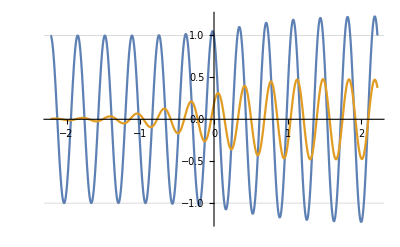

```mathematica
Plot[Evaluate[Re[Normal[
vx[t]/.solPertEvalSingleOsc1/.param/.A[1]->1/.T->1
]/.ϵ->1/.κ->1]],{t,-6*2π/ω[1],6*2π/ω[1]}/.param,PlotRange->All,GridLines->grid[1]]
```

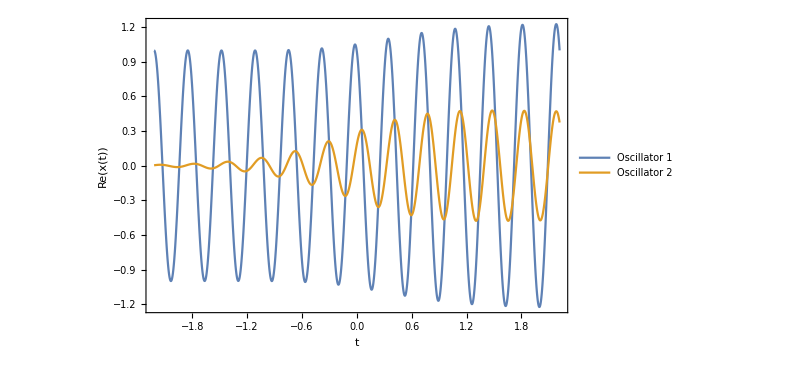

```mathematica
Plot[Evaluate[Re[Normal[
vx[t]/.solPertEvalSingleOsc1/.param/.A[1]->1/.T->1
]/.ϵ->1/.κ->1]],{t,-6*2π/ω[1],6*2π/ω[1]}/.param,PlotRange->All,GridLines->{{-2,-1.5,-1,-0.5,0.5,1,1.5,2},{√2 √ω[1],√2 √ω[1]/2,-√2 √ω[1],-√2 √ω[1]/2}/.param},ImageSize->600,Frame->True,
BaseStyle->{FontFamily->"CMU Serif",FontSize->10},
AxesLabel->{ToExpression["t",TeXForm,HoldForm],ToExpression["\\mathrm{Re}\\left[x(t)\\right]",TeXForm,HoldForm]},
PlotLegends->Placed[LineLegend[{"Oscillator 1","Oscillator 2"},LegendFunction->(Framed[#,FrameMargins->0,FrameStyle->Gray,Background->White]&)],{Right,Bottom}]]
```

#### Plot 2: Heavier second oscillator (much worse results)

Old parameters: ω[2] > ω[1]

```mathematica
param2={
(*Asymptotic frequencies:*)
(*Osc. 1:*) ω[1]->3^2,
(*Osc. 2:*) ω[2]->4^2,
(*Coupl.:*) ω[c]->0,

(*Peak-related variable:*)
(*Osc. 1:*) α[1]->3.1^2,
(*Osc. 2:*) α[2]->2.6^2,
(*Coupl.:*) α[c]->4(*^2*),

(*Width-related variable:*)
(*Osc. 1:*) τ[1]->1,
(*Osc. 2:*) τ[2]->1,
(*Coupl.:*) τ[c]->1.5
};
```

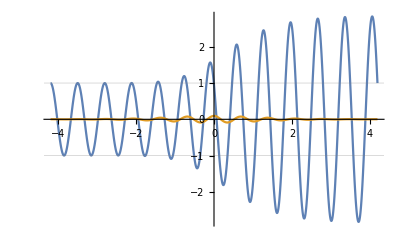

```mathematica
Plot[Evaluate[Re[Normal[
vx[t]/.solPertEvalSingleOsc1/.param2/.A[1]->1/.T->1
]/.ϵ->1/.κ->1]],smalldomain,PlotRange->All,GridLines->grid[1]]
```

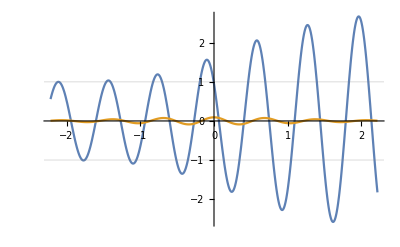

```mathematica
Plot[Evaluate[Re[Normal[
vx[t]/.solPertEvalSingleOsc1/.param2/.A[1]->1/.T->1
]/.ϵ->1/.κ->1]],{t,-6*2π/ω[1],6*2π/ω[1]}/.param,PlotRange->All,GridLines->grid[1]]
```

#### Plot 3: Near the resonance

```mathematica
param3={
(*Asymptotic frequencies:*)
(*Osc. 1:*) ω[1]->3^2,
(*Osc. 2:*) ω[2]->3.1^2,(*
(*Osc. 3:*) ω[3]->1,*)
(*Coupl.:*) ω[c]->0,

(*Peak-related variable:*)
(*Osc. 1:*) α[1]->3.1^2,
(*Osc. 2:*) α[2]->2.6^2,(*
(*Osc. 3:*) α[3]->1,*)
(*Coupl.:*) α[c]->4(*^2*),

(*Width-related variable:*)
(*Osc. 1:*) τ[1]->1,
(*Osc. 2:*) τ[2]->1,(*
(*Osc. 3:*) τ[3]->1,*)
(*Coupl.:*) τ[c]->1.5
};
```

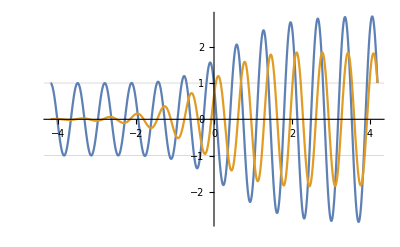

```mathematica
Plot[Evaluate[Re[Normal[
vx[t]/.solPertEvalSingleOsc1/.param3/.A[1]->1/.T->1
]/.ϵ->1/.κ->1]],smalldomain,PlotRange->All,GridLines->grid[1]]
```

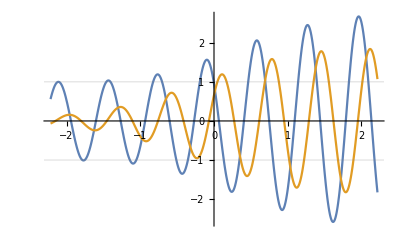

```mathematica
Plot[Evaluate[Re[Normal[
vx[t]/.solPertEvalSingleOsc1/.param3/.A[1]->1/.T->1
]/.ϵ->1/.κ->1]],{t,-6*2π/ω[1],6*2π/ω[1]}/.param,PlotRange->All,GridLines->grid[1]]
```

## Comparisons

## Static comparisons

### Perturbative (1st-order) vs. numerical (full)

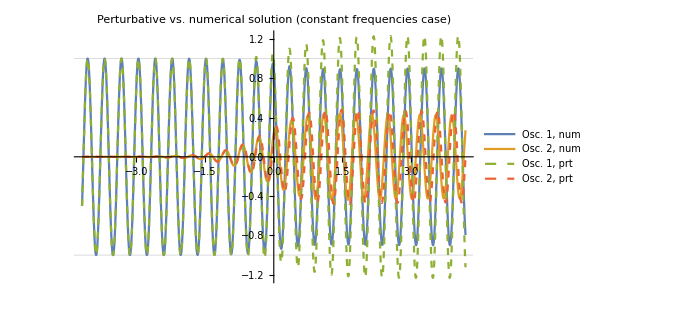

```mathematica
Plot[Evaluate[{
Re[{vx[t]}]/.solNumSingleOsc1Const,
Re[Normal[
vx[t]/.solPertEvalSingleOsc1/.param/.A[1]->1/.T->1
]/.ϵ->1/.κ->1]
}],smalldomain,PlotRange->All,GridLines->grid[1],
PlotStyle->{SolidData,SolidData(*,SolidData*),Dashed,Dashed(*,Dashed*)},
PlotLabel->"Perturbative vs. numerical solution
(constant frequencies case)",
PlotLegends->{"Osc. 1, num","Osc. 2, num"(*,"Osc. 3, num"*),"Osc. 1, prt","Osc. 2, prt"(*,"Osc. 3, prt"*)},ImageSize->500]
```

### Perturbative (1st-order) vs. numerical, order-by-order (1st-order)

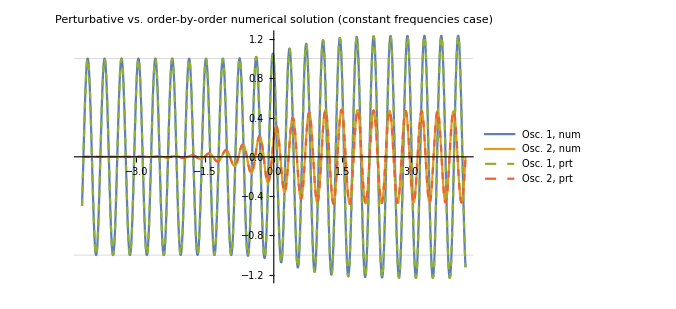

```mathematica
Plot[Evaluate[{
Re[{resultNumOrderbyOrderSingleOsc1Const[[3]],resultNumOrderbyOrderSingleOsc1Const[[4]]}],
Re[Normal[
vx[t]/.solPertEvalSingleOsc1/.param/.A[1]->1/.T->1
]/.ϵ->1/.κ->1]
}],smalldomain,PlotRange->All,GridLines->grid[1],
PlotStyle->{SolidData,SolidData(*,SolidData*),Dashed,Dashed(*,Dashed*)},
PlotLabel->"Perturbative vs. order-by-order numerical solution
(constant frequencies case)",
PlotLegends->{"Osc. 1, num","Osc. 2, num"(*,"Osc. 3, num"*),"Osc. 1, prt","Osc. 2, prt"(*,"Osc. 3, prt"*)},ImageSize->500]
```

### Perturbative (1st-order) vs. numerical, order-by-order (2nd-order)

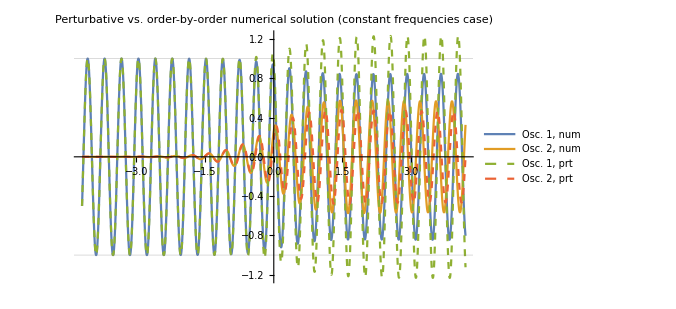

```mathematica
Plot[Evaluate[{
Re[{vx[t]}]/.solNumOrdersSingleOsc1Const,
Re[Normal[
vx[t]/.solPertEvalSingleOsc1/.param/.A[1]->1/.T->1
]/.ϵ->1/.κ->1]
}],smalldomain,PlotRange->All,GridLines->grid[1],
PlotStyle->{SolidData,SolidData(*,SolidData*),Dashed,Dashed(*,Dashed*)},
PlotLabel->"Perturbative vs. order-by-order numerical solution
(constant frequencies case)",
PlotLegends->{"Osc. 1, num","Osc. 2, num"(*,"Osc. 3, num"*),"Osc. 1, prt","Osc. 2, prt"(*,"Osc. 3, prt"*)},ImageSize->500]
```

### Perturbative (1st-order) vs. parametric-numerical, order-by-order (1st-order)

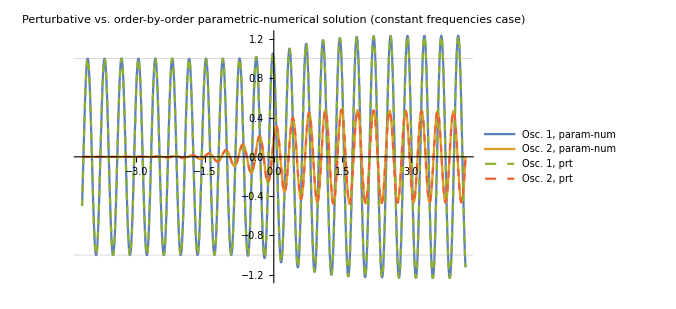

```mathematica
Plot[Evaluate[Re[{
x[0][1][ω[1],ω[2],0,α[c],τ[c]][t]+x[1][1][ω[1],ω[2],0,α[c],τ[c]][t]/.paramsolPertNum/.param,
x[0][2][ω[1],ω[2],0,α[c],τ[c]][t]+x[1][2][ω[1],ω[2],0,α[c],τ[c]][t]/.paramsolPertNum/.param,
Normal[vx[t]/.solPertEvalSingleOsc1/.A[1]->1/.T->1]/.ϵ->1/.κ->1/.param
}]],smalldomain,PlotRange->All,GridLines->grid[1],
PlotStyle->{SolidData,SolidData(*,SolidData*),Dashed,Dashed(*,Dashed*)},
PlotLabel->"Perturbative vs. order-by-order parametric-numerical solution
(constant frequencies case)",
PlotLegends->{"Osc. 1, param-num","Osc. 2, param-num"(*,"Osc. 3, param-num"*),"Osc. 1, prt","Osc. 2, prt"(*,"Osc. 3, prt"*)},ImageSize->500]
```

### Perturbative (1st-order) vs. parametric-numerical, order-by-order (2nd-order)

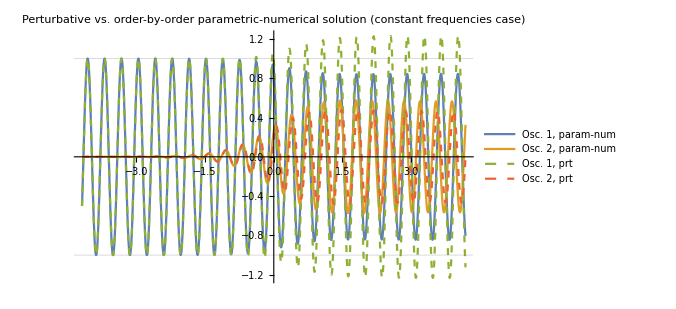

```mathematica
Plot[Evaluate[Re[{
x[0][1][ω[1],ω[2],0,α[c],τ[c]][t]+x[1][1][ω[1],ω[2],0,α[c],τ[c]][t]+x[2][1][ω[1],ω[2],0,α[c],τ[c]][t]/.paramsolPertNum/.param,
x[0][2][ω[1],ω[2],0,α[c],τ[c]][t]+x[1][2][ω[1],ω[2],0,α[c],τ[c]][t]+x[2][2][ω[1],ω[2],0,α[c],τ[c]][t]/.paramsolPertNum/.param,
Normal[vx[t]/.solPertEvalSingleOsc1/.A[1]->1/.T->1]/.ϵ->1/.κ->1/.param
}]],smalldomain,PlotRange->All,GridLines->grid[1],
PlotStyle->{SolidData,SolidData(*,SolidData*),Dashed,Dashed(*,Dashed*)},
PlotLabel->"Perturbative vs. order-by-order parametric-numerical solution
(constant frequencies case)",
PlotLegends->{"Osc. 1, param-num","Osc. 2, param-num"(*,"Osc. 3, param-num"*),"Osc. 1, prt","Osc. 2, prt"(*,"Osc. 3, prt"*)},ImageSize->500]
```

### Numerical (full) vs. order-by-order numerical (2nd-order)

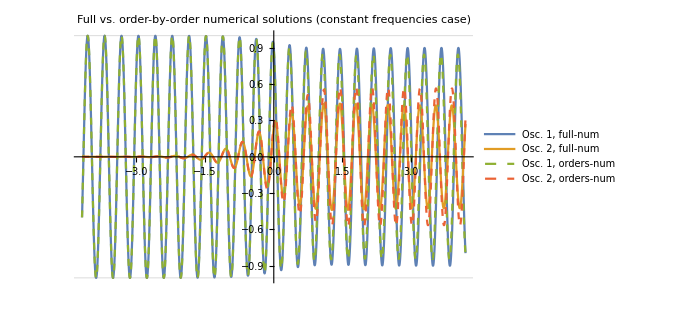

```mathematica
Plot[Evaluate[{
Re[{vx[t]}]/.solNumSingleOsc1Const,
Re[{vx[t]}]/.solNumOrdersSingleOsc1Const
}],smalldomain,PlotRange->All,GridLines->grid[1],
PlotStyle->{SolidData,SolidData(*,SolidData*),Dashed,Dashed(*,Dashed*)},
PlotLabel->"Full vs. order-by-order numerical solutions
(constant frequencies case)",
PlotLegends->{"Osc. 1, full-num","Osc. 2, full-num"(*,"Osc. 3, full-num"*),"Osc. 1, orders-num","Osc. 2, orders-num"(*,"Osc. 3, orders-num"*)},ImageSize->500]
```

## Parametric comparisons (manipulable)

### Numerical (full) vs. order-by-order numerical

Here the display solutions are both numerical, because this way Mathematica handles better the manipulable plots. One can see in the static comparisons above that the 1st-order perturbative solution, with analytical form, is equivalent to the 1st-order numerical solution.

#### 1st order vs. full solution

```mathematica
Manipulate[Plot[Evaluate[Re[{
x[1][ω1,ω2,0,αc,τc][t]/.paramsolNum,
x[2][ω1,ω2,0,αc,τc][t]/.paramsolNum,
(*ωc^2+αc^2*)Sech[t/τc]^2,
x[0][1][ω1,ω2,0,αc,τc][t]+x[1][1][ω1,ω2,0,αc,τc][t]/.paramsolPertNum,
x[0][2][ω1,ω2,0,αc,τc][t]+x[1][2][ω1,ω2,0,αc,τc][t]/.paramsolPertNum
}]],{t,-4*2π/ω1,4*2π/ω1},PlotRange->All,GridLines->grid[1],
PlotStyle->plotStylePertAll,PlotLegends->plotLegendsPert,ImageSize->500],
Style["Parameters",12],{{ω1,π,"ω_1"},0.1,20},{{ω2,5,"ω_2"},0.1,20},{{αc,1.5,"α_c"},0.1,20},{{τc,1,"τ_c"},0.1,20}]
```

#### 2nd order vs. full solution

```mathematica
Manipulate[Plot[Evaluate[Re[{
x[1][ω1,ω2,0,αc,τc][t]/.paramsolNum,
x[2][ω1,ω2,0,αc,τc][t]/.paramsolNum,
(*ωc^2+αc^2*)Sech[t/τc]^2,
x[0][1][ω1,ω2,0,αc,τc][t]+x[1][1][ω1,ω2,0,αc,τc][t]+x[2][1][ω1,ω2,0,αc,τc][t]/.paramsolPertNum,
x[0][2][ω1,ω2,0,αc,τc][t]+x[1][2][ω1,ω2,0,αc,τc][t]+x[2][2][ω1,ω2,0,αc,τc][t]/.paramsolPertNum
}]],{t,-4*2π/ω1,4*2π/ω1},PlotRange->All,GridLines->grid[1],
PlotStyle->plotStylePertAll,PlotLegends->plotLegendsPert,ImageSize->500],
Style["Parameters",12],{{ω1,π,"ω_1"},0.1,20},{{ω2,5,"ω_2"},0.1,20},{{αc,1.5,"α_c"},0.1,20},{{τc,1,"τ_c"},0.1,20}]
```

#### Both orders vs. full solution

```mathematica
Manipulate[Plot[Evaluate[Re[{
x[1][ω1,ω2,0,αc,τc][t]/.paramsolNum,
x[2][ω1,ω2,0,αc,τc][t]/.paramsolNum,
(*ω[c]^2+αc^2*)Sech[t/τc]^2,
x[0][1][ω1,ω2,0,αc,τc][t]+x[1][1][ω1,ω2,0,αc,τc][t]/.paramsolPertNum,
x[0][2][ω1,ω2,0,αc,τc][t]+x[1][2][ω1,ω2,0,αc,τc][t]/.paramsolPertNum,
x[0][1][ω1,ω2,0,αc,τc][t]+x[1][1][ω1,ω2,0,αc,τc][t]+x[2][1][ω1,ω2,0,αc,τc][t]/.paramsolPertNum,
x[0][2][ω1,ω2,0,αc,τc][t]+x[1][2][ω1,ω2,0,αc,τc][t]+x[2][2][ω1,ω2,0,αc,τc][t]/.paramsolPertNum
}]],{t,-4*2π/ω1,4*2π/ω1},PlotRange->All,GridLines->grid[1],
PlotStyle->plotStylePertAll,PlotLegends->plotLegendsPert,ImageSize->500],
Style["Parameters",12],{{ω1,π,"ω_1"},0.1,20},{{ω2,5,"ω_2"},0.1,20},{{αc,1.5,"α_c"},0.1,20},{{τc,1,"τ_c"},0.1,20}]
```

## Representative plots: perturbative vs. exact solution

Recall that we achieve analyticity for the perturbative solution at 1st order, but not at 2nd, which we also compute numerically.

## Perturbative regime: small coupling, near resonance

Figure 3.3 in the report.

#### Solution:

```mathematica
Manipulate[{
Quiet@Plot[Evaluate[Re[{
x[1][ω1,ω2,0,αc,τc][t]/.paramsolNum,
x[2][ω1,ω2,0,αc,τc][t]/.paramsolNum,
(5*2αc)/(ω1+ω2)Sech[t/τc]^2,
x[0][1][ω1,ω2,0,αc,τc][t]+x[1][1][ω1,ω2,0,αc,τc][t]/.paramsolPertNum,
x[0][2][ω1,ω2,0,αc,τc][t]+x[1][2][ω1,ω2,0,αc,τc][t]/.paramsolPertNum,
x[0][1][ω1,ω2,0,αc,τc][t]+x[1][1][ω1,ω2,0,αc,τc][t]+x[2][1][ω1,ω2,0,αc,τc][t]/.paramsolPertNum,
x[0][2][ω1,ω2,0,αc,τc][t]+x[1][2][ω1,ω2,0,αc,τc][t]+x[2][2][ω1,ω2,0,αc,τc][t]/.paramsolPertNum
(*,Cos[ω1 (t-ti)]*)
}]],{t,-n*2π/ω1,(n+2)*2π/ω1},PlotRange->{-1.18,2.18+top},GridLines->grid[1],
PlotStyle->plotStylePertAll,PlotLegends->plotLegendsPert,ImageSize->500],
N[(2αc/(ω1+ω2))"=c",2],N[(τc(ω1+ω2)/π),2]"=Δ"},
{{ω1,4π},0.1,20},{{ω2,3.5π},0.1,20},{{αc,1π},0.1,20},{{τc,0.5},0.1,20},{{top,-0.5},-1,5,0.5},{{n,2},0,10,1}]
```

#### Error:

```mathematica
Manipulate[{
Quiet@Plot[Evaluate[Re[{
Abs[(x[1][ω1,ω2,0,αc,τc][t]/.paramsolNum)-(x[0][1][ω1,ω2,0,αc,τc][t]+x[1][1][ω1,ω2,0,αc,τc][t]/.paramsolPertNum)],
Abs[(x[2][ω1,ω2,0,αc,τc][t]/.paramsolNum)-(x[0][2][ω1,ω2,0,αc,τc][t]+x[1][2][ω1,ω2,0,αc,τc][t]/.paramsolPertNum)],
Abs[(x[1][ω1,ω2,0,αc,τc][t]/.paramsolNum)-(x[0][1][ω1,ω2,0,αc,τc][t]+x[1][1][ω1,ω2,0,αc,τc][t]+x[2][1][ω1,ω2,0,αc,τc][t]/.paramsolPertNum)],
Abs[(x[2][ω1,ω2,0,αc,τc][t]/.paramsolNum)-(x[0][2][ω1,ω2,0,αc,τc][t]+x[1][2][ω1,ω2,0,αc,τc][t]+x[2][2][ω1,ω2,0,αc,τc][t]/.paramsolPertNum)]
}
]],{t,-n*2π/ω1,(n+2)*2π/ω1},PlotRange->{-1.18,2.18+top}*10^-1,
PlotStyle->plotStyleErrors,PlotLegends->plotLegendsErrors,ImageSize->500],
N[(2αc/(ω1+ω2))"=c",2],N[(τc(ω1+ω2)/π),2]"=Δ"},
{{ω1,4π},0.1,20},{{ω2,3.5π},0.1,20},{{αc,1π},0.1,20},{{τc,0.5},0.1,20},{{top,-0.5},-1,5,0.5},{{n,2},0,10,1}]
```

## More regimes

Figure 3.4 in the report (a-f)

#### a) Far from resonance (i.e. non-excitement): stronger coupling allowed

```mathematica
Manipulate[{
Quiet@Plot[Evaluate[Re[{
x[1][ω1,ω2,0,αc,τc][t]/.paramsolNum,
x[2][ω1,ω2,0,αc,τc][t]/.paramsolNum,
(5*2αc)/(ω1+ω2)Sech[t/τc]^2,
x[0][1][ω1,ω2,0,αc,τc][t]+x[1][1][ω1,ω2,0,αc,τc][t]/.paramsolPertNum,
x[0][2][ω1,ω2,0,αc,τc][t]+x[1][2][ω1,ω2,0,αc,τc][t]/.paramsolPertNum,
x[0][1][ω1,ω2,0,αc,τc][t]+x[1][1][ω1,ω2,0,αc,τc][t]+x[2][1][ω1,ω2,0,αc,τc][t]/.paramsolPertNum,
x[0][2][ω1,ω2,0,αc,τc][t]+x[1][2][ω1,ω2,0,αc,τc][t]+x[2][2][ω1,ω2,0,αc,τc][t]/.paramsolPertNum
(*,Cos[ω1 (t-ti)]*)
}]],{t,-n*2π/ω1,(n+2)*2π/ω1},PlotRange->{-1.18,2.18+top},GridLines->grid[1],
PlotStyle->plotStylePertAll,PlotLegends->plotLegendsPert,ImageSize->500],
N[(2αc/(ω1+ω2))"=c",2],N[(τc(ω1+ω2)/π),2]"=Δ"},
{{ω1,8π},0.1,30},{{ω2,2π},0.1,30},{{αc,2.5π},0.1,20},{{τc,0.2},0.1,20},{{top,0.5},-1,5,0.5},{{n,3},0,10,1}]
```

#### b) Higher frequencies (near resonance): also stronger coupling allowed

High frequencies:

```mathematica
Manipulate[{
Quiet@Plot[Evaluate[Re[{
x[1][ω1,ω2,0,αc,τc][t]/.paramsolNum,
x[2][ω1,ω2,0,αc,τc][t]/.paramsolNum,
(5*2αc)/(ω1+ω2)Sech[t/τc]^2,
x[0][1][ω1,ω2,0,αc,τc][t]+x[1][1][ω1,ω2,0,αc,τc][t]/.paramsolPertNum,
x[0][2][ω1,ω2,0,αc,τc][t]+x[1][2][ω1,ω2,0,αc,τc][t]/.paramsolPertNum,
x[0][1][ω1,ω2,0,αc,τc][t]+x[1][1][ω1,ω2,0,αc,τc][t]+x[2][1][ω1,ω2,0,αc,τc][t]/.paramsolPertNum,
x[0][2][ω1,ω2,0,αc,τc][t]+x[1][2][ω1,ω2,0,αc,τc][t]+x[2][2][ω1,ω2,0,αc,τc][t]/.paramsolPertNum
(*,Cos[ω1 (t-ti)]*)
}]],{t,-n*2π/ω1,(n+2)*2π/ω1},PlotRange->{-1.18,2.18+top},GridLines->grid[1],
PlotStyle->plotStylePertAll,PlotLegends->plotLegendsPert,ImageSize->500],
N[(2αc/(ω1+ω2))"=c",2],N[(τc(ω1+ω2)/π),2]"=Δ"},
{{ω1,12π},0.1,50},{{ω2,8π},0.1,50},{{αc,4.5π},0.1,50},{{τc,0.1},0.01,20},{{top,0.5},-1,5,0.5},{{n,3},0,10,1}]
```

Higher frequencies (I like it less):

```mathematica
Manipulate[{
Quiet@Plot[Evaluate[Re[{
x[1][ω1,ω2,0,αc,τc][t]/.paramsolNum,
x[2][ω1,ω2,0,αc,τc][t]/.paramsolNum,
(5*2αc)/(ω1+ω2)Sech[t/τc]^2,
x[0][1][ω1,ω2,0,αc,τc][t]+x[1][1][ω1,ω2,0,αc,τc][t]/.paramsolPertNum,
x[0][2][ω1,ω2,0,αc,τc][t]+x[1][2][ω1,ω2,0,αc,τc][t]/.paramsolPertNum,
x[0][1][ω1,ω2,0,αc,τc][t]+x[1][1][ω1,ω2,0,αc,τc][t]+x[2][1][ω1,ω2,0,αc,τc][t]/.paramsolPertNum,
x[0][2][ω1,ω2,0,αc,τc][t]+x[1][2][ω1,ω2,0,αc,τc][t]+x[2][2][ω1,ω2,0,αc,τc][t]/.paramsolPertNum
(*,Cos[ω1 (t-ti)]*)
}]],{t,-n*2π/ω1,(n+2)*2π/ω1},PlotRange->{-1.18,2.18+top},GridLines->grid[1],
PlotStyle->plotStylePertAll,PlotLegends->plotLegendsPert,ImageSize->500],
N[(2αc/(ω1+ω2))"=c",2],N[(τc(ω1+ω2)/π),2]"=Δ"},
{{ω1,18π},0.1,60},{{ω2,9π},0.1,60},{{αc,6π},0.1,60},{{τc,0.075},0.03,20},{{top,1},-1,5,0.5},{{n,3},0,10,1}]
```

#### c) & d) Approaching the breakdown (with separate 1st vs. 2nd order comparison)

```mathematica
Manipulate[{
Quiet@Plot[Evaluate[Re[{
x[1][ω1,ω2,0,αc,τc][t]/.paramsolNum,
x[2][ω1,ω2,0,αc,τc][t]/.paramsolNum,
(5*2αc)/(ω1+ω2)Sech[t/τc]^2,
x[0][1][ω1,ω2,0,αc,τc][t]+x[1][1][ω1,ω2,0,αc,τc][t]/.paramsolPertNum,
x[0][2][ω1,ω2,0,αc,τc][t]+x[1][2][ω1,ω2,0,αc,τc][t]/.paramsolPertNum,,
(*,Cos[ω1 (t-ti)]*)
}]],{t,-n*2π/ω1,(n+2)*2π/ω1},PlotRange->{-1.28,2.18+top},GridLines->grid[1],
PlotStyle->plotStylePertAll,PlotLegends->plotLegendsPert,ImageSize->400],
Quiet@Plot[Evaluate[Re[{
x[1][ω1,ω2,0,αc,τc][t]/.paramsolNum,
x[2][ω1,ω2,0,αc,τc][t]/.paramsolNum,
(5*2αc)/(ω1+ω2)Sech[t/τc]^2,,,
x[0][1][ω1,ω2,0,αc,τc][t]+x[1][1][ω1,ω2,0,αc,τc][t]+x[2][1][ω1,ω2,0,αc,τc][t]/.paramsolPertNum,
x[0][2][ω1,ω2,0,αc,τc][t]+x[1][2][ω1,ω2,0,αc,τc][t]+x[2][2][ω1,ω2,0,αc,τc][t]/.paramsolPertNum
(*,Cos[ω1 (t-ti)]*)
}]],{t,-n*2π/ω1,(n+2)*2π/ω1},PlotRange->{-1.28,2.18+top},GridLines->grid[1],
PlotStyle->plotStylePertAll,ImageSize->400]},
{{ω1,2π},0.1,20},{{ω2,1.6π},0.1,20},{{αc,0.9π},0.1,20},{{τc,0.5},0.1,20},{{top,0.5},-1,5,0.5},{{n,2},0,10,1}]
```

#### e) The breakdown

```mathematica
Manipulate[{
Quiet@Plot[Evaluate[Re[{
x[1][ω1,ω2,0,αc,τc][t]/.paramsolNum,
x[2][ω1,ω2,0,αc,τc][t]/.paramsolNum,
(5*2αc)/(ω1+ω2)Sech[t/τc]^2,(*,,*)
x[0][1][ω1,ω2,0,αc,τc][t]+x[1][1][ω1,ω2,0,αc,τc][t]/.paramsolPertNum,
x[0][2][ω1,ω2,0,αc,τc][t]+x[1][2][ω1,ω2,0,αc,τc][t]/.paramsolPertNum,
x[0][1][ω1,ω2,0,αc,τc][t]+x[1][1][ω1,ω2,0,αc,τc][t]+x[2][1][ω1,ω2,0,αc,τc][t]/.paramsolPertNum,
x[0][2][ω1,ω2,0,αc,τc][t]+x[1][2][ω1,ω2,0,αc,τc][t]+x[2][2][ω1,ω2,0,αc,τc][t]/.paramsolPertNum
(*,Cos[ω1 (t-ti)]*)
}]],{t,-n*2π/ω1,(n+1)*2π/ω1},PlotRange->{-1.18-2top,2.18+2top},GridLines->grid[1],
PlotStyle->plotStylePertAll,PlotLegends->plotLegendsPert,ImageSize->500],
N[(2αc/(ω1+ω2))"=c",2],N[(τc(ω1+ω2)/π),2]"=Δ"},
{{ω1,2π},0.1,20},{{ω2,1.8π},0.1,20},{{αc,1.3π},0.1,20},{{τc,0.5},0.1,20},{{top,0.6},-1,5,0.5},{{n,2},0,10,1}]
```

#### f) Recovering good results in the “sudden” regime

```mathematica
Manipulate[{
Quiet@Plot[Evaluate[Re[{
x[1][ω1,ω2,0,αc,τc][t]/.paramsolNum,
x[2][ω1,ω2,0,αc,τc][t]/.paramsolNum,
(5*2αc)/(ω1+ω2)Sech[t/τc]^2,
x[0][1][ω1,ω2,0,αc,τc][t]+x[1][1][ω1,ω2,0,αc,τc][t]/.paramsolPertNum,
x[0][2][ω1,ω2,0,αc,τc][t]+x[1][2][ω1,ω2,0,αc,τc][t]/.paramsolPertNum,
x[0][1][ω1,ω2,0,αc,τc][t]+x[1][1][ω1,ω2,0,αc,τc][t]+x[2][1][ω1,ω2,0,αc,τc][t]/.paramsolPertNum,
x[0][2][ω1,ω2,0,αc,τc][t]+x[1][2][ω1,ω2,0,αc,τc][t]+x[2][2][ω1,ω2,0,αc,τc][t]/.paramsolPertNum
(*,Cos[ω1 (t-ti)]*)
}]],{t,-n*2π/ω1,(n+2)*2π/ω1},PlotRange->{-1.28,2.18+top},GridLines->grid[1],
PlotStyle->plotStylePertAll,PlotLegends->plotLegendsPert,ImageSize->500],
N[(2αc/(ω1+ω2))"=c",2],N[(τc(ω1+ω2)/π),2]"=Δ"},
{{ω1,2π},0.1,20},{{ω2,1.4π},0.1,20},{{αc,1.7π},0.1,20},{{τc,0.1},0.1,20},{{top,3},-1,5,0.5},{{n,2},0,10,1}]
```

## Even more

#### Extra: small coupling, exact resonance

```mathematica
Manipulate[{
Quiet@Plot[Evaluate[Re[{
x[1][ω1,ω2,0,αc,τc][t]/.paramsolNum,
x[2][ω1,ω2,0,αc,τc][t]/.paramsolNum,
(5*2αc)/(ω1+ω2)Sech[t/τc]^2,
x[0][1][ω1,ω2,0,αc,τc][t]+x[1][1][ω1,ω2,0,αc,τc][t]/.paramsolPertNum,
x[0][2][ω1,ω2,0,αc,τc][t]+x[1][2][ω1,ω2,0,αc,τc][t]/.paramsolPertNum,
x[0][1][ω1,ω2,0,αc,τc][t]+x[1][1][ω1,ω2,0,αc,τc][t]+x[2][1][ω1,ω2,0,αc,τc][t]/.paramsolPertNum,
x[0][2][ω1,ω2,0,αc,τc][t]+x[1][2][ω1,ω2,0,αc,τc][t]+x[2][2][ω1,ω2,0,αc,τc][t]/.paramsolPertNum
(*,Cos[ω1 (t-ti)]*)
}]],{t,-n*2π/ω1,(n+2)*2π/ω1},PlotRange->{-1.18,2.18+top},GridLines->grid[1],
PlotStyle->plotStylePertAll,PlotLegends->plotLegendsPert,ImageSize->500],
N[(2αc/(ω1+ω2))"=c",2],N[(τc(ω1+ω2)/π),2]"=Δ"},
{{ω1,2π},0.1,20},{{ω2,2π},0.1,20},{{αc,0.7π},0.1,20},{{τc,0.5},0.1,20},{{top,0},-1,5,0.5},{{n,3},0,10,1}]
```

#### Extra^2: Inverted frequencies (ω_2>ω_1), with moderately-strong coupling

```mathematica
Manipulate[{
Quiet@Plot[Evaluate[Re[{
x[1][ω1,ω2,0,αc,τc][t]/.paramsolNum,
x[2][ω1,ω2,0,αc,τc][t]/.paramsolNum,
(5*2αc)/(ω1+ω2)Sech[t/τc]^2,
x[0][1][ω1,ω2,0,αc,τc][t]+x[1][1][ω1,ω2,0,αc,τc][t]/.paramsolPertNum,
x[0][2][ω1,ω2,0,αc,τc][t]+x[1][2][ω1,ω2,0,αc,τc][t]/.paramsolPertNum,
x[0][1][ω1,ω2,0,αc,τc][t]+x[1][1][ω1,ω2,0,αc,τc][t]+x[2][1][ω1,ω2,0,αc,τc][t]/.paramsolPertNum,
x[0][2][ω1,ω2,0,αc,τc][t]+x[1][2][ω1,ω2,0,αc,τc][t]+x[2][2][ω1,ω2,0,αc,τc][t]/.paramsolPertNum
(*,Cos[ω1 (t-ti)]*)
}]],{t,-n*2π/ω1,(n+2)*2π/ω1},PlotRange->{-1.18-1.2top,2.18+top},GridLines->grid[1],
PlotStyle->plotStylePertAll,PlotLegends->plotLegendsPert,ImageSize->500],
N[(2αc/(ω1+ω2))"=c",2],N[(τc(ω1+ω2)/π),2]"=Δ"},
{{ω1,2π},0.1,30},{{ω2,6π},0.1,30},{{αc,2π},0.1,20},{{τc,0.2},0.1,20},{{top,0.5},-1,5,0.5},{{n,3},0,10,1}]
```

Higher frequencies, better accuracy:

```mathematica
Manipulate[{
Quiet@Plot[Evaluate[Re[{
x[1][ω1,ω2,0,αc,τc][t]/.paramsolNum,
x[2][ω1,ω2,0,αc,τc][t]/.paramsolNum,
(5*2αc)/(ω1+ω2)Sech[t/τc]^2,
x[0][1][ω1,ω2,0,αc,τc][t]+x[1][1][ω1,ω2,0,αc,τc][t]/.paramsolPertNum,
x[0][2][ω1,ω2,0,αc,τc][t]+x[1][2][ω1,ω2,0,αc,τc][t]/.paramsolPertNum,
x[0][1][ω1,ω2,0,αc,τc][t]+x[1][1][ω1,ω2,0,αc,τc][t]+x[2][1][ω1,ω2,0,αc,τc][t]/.paramsolPertNum,
x[0][2][ω1,ω2,0,αc,τc][t]+x[1][2][ω1,ω2,0,αc,τc][t]+x[2][2][ω1,ω2,0,αc,τc][t]/.paramsolPertNum
(*,Cos[ω1 (t-ti)]*)
}]],{t,-n*2π/ω1,(n+2)*2π/ω1},PlotRange->{-1.18-1.2top,2.18+top},GridLines->grid[1],
PlotStyle->plotStylePertAll,PlotLegends->plotLegendsPert,ImageSize->500],
N[(2αc/(ω1+ω2))"=c",2],N[(τc(ω1+ω2)/π),2]"=Δ"},
{{ω1,10π},0.1,100},{{ω2,16π},0.1,100},{{αc,6.5π},0.1,100},{{τc,0.05},0.01,20},{{top,0.5},-1,5,0.5},{{n,3},0,10,1}]
```

#### Extra^3: The inverted frequencies inverted

```mathematica
Manipulate[{
Quiet@Plot[Evaluate[Re[{
x[1][ω1,ω2,0,αc,τc][t]/.paramsolNum,
x[2][ω1,ω2,0,αc,τc][t]/.paramsolNum,
(5*2αc)/(ω1+ω2)Sech[t/τc]^2,
x[0][1][ω1,ω2,0,αc,τc][t]+x[1][1][ω1,ω2,0,αc,τc][t]/.paramsolPertNum,
x[0][2][ω1,ω2,0,αc,τc][t]+x[1][2][ω1,ω2,0,αc,τc][t]/.paramsolPertNum,
x[0][1][ω1,ω2,0,αc,τc][t]+x[1][1][ω1,ω2,0,αc,τc][t]+x[2][1][ω1,ω2,0,αc,τc][t]/.paramsolPertNum,
x[0][2][ω1,ω2,0,αc,τc][t]+x[1][2][ω1,ω2,0,αc,τc][t]+x[2][2][ω1,ω2,0,αc,τc][t]/.paramsolPertNum
(*,Cos[ω1 (t-ti)]*)
}]],{t,-n*2π/ω1,(n+2)*2π/ω1},PlotRange->{-1.18-1.2top,2.18+top},GridLines->grid[1],
PlotStyle->plotStylePertAll,PlotLegends->plotLegendsPert,ImageSize->500],
N[(2αc/(ω1+ω2))"=c",2],N[(τc(ω1+ω2)/π),2]"=Δ"},
{{ω1,6π},0.1,30},{{ω2,2π},0.1,30},{{αc,2π},0.1,20},{{τc,0.2},0.1,20},{{top,0.5},-1,5,0.5},{{n,3},0,10,1}]
```

Higher frequencies, better accuracy:

```mathematica
Manipulate[{
Quiet@Plot[Evaluate[Re[{
x[1][ω1,ω2,0,αc,τc][t]/.paramsolNum,
x[2][ω1,ω2,0,αc,τc][t]/.paramsolNum,
(5*2αc)/(ω1+ω2)Sech[t/τc]^2,
x[0][1][ω1,ω2,0,αc,τc][t]+x[1][1][ω1,ω2,0,αc,τc][t]/.paramsolPertNum,
x[0][2][ω1,ω2,0,αc,τc][t]+x[1][2][ω1,ω2,0,αc,τc][t]/.paramsolPertNum,
x[0][1][ω1,ω2,0,αc,τc][t]+x[1][1][ω1,ω2,0,αc,τc][t]+x[2][1][ω1,ω2,0,αc,τc][t]/.paramsolPertNum,
x[0][2][ω1,ω2,0,αc,τc][t]+x[1][2][ω1,ω2,0,αc,τc][t]+x[2][2][ω1,ω2,0,αc,τc][t]/.paramsolPertNum
(*,Cos[ω1 (t-ti)]*)
}]],{t,-n*2π/ω1,(n+2)*2π/ω1},PlotRange->{-1.18-1.2top,2.18+top},GridLines->grid[1],
PlotStyle->plotStylePertAll,PlotLegends->plotLegendsPert,ImageSize->500],
N[(2αc/(ω1+ω2))"=c",2],N[(τc(ω1+ω2)/π),2]"=Δ"},
{{ω1,16π},0.1,100},{{ω2,10π},0.1,100},{{αc,6.5π},0.1,100},{{τc,0.05},0.01,20},{{top,0.5},-1,5,0.5},{{n,3},0,10,1}]
```

#### Extra^4: The good regime (near-resonant) with inverted frequencies (ω_2>ω_1): almost identical

This suggests that near the resonance the only important thing is the difference | ω_2>ω_1|.

```mathematica
Manipulate[{
Quiet@Plot[Evaluate[Re[{
x[1][ω1,ω2,0,αc,τc][t]/.paramsolNum,
x[2][ω1,ω2,0,αc,τc][t]/.paramsolNum,
(5*2αc)/(ω1+ω2)Sech[t/τc]^2,
x[0][1][ω1,ω2,0,αc,τc][t]+x[1][1][ω1,ω2,0,αc,τc][t]/.paramsolPertNum,
x[0][2][ω1,ω2,0,αc,τc][t]+x[1][2][ω1,ω2,0,αc,τc][t]/.paramsolPertNum,
x[0][1][ω1,ω2,0,αc,τc][t]+x[1][1][ω1,ω2,0,αc,τc][t]+x[2][1][ω1,ω2,0,αc,τc][t]/.paramsolPertNum,
x[0][2][ω1,ω2,0,αc,τc][t]+x[1][2][ω1,ω2,0,αc,τc][t]+x[2][2][ω1,ω2,0,αc,τc][t]/.paramsolPertNum
(*,Cos[ω1 (t-ti)]*)
}]],{t,-n*2π/ω1,(n+2)*2π/ω1},PlotRange->{-1.18,2.18+top},GridLines->grid[1],
PlotStyle->plotStylePertAll,PlotLegends->plotLegendsPert,ImageSize->500],
N[(2αc/(ω1+ω2))"=c",2],N[(τc(ω1+ω2)/π),2]"=Δ"},
{{ω1,3.5π},0.1,20},{{ω2,4π},0.1,20},{{αc,1π},0.1,20},{{τc,0.5},0.1,20},{{top,-0.5},-1,5,0.5},{{n,2},0,10,1}]
```